This is the data analysis from the output of the following files for the Ising Model Project: regular2D.py, and HexagonalLattice.py

## 1 D Ising Model

These runs come from the file regular2D.py file with the first dimension set to 1.

### Small lattice: 5 long, kT=1, 50 time steps

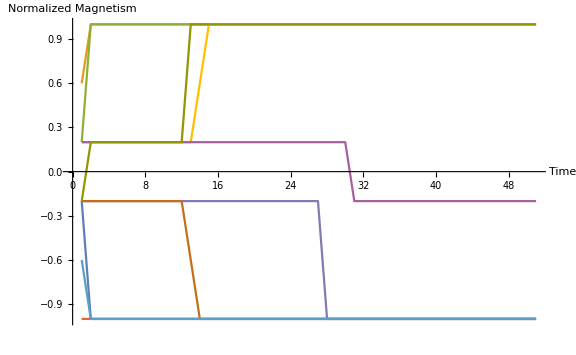

```mathematica
magnetism1={-1,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}/5;
magnetism2={3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}/5;
magnetism3={1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}/5;
magnetism4={-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}/5;
magnetism5={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}/5;
magnetism6={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-3,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}/5;
magnetism7={-3,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}/5;
magnetism8={1,1,1,1,1,1,1,1,1,1,1,1,1,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}/5;
magnetism9={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}/5;
magnetism10={-1,1,1,1,1,1,1,1,1,1,1,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}/5;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large]
```

Only one of these did not settle down within allotted time steps, which showns that this is likely below the critical temperature.

### Large Lattice: 200 long, kT=1, 400 time steps

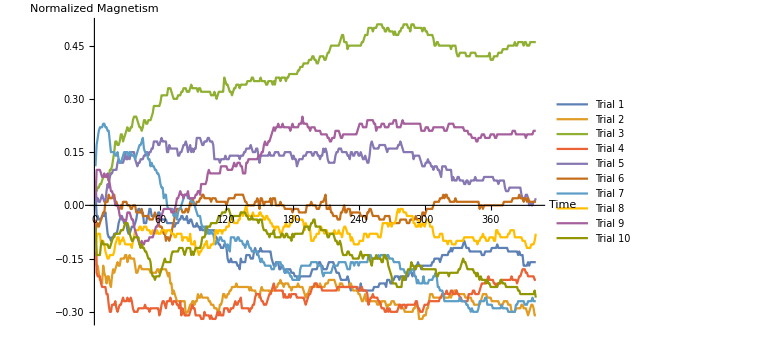

```mathematica
magnetism1={8,-6,-6,-8,-8,-8,-6,-6,-6,-4,-10,-16,-18,-18,-20,-18,-18,-16,-16,-16,-14,-10,-8,-6,-6,-8,-10,-10,-10,-14,-16,-16,-14,-12,-12,-12,-10,-8,-4,-2,-2,-4,-4,-4,-10,-10,-10,-6,-6,-2,-2,-6,-6,-6,-6,-6,-6,-4,-4,-6,-8,-8,-8,-8,-8,-10,-10,-10,-10,-10,-10,-12,-12,-10,-10,-10,-8,-8,-6,-6,-8,-8,-8,-6,-10,-10,-8,-8,-10,-12,-12,-12,-10,-12,-12,-14,-12,-14,-14,-14,-12,-12,-14,-14,-14,-14,-14,-14,-14,-18,-18,-20,-22,-22,-24,-24,-24,-22,-22,-24,-30,-32,-32,-30,-32,-32,-32,-32,-32,-34,-34,-36,-30,-32,-32,-32,-32,-28,-28,-28,-28,-30,-30,-30,-26,-24,-26,-28,-26,-26,-24,-26,-26,-26,-26,-26,-26,-26,-26,-26,-30,-32,-34,-34,-32,-32,-32,-36,-36,-34,-34,-36,-38,-36,-36,-36,-36,-36,-38,-38,-38,-40,-40,-40,-42,-42,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-38,-36,-36,-36,-36,-36,-34,-32,-32,-34,-34,-36,-36,-36,-36,-34,-32,-32,-32,-32,-32,-34,-36,-38,-38,-38,-40,-42,-42,-42,-42,-42,-42,-40,-42,-46,-48,-46,-46,-46,-46,-46,-48,-48,-48,-44,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-46,-46,-46,-46,-46,-44,-44,-44,-44,-44,-44,-46,-42,-42,-42,-44,-44,-42,-42,-40,-40,-40,-40,-42,-40,-40,-40,-40,-40,-42,-38,-40,-38,-36,-38,-40,-38,-36,-34,-34,-32,-34,-34,-36,-34,-34,-34,-34,-34,-34,-34,-34,-34,-32,-32,-30,-30,-30,-30,-30,-32,-30,-28,-28,-28,-28,-28,-28,-26,-26,-24,-26,-24,-24,-24,-24,-24,-24,-24,-24,-24,-22,-20,-22,-24,-24,-24,-26,-26,-26,-26,-26,-26,-26,-26,-26,-26,-26,-28,-28,-28,-26,-26,-26,-26,-26,-26,-24,-24,-24,-24,-24,-22,-24,-24,-24,-24,-24,-24,-24,-24,-24,-26,-26,-26,-26,-26,-26,-26,-26,-26,-28,-26,-28,-28,-28,-34,-34,-34,-34,-32,-34,-32,-32,-32,-32,-32,-32}/200;
magnetism2={-18,-34,-34,-38,-42,-42,-44,-34,-38,-40,-44,-40,-40,-44,-46,-40,-36,-38,-36,-34,-32,-34,-34,-30,-30,-30,-30,-28,-28,-32,-30,-28,-30,-30,-30,-30,-34,-38,-38,-36,-34,-34,-36,-36,-36,-36,-36,-36,-36,-36,-38,-38,-38,-38,-38,-38,-36,-36,-38,-36,-36,-36,-36,-36,-36,-38,-40,-38,-44,-44,-50,-48,-50,-52,-54,-54,-54,-54,-54,-54,-54,-54,-62,-60,-60,-58,-56,-56,-54,-54,-56,-54,-54,-50,-52,-52,-50,-52,-52,-52,-52,-52,-52,-54,-54,-56,-56,-56,-58,-58,-58,-60,-60,-56,-56,-54,-50,-50,-52,-52,-50,-50,-48,-48,-46,-46,-46,-46,-44,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-48,-46,-48,-48,-48,-48,-50,-50,-50,-52,-48,-46,-48,-48,-48,-48,-48,-48,-48,-50,-48,-48,-48,-48,-46,-46,-44,-44,-42,-44,-44,-46,-44,-44,-44,-44,-46,-46,-48,-46,-46,-46,-46,-46,-44,-46,-46,-46,-46,-48,-50,-52,-50,-50,-48,-46,-46,-46,-46,-46,-44,-46,-46,-46,-44,-46,-46,-46,-46,-44,-44,-44,-42,-42,-42,-42,-42,-42,-44,-46,-46,-48,-44,-44,-44,-46,-46,-46,-46,-46,-46,-44,-44,-46,-48,-48,-48,-48,-48,-50,-50,-52,-54,-54,-52,-50,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-56,-56,-54,-56,-54,-54,-54,-54,-56,-58,-56,-56,-56,-54,-54,-54,-56,-56,-56,-56,-56,-58,-58,-58,-58,-60,-60,-60,-60,-60,-60,-60,-60,-58,-58,-56,-56,-58,-64,-64,-64,-64,-62,-62,-62,-58,-58,-54,-50,-50,-50,-52,-52,-52,-52,-52,-52,-52,-52,-50,-50,-52,-52,-52,-52,-52,-50,-52,-50,-50,-48,-48,-48,-50,-50,-50,-50,-50,-50,-50,-52,-52,-52,-52,-52,-52,-54,-54,-56,-56,-56,-56,-56,-56,-54,-52,-50,-50,-50,-50,-52,-52,-52,-52,-54,-54,-54,-54,-54,-54,-54,-56,-56,-56,-56,-54,-54,-54,-54,-56,-56,-56,-60,-60,-60,-60,-58,-58,-58,-58,-58,-56,-56,-58,-58,-58,-60,-62,-60,-58,-56,-56,-58,-62,-62}/200;
magnetism3={14,8,10,10,12,12,14,16,16,16,16,16,14,20,20,22,26,30,36,36,34,34,36,40,40,36,38,40,42,44,42,42,44,44,48,50,50,50,48,46,44,44,42,44,48,48,46,46,48,48,48,50,52,56,56,56,56,56,56,58,62,62,62,62,62,62,66,66,66,64,62,60,60,60,60,62,62,62,64,64,66,66,66,64,64,64,66,68,66,66,66,66,66,64,66,66,64,64,64,64,64,64,64,64,64,62,62,62,64,62,60,62,64,64,64,64,64,72,70,68,68,66,64,64,62,64,66,66,68,68,68,66,68,68,68,68,68,68,70,70,70,70,72,72,70,70,70,70,70,70,72,70,70,70,70,68,68,70,70,70,70,68,70,68,72,72,72,72,70,72,72,72,72,70,72,72,74,74,74,74,74,74,74,74,76,76,78,78,78,80,80,80,80,80,82,82,82,84,84,82,82,80,80,82,84,84,84,84,82,82,84,86,86,88,90,90,90,90,90,90,90,90,92,94,96,96,92,92,92,88,90,90,90,90,90,90,90,90,90,90,90,90,92,92,94,96,96,96,100,100,100,100,98,100,100,100,102,102,102,102,102,100,100,98,98,100,100,98,98,98,98,96,98,96,96,96,98,98,100,100,102,102,102,102,100,100,98,102,102,102,100,100,100,100,100,100,100,98,100,100,98,98,96,96,96,96,96,94,90,90,92,92,90,90,90,90,90,90,90,90,90,90,90,88,90,90,90,90,86,84,84,86,86,86,86,86,86,84,84,84,84,86,86,86,86,86,84,84,84,84,84,84,84,84,84,84,84,84,86,82,82,82,84,84,84,84,86,86,86,86,88,88,88,88,88,90,90,90,90,90,90,92,90,90,92,92,92,92,92,90,92,92,90,90,90,92,92,92,92,92,92}/200;
magnetism4={-8,-38,-40,-40,-40,-44,-46,-46,-46,-46,-50,-50,-56,-60,-60,-56,-56,-56,-54,-58,-60,-58,-56,-56,-54,-52,-54,-54,-54,-52,-54,-54,-52,-54,-58,-60,-60,-60,-60,-58,-58,-58,-58,-58,-58,-56,-58,-58,-58,-60,-58,-58,-58,-58,-58,-58,-58,-58,-62,-60,-56,-54,-54,-56,-58,-54,-54,-54,-52,-54,-56,-54,-54,-54,-56,-56,-58,-54,-62,-58,-60,-62,-62,-62,-62,-62,-60,-58,-56,-58,-58,-62,-62,-62,-62,-62,-64,-64,-64,-60,-62,-62,-62,-62,-64,-62,-64,-64,-64,-64,-62,-60,-62,-60,-62,-62,-62,-58,-58,-58,-58,-60,-60,-58,-58,-58,-56,-54,-56,-56,-54,-54,-52,-58,-58,-58,-58,-58,-58,-58,-60,-58,-58,-56,-56,-52,-50,-50,-50,-50,-52,-54,-54,-56,-56,-56,-54,-52,-50,-50,-48,-46,-44,-48,-48,-48,-48,-48,-48,-48,-48,-52,-50,-52,-52,-52,-50,-52,-50,-50,-50,-50,-50,-52,-52,-52,-52,-52,-52,-52,-54,-56,-54,-52,-50,-50,-48,-46,-46,-44,-44,-44,-46,-46,-46,-46,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-48,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-48,-48,-48,-46,-48,-48,-48,-48,-50,-56,-54,-52,-52,-50,-52,-52,-52,-52,-54,-54,-56,-58,-58,-58,-60,-60,-58,-60,-58,-60,-60,-60,-60,-60,-60,-60,-58,-56,-56,-58,-56,-56,-56,-58,-56,-56,-56,-56,-56,-56,-56,-56,-54,-54,-58,-58,-60,-60,-60,-58,-56,-56,-56,-56,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-52,-52,-50,-50,-50,-50,-48,-50,-50,-50,-48,-48,-50,-50,-50,-48,-50,-50,-52,-52,-54,-54,-54,-54,-54,-54,-50,-50,-50,-50,-48,-48,-50,-50,-50,-50,-48,-46,-44,-44,-44,-44,-42,-42,-40,-42,-42,-42,-42,-44,-44,-46,-44,-44,-44,-44,-42,-42,-42,-42,-42,-42,-42,-42,-42,-40,-42,-42,-42,-42,-44,-42,-40,-40,-38,-36,-36,-36,-38,-38,-40,-40,-40,-40,-40,-40,-42,-42}/200;
magnetism5={12,2,4,2,2,4,6,4,2,2,8,12,10,16,18,18,20,20,20,20,24,26,24,24,24,24,26,30,26,26,28,26,30,30,30,30,26,24,22,24,24,26,26,26,28,28,30,30,28,30,30,32,32,36,36,36,36,34,34,36,38,36,36,36,36,30,30,34,32,32,32,32,32,32,32,28,28,30,30,32,34,34,36,34,30,32,34,30,32,30,32,32,38,38,38,38,36,34,34,36,36,36,38,38,36,36,36,34,26,26,26,26,26,24,26,26,26,26,28,26,26,26,28,28,28,28,28,28,28,28,28,26,28,28,28,30,30,32,32,32,32,34,32,30,30,30,32,32,28,24,28,28,28,28,28,28,28,28,30,28,28,28,28,30,30,30,30,28,28,28,28,28,30,30,30,30,30,30,28,26,28,26,26,22,24,26,26,26,26,28,28,28,30,30,30,30,30,28,28,30,30,30,28,28,26,28,28,32,30,32,30,26,24,24,24,24,24,24,28,30,30,32,32,32,30,30,30,30,30,28,28,26,30,30,28,28,30,30,30,28,28,30,28,26,26,28,26,24,24,28,34,36,34,32,32,32,32,32,34,34,34,34,34,34,32,30,32,32,32,32,32,32,32,32,32,34,34,36,34,32,30,30,30,30,30,30,30,30,30,26,28,28,28,28,28,26,24,22,22,22,24,24,26,24,24,22,22,20,22,22,22,20,20,18,16,22,22,22,22,20,20,20,20,20,14,16,14,14,14,16,16,14,14,14,14,12,12,14,14,12,12,14,14,14,14,16,14,14,14,14,14,14,14,16,16,16,16,16,16,16,16,16,14,14,14,14,12,14,14,14,14,14,10,8,8,8,10,10,10,10,10,10,10,10,10,10,10,6,4,4,4,6,6,4,0,2,0,0,2,2,4}/200;
magnetism6={-14,-12,-10,-12,-10,-8,-6,-4,-4,2,2,2,6,4,4,4,6,6,2,2,0,-2,-2,0,-2,2,2,2,2,0,0,0,-2,-2,0,0,0,-4,-4,-4,-4,-4,-2,-6,-6,-6,-6,-6,-6,-8,-8,-8,-8,-6,-4,-6,-8,-8,-12,-12,-12,-14,-16,-16,-20,-18,-18,-20,-18,-16,-12,-10,-6,-4,-2,-2,-2,-2,-2,-4,-4,-4,-2,-2,-4,-2,2,0,4,2,0,0,2,2,2,4,4,6,6,4,4,4,4,4,4,2,4,4,4,4,2,2,2,2,2,2,2,2,2,0,2,4,4,4,4,4,4,6,6,6,6,6,6,6,6,4,2,2,0,0,0,0,0,0,0,2,2,4,2,-2,4,4,2,0,2,2,2,2,2,4,0,4,4,4,0,0,0,0,2,0,0,0,-2,-2,-2,-2,-2,-2,-2,-4,-2,-2,-2,-2,-2,-4,-4,-4,-4,-4,-4,-4,0,0,0,0,2,0,0,0,0,-2,-2,-2,0,2,2,2,4,6,-2,-2,-2,0,-4,-4,-6,-6,-6,-6,-8,-8,-8,-4,-4,-2,0,-4,-4,-2,-2,-2,-6,-4,-4,-4,-4,-4,-4,-4,-4,-6,-6,-6,-6,-6,-8,-4,-4,-2,-2,-4,-6,-6,-6,-6,-6,-6,-8,-8,-8,-8,-8,-6,-6,-6,-6,-6,-10,-10,-10,-10,-10,-10,-10,-10,-10,-8,-8,-8,-8,-8,-8,-10,-10,-10,-8,-8,-8,-8,-8,-6,-8,-8,-8,-8,-8,-4,-4,-6,-4,-2,-2,-2,-2,-2,-2,0,2,2,2,2,2,4,4,4,6,4,6,6,4,4,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,4,4,4,4,4,4,6,4,4,4,2,4,4,2,4,2,2,2,2,2,2,2}/200;
magnetism7={22,34,38,42,44,44,44,46,46,44,44,42,42,36,30,30,30,30,28,28,30,26,24,24,26,28,30,30,30,30,28,30,30,28,28,28,26,28,30,32,34,34,36,38,32,30,30,28,26,26,22,24,22,22,20,20,18,18,16,12,10,10,4,6,6,0,-2,-2,-2,-2,-2,-6,-4,-6,-8,-4,-2,-2,0,2,4,6,6,6,4,4,4,2,2,2,0,-2,-4,-6,-6,-6,-10,-12,-12,-12,-16,-16,-14,-16,-16,-14,-16,-16,-20,-22,-20,-20,-20,-18,-18,-20,-20,-20,-22,-24,-22,-24,-26,-18,-18,-18,-18,-20,-20,-18,-18,-20,-20,-20,-22,-22,-24,-22,-20,-22,-24,-24,-26,-26,-26,-26,-26,-26,-28,-30,-32,-30,-32,-32,-34,-34,-34,-34,-34,-34,-36,-36,-36,-34,-34,-32,-32,-32,-32,-34,-34,-36,-38,-38,-36,-38,-38,-40,-40,-42,-42,-42,-42,-42,-40,-42,-36,-34,-34,-34,-34,-34,-34,-34,-34,-34,-32,-32,-32,-32,-32,-32,-34,-34,-34,-34,-38,-40,-38,-38,-38,-38,-38,-38,-38,-36,-34,-34,-34,-34,-34,-32,-32,-32,-32,-32,-32,-32,-34,-36,-36,-36,-32,-32,-32,-34,-32,-32,-32,-34,-32,-32,-32,-32,-32,-32,-32,-32,-28,-28,-28,-30,-30,-30,-30,-30,-30,-28,-30,-28,-28,-28,-28,-28,-30,-28,-28,-30,-30,-30,-30,-32,-32,-32,-32,-32,-32,-36,-36,-36,-36,-38,-38,-38,-38,-38,-38,-36,-36,-36,-40,-40,-44,-42,-44,-44,-44,-44,-40,-44,-44,-44,-44,-42,-42,-42,-42,-40,-40,-38,-40,-46,-46,-48,-48,-48,-50,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-52,-54,-54,-54,-54,-54,-56,-56,-58,-58,-60,-58,-60,-60,-60,-60,-60,-58,-54,-54,-54,-54,-54,-52,-52,-56,-56,-56,-56,-56,-58,-58,-58,-58,-58,-58,-58,-58,-56,-58,-58,-58,-58,-58,-60,-60,-60,-60,-60,-60,-60,-56,-56,-54,-54,-54,-54,-54,-54,-56,-56,-56,-54,-54,-54,-54,-52,-54,-54,-54}/200;
magnetism8={-26,-18,-16,-16,-16,-22,-20,-20,-22,-26,-28,-30,-30,-28,-28,-28,-28,-26,-22,-20,-18,-18,-22,-20,-20,-18,-20,-22,-22,-22,-22,-22,-22,-24,-20,-18,-14,-14,-14,-14,-12,-12,-14,-14,-12,-12,-12,-14,-14,-14,-16,-16,-14,-16,-14,-16,-14,-16,-16,-16,-14,-14,-14,-14,-16,-14,-14,-14,-14,-16,-16,-16,-18,-18,-16,-16,-16,-16,-16,-20,-18,-18,-18,-18,-20,-20,-16,-22,-22,-22,-20,-24,-24,-26,-28,-26,-26,-24,-24,-22,-22,-20,-24,-24,-24,-22,-22,-22,-20,-14,-14,-16,-14,-14,-14,-16,-14,-14,-14,-12,-12,-12,-8,-8,-8,-8,-10,-10,-10,-10,-8,-8,-4,-4,-6,-4,-2,0,-4,-6,-6,-6,-6,-4,-6,-6,-6,-6,-6,-4,-4,-6,-6,-8,-8,-6,-6,-8,-8,-10,-10,-12,-12,-14,-12,-12,-12,-14,-16,-16,-14,-12,-12,-10,-12,-12,-12,-10,-10,-8,-6,-6,-8,-8,-8,-8,-8,-8,-8,-10,-14,-10,-12,-12,-12,-14,-20,-20,-20,-18,-18,-16,-16,-16,-12,-12,-14,-14,-16,-14,-14,-16,-16,-16,-16,-16,-16,-14,-16,-16,-16,-14,-16,-16,-18,-14,-12,-12,-14,-16,-16,-16,-20,-18,-20,-22,-22,-22,-22,-22,-20,-20,-20,-20,-16,-16,-16,-18,-18,-16,-16,-16,-16,-16,-16,-16,-16,-18,-18,-18,-14,-10,-10,-10,-10,-10,-12,-10,-10,-12,-10,-10,-10,-8,-4,-2,-4,-2,-2,-2,-4,-4,-4,-6,-6,-6,-6,-6,-6,-10,-10,-12,-12,-12,-8,-12,-12,-10,-10,-12,-10,-8,-8,-8,-12,-12,-12,-16,-18,-18,-18,-18,-18,-16,-16,-16,-20,-20,-20,-20,-22,-20,-20,-20,-22,-22,-22,-22,-20,-20,-20,-20,-20,-20,-20,-18,-18,-18,-18,-18,-18,-18,-18,-18,-20,-20,-20,-22,-20,-20,-18,-18,-16,-18,-18,-20,-20,-20,-18,-18,-18,-18,-20,-20,-14,-14,-16,-16,-18,-18,-18,-18,-18,-18,-18,-16,-16,-14,-14,-14,-14,-18,-18,-18,-18,-18,-18,-18,-20,-20,-20,-22,-24,-24,-24,-24,-22,-22,-22,-20,-16}/200;
magnetism9={4,20,20,20,20,18,16,16,18,16,16,18,14,12,8,8,6,4,0,0,0,-2,-6,-6,-8,-8,-8,-10,-8,-4,-4,-4,-6,-8,-8,-12,-14,-16,-18,-20,-22,-22,-20,-22,-22,-20,-20,-20,-20,-18,-18,-18,-18,-16,-14,-12,-12,-10,-6,-8,-6,-4,-2,-2,-2,-2,-2,-2,-2,-4,-4,-4,-2,0,4,4,6,8,6,6,4,6,6,6,8,4,4,4,4,4,4,6,6,8,8,6,12,12,12,12,12,14,18,20,18,18,18,18,18,18,18,18,18,18,22,22,22,22,22,22,20,20,20,20,20,22,24,22,22,24,24,24,22,22,18,18,18,24,24,26,26,26,26,26,26,26,26,26,28,28,28,30,30,34,36,34,34,36,36,38,40,42,44,42,44,44,46,44,44,44,46,44,44,44,44,44,44,42,44,46,44,44,44,44,44,46,46,46,50,46,46,46,46,44,44,42,44,44,44,44,42,42,42,42,42,40,40,40,40,40,40,38,38,36,36,38,38,38,42,42,42,42,40,38,38,40,40,40,40,40,40,40,40,40,40,40,40,40,42,44,46,46,46,44,44,44,44,48,48,48,48,48,48,46,46,42,44,44,44,44,46,46,46,44,44,44,44,46,46,46,46,48,48,48,44,44,44,44,46,48,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,42,42,42,42,44,44,44,42,42,42,42,44,44,44,44,44,44,44,44,44,44,42,42,42,44,46,46,46,46,46,44,44,44,44,44,44,44,44,44,42,42,42,42,40,40,40,38,38,38,38,36,36,38,38,38,40,40,40,38,38,38,38,38,40,40,40,40,38,38,40,40,40,40,40,40,40,40,40,40,40,40,40,40,42,42,42,40,40,40,40,40,40,40,40,40,38,40,40,40,40,40,40,42,42,42}/200;
magnetism10={-12,-28,-28,-28,-28,-22,-20,-22,-22,-22,-22,-22,-24,-24,-22,-20,-18,-18,-16,-16,-16,-16,-16,-14,-14,-14,-12,-10,-10,-10,-12,-16,-18,-20,-20,-18,-18,-18,-18,-18,-22,-24,-22,-24,-24,-26,-26,-28,-30,-30,-32,-38,-40,-40,-42,-40,-40,-40,-40,-38,-36,-34,-32,-30,-32,-32,-32,-32,-32,-28,-26,-26,-26,-26,-26,-26,-24,-24,-24,-24,-26,-28,-26,-24,-24,-24,-24,-28,-26,-28,-26,-24,-24,-24,-24,-24,-22,-18,-18,-18,-16,-12,-12,-12,-12,-10,-10,-10,-10,-10,-10,-8,-6,-6,-6,-4,-4,-4,-4,-2,-2,-2,-4,-6,-8,-6,-6,-6,-6,-6,-6,-6,-4,-4,-4,-4,-4,-6,-6,-8,-8,-8,-6,-8,-8,-8,-8,-8,-10,-8,-8,-8,-12,-14,-14,-14,-16,-16,-18,-16,-16,-16,-14,-18,-18,-18,-18,-18,-18,-16,-16,-18,-18,-16,-16,-18,-18,-18,-20,-16,-18,-16,-16,-16,-16,-16,-16,-16,-16,-14,-12,-12,-12,-12,-14,-12,-10,-10,-8,-8,-12,-12,-12,-12,-12,-14,-14,-14,-14,-14,-16,-18,-18,-16,-16,-16,-16,-18,-20,-20,-22,-22,-20,-22,-26,-28,-28,-28,-28,-26,-26,-28,-28,-28,-30,-30,-30,-30,-30,-30,-28,-26,-28,-30,-28,-28,-28,-28,-28,-30,-32,-34,-30,-30,-30,-28,-30,-30,-30,-30,-32,-32,-28,-28,-30,-30,-34,-36,-38,-40,-44,-44,-44,-44,-46,-46,-46,-46,-46,-40,-42,-42,-40,-38,-36,-36,-36,-32,-34,-34,-36,-36,-34,-34,-34,-34,-34,-36,-36,-36,-36,-36,-36,-36,-36,-36,-36,-36,-36,-36,-40,-40,-38,-38,-38,-38,-38,-38,-38,-38,-38,-40,-38,-38,-38,-38,-38,-38,-38,-38,-36,-36,-34,-32,-30,-32,-32,-34,-36,-36,-36,-36,-36,-36,-38,-38,-40,-38,-40,-42,-40,-42,-42,-42,-42,-44,-42,-44,-44,-46,-46,-46,-46,-46,-46,-46,-44,-44,-42,-42,-44,-44,-44,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-46,-48,-48,-50,-50,-50,-50,-50,-50,-50,-50,-50,-50,-50,-50,-50,-48,-52}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
```

Let’s store the average magnetization after the first 100 time steps (that excludes any transients from the start.

```mathematica
averageForOneTrial[list_]:=Mean[Abs[Table[list⟦i⟧,{i,100,Dimensions[list]⟦1⟧}]]]
```

```mathematica
averageForOneTrial[magnetism10]//N
```

0.0584437

```mathematica
averageMagnetization1Dn200kT1=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

0.182901

For these tests, large domains are forming, so we are below the critical temperature.

### Large Lattice: 200 long, kT=1.5, 400 time steps

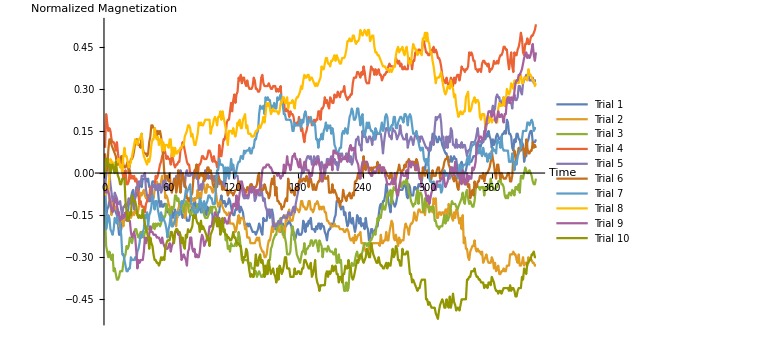

0.188053

```mathematica
magnetism1={-10,-30,-26,-24,-20,-22,-28,-22,-26,-26,-28,-30,-36,-44,-44,-40,-32,-30,-32,-32,-34,-30,-22,-20,-18,-14,-12,-18,-18,-14,-16,-14,-8,-6,-10,-4,-4,-4,-4,-6,-4,-10,-10,-10,-6,-6,-6,-12,-10,-12,-20,-24,-20,-24,-24,-22,-22,-26,-28,-28,-26,-28,-26,-32,-30,-26,-30,-32,-26,-28,-26,-28,-32,-30,-30,-30,-34,-34,-34,-30,-26,-24,-26,-18,-22,-26,-24,-26,-24,-28,-28,-24,-28,-24,-30,-24,-26,-28,-28,-26,-32,-32,-32,-32,-34,-28,-28,-20,-16,-22,-20,-20,-24,-22,-22,-18,-20,-24,-28,-30,-30,-26,-26,-20,-22,-28,-24,-26,-28,-34,-38,-38,-36,-38,-36,-38,-40,-42,-42,-42,-44,-42,-40,-36,-38,-42,-44,-32,-34,-34,-34,-26,-28,-32,-30,-26,-30,-38,-40,-40,-40,-40,-42,-42,-40,-36,-38,-38,-38,-36,-36,-34,-36,-38,-44,-42,-48,-46,-42,-40,-44,-44,-44,-42,-34,-38,-42,-36,-38,-34,-36,-32,-40,-40,-40,-42,-38,-40,-36,-36,-40,-36,-38,-38,-42,-44,-48,-42,-40,-40,-36,-38,-36,-32,-30,-20,-20,-20,-22,-26,-24,-24,-30,-28,-34,-38,-36,-28,-34,-36,-32,-38,-42,-38,-30,-32,-36,-32,-38,-36,-36,-40,-32,-38,-40,-48,-46,-40,-40,-44,-42,-40,-38,-38,-30,-24,-22,-26,-20,-20,-16,-8,-12,-20,-24,-28,-18,-20,-22,-24,-22,-18,-12,-12,-12,-12,-12,-10,-8,-8,-16,-18,-8,-10,-16,-16,-16,-10,-10,-12,-12,-8,-8,-10,-6,0,4,2,8,10,8,18,16,20,28,28,26,26,22,22,26,24,24,20,18,16,14,14,10,8,8,12,8,10,12,10,10,4,-2,-2,0,8,-2,-2,0,2,6,8,8,8,8,10,12,12,12,14,22,20,16,20,22,22,26,24,28,26,30,26,24,18,24,20,22,26,28,26,24,24,26,28,28,30,28,38,36,28,28,26,18,16,24,22,28,28,24,24,18,22,20,8,12,12,22,24,28,30,30,22,22,22,24}/200;
magnetism2={-6,-12,-12,-10,-20,-20,-30,-20,-22,-24,-26,-24,-28,-38,-34,-34,-34,-38,-32,-32,-32,-28,-32,-30,-32,-30,-28,-30,-26,-28,-30,-26,-20,-14,-16,-14,-12,-16,-18,-16,-20,-20,-16,-14,-16,-18,-12,-10,-6,-8,-8,-10,-6,-2,-8,-6,-18,-16,-18,-22,-24,-30,-38,-36,-36,-32,-38,-30,-26,-22,-24,-24,-20,-22,-32,-30,-22,-18,-18,-24,-18,-18,-20,-20,-18,-18,-12,-18,-14,-18,-12,-10,-8,-14,-14,-8,-10,-10,-10,-12,-14,-10,-12,-14,-20,-24,-22,-20,-22,-24,-26,-28,-28,-30,-30,-28,-36,-36,-36,-36,-38,-42,-40,-34,-30,-36,-32,-32,-32,-34,-40,-38,-46,-46,-46,-50,-50,-50,-50,-50,-48,-46,-48,-46,-52,-54,-56,-56,-60,-60,-58,-52,-48,-48,-44,-38,-42,-36,-36,-36,-38,-40,-42,-38,-38,-38,-46,-42,-30,-34,-28,-26,-34,-34,-34,-30,-28,-24,-26,-26,-28,-26,-20,-20,-24,-24,-26,-26,-24,-20,-20,-26,-26,-28,-26,-22,-22,-20,-22,-26,-24,-26,-24,-24,-28,-28,-34,-34,-36,-36,-38,-38,-38,-36,-38,-38,-38,-38,-40,-40,-40,-40,-42,-42,-40,-40,-42,-46,-48,-48,-46,-50,-44,-48,-46,-44,-44,-42,-50,-50,-50,-54,-56,-56,-56,-52,-54,-54,-50,-50,-50,-50,-50,-50,-50,-52,-44,-50,-50,-48,-48,-42,-48,-48,-42,-38,-34,-36,-46,-48,-44,-48,-52,-46,-50,-48,-48,-48,-40,-36,-38,-40,-44,-38,-36,-36,-34,-28,-32,-34,-30,-26,-26,-28,-28,-28,-26,-30,-22,-22,-20,-26,-26,-24,-28,-18,-22,-18,-32,-32,-28,-28,-30,-28,-28,-30,-26,-26,-30,-22,-26,-26,-32,-34,-28,-32,-26,-26,-32,-36,-32,-40,-30,-50,-46,-54,-54,-60,-62,-56,-54,-52,-52,-48,-54,-56,-54,-56,-56,-58,-56,-64,-62,-60,-58,-62,-64,-64,-64,-60,-62,-68,-64,-70,-68,-66,-72,-72,-70,-70,-68,-70,-70,-66,-66,-66,-58,-58,-58,-56,-58,-58,-62,-64,-58,-66,-66,-64,-60,-66,-64,-64,-66,-60,-62,-62,-62,-64,-64,-66,-66}/200;
magnetism3={-30,-52,-56,-60,-56,-60,-62,-58,-70,-68,-72,-76,-76,-74,-70,-70,-70,-64,-60,-58,-52,-54,-52,-46,-48,-50,-46,-42,-40,-40,-44,-46,-44,-42,-42,-44,-46,-42,-42,-38,-40,-40,-40,-40,-38,-36,-40,-36,-38,-36,-36,-38,-36,-30,-32,-32,-30,-22,-26,-26,-30,-28,-24,-26,-24,-16,-16,-20,-18,-22,-22,-22,-26,-28,-24,-20,-22,-22,-28,-28,-30,-26,-24,-30,-30,-28,-22,-24,-24,-24,-24,-24,-30,-32,-32,-32,-30,-28,-24,-28,-24,-24,-24,-26,-32,-34,-38,-36,-36,-40,-42,-40,-48,-46,-54,-52,-56,-50,-52,-52,-52,-50,-52,-50,-42,-46,-54,-62,-60,-62,-62,-62,-62,-64,-66,-64,-68,-68,-68,-72,-70,-74,-72,-70,-72,-74,-74,-72,-74,-72,-68,-64,-62,-62,-54,-52,-48,-46,-44,-44,-36,-38,-36,-32,-38,-44,-42,-46,-50,-58,-58,-58,-56,-44,-38,-42,-46,-52,-58,-60,-62,-64,-60,-56,-56,-50,-58,-54,-54,-52,-52,-48,-48,-52,-50,-48,-48,-52,-56,-48,-50,-52,-60,-54,-54,-54,-56,-52,-54,-56,-56,-56,-58,-58,-54,-64,-64,-58,-64,-62,-74,-78,-84,-84,-78,-84,-82,-70,-68,-64,-66,-66,-62,-58,-56,-60,-62,-60,-58,-56,-52,-50,-50,-52,-50,-52,-48,-48,-46,-44,-42,-44,-38,-32,-34,-30,-32,-26,-22,-26,-26,-22,-16,-14,-16,-12,-22,-14,-10,-12,-12,-14,-14,-10,-6,-10,-8,-6,-6,-8,-4,-8,-14,-16,-20,-22,-24,-22,-22,-16,-12,-22,-14,-14,-16,-26,-28,-18,-22,-24,-24,-28,-24,-26,-24,-24,-34,-34,-38,-38,-40,-38,-38,-38,-34,-30,-36,-30,-34,-32,-30,-24,-20,-22,-22,-22,-24,-26,-24,-22,-20,-18,-14,-20,-22,-14,-12,-18,-22,-20,-22,-24,-24,-20,-12,-8,-10,-10,-12,-10,-10,-10,-16,-10,-12,-10,-8,-12,-4,-8,-10,-12,-12,-10,-10,-6,-6,-4,-8,-8,-10,-16,-18,-16,-18,-14,-14,-16,-12,-14,-16,-10,-10,-12,-8,-14,-2,-2,-4,0,4,2,0,0,2,0,-2,-6,-8,-8,-4}/200;
magnetism4={18,42,36,30,32,30,24,22,22,20,16,22,14,8,10,6,2,-4,0,2,-8,-8,-6,2,-4,-2,-4,-2,-6,-4,-8,-16,-22,-20,-24,-24,-24,-28,-22,-20,-16,-20,-10,-10,-10,-10,-10,-2,-4,-2,2,6,8,12,14,18,14,10,12,10,10,6,14,10,6,4,6,6,8,8,16,18,22,20,16,12,8,6,6,0,0,0,-2,2,2,6,-4,6,6,8,12,12,10,10,10,12,16,16,14,10,8,12,8,8,4,4,20,12,12,18,24,24,28,36,38,38,44,50,44,52,56,50,56,58,68,66,70,64,68,68,64,62,66,62,60,60,60,62,68,66,60,60,58,58,60,68,70,64,62,62,62,62,64,62,60,60,62,62,62,58,60,58,60,62,50,52,52,44,44,46,44,40,44,42,42,40,34,34,36,34,40,36,30,32,26,22,28,30,34,40,38,38,34,36,38,36,38,38,44,44,38,46,46,48,54,50,52,48,46,54,52,50,50,56,54,54,58,56,54,58,58,58,62,56,54,52,54,54,56,56,64,68,68,68,72,72,70,68,72,70,76,72,66,64,64,64,70,76,74,74,70,74,70,72,74,70,70,66,68,70,70,72,72,76,78,76,76,76,76,76,82,80,78,80,76,78,74,74,76,74,74,74,82,80,80,74,80,80,86,86,86,88,88,86,86,94,94,90,86,86,84,84,86,88,86,90,86,88,86,82,82,80,76,70,66,66,64,68,64,62,64,68,66,62,68,64,68,70,70,66,70,76,74,74,72,74,74,76,86,84,86,84,80,80,74,74,72,74,74,72,78,80,80,78,78,76,78,72,74,74,76,80,78,78,80,78,82,84,84,86,90,90,88,88,80,74,80,86,76,72,86,84,84,88,90,94,100,96,86,84,92,92,96,92,92,96,98,98,100,102,106}/200;
magnetism5={-10,-2,4,6,0,-8,-14,-20,-20,-14,-16,-18,-22,-22,-20,-26,-30,-24,-24,-22,-24,-22,-18,-22,-18,-18,-22,-26,-16,-10,-10,-6,-6,-8,-2,-2,-2,0,-12,-16,-16,-20,-20,-18,-8,-10,-8,-12,-10,-8,-12,-8,-14,-12,-6,-6,-4,-12,-8,-12,-8,-12,-12,-10,-4,-8,-2,-2,-2,-6,2,-2,0,-6,-10,0,2,-2,-2,-2,0,0,-4,0,0,-4,-2,-12,-12,-8,-12,-6,-4,2,-4,0,-4,-2,-4,-2,-2,-6,-2,-2,-2,0,-8,-6,-6,-10,-6,-10,-4,2,0,0,2,2,4,4,-4,-2,-2,-2,-8,-12,-6,-8,-16,-18,-18,-16,-18,-18,-14,-12,-8,-10,-12,-20,-18,-14,-14,-16,-16,-8,-16,-20,-18,-24,-26,-30,-26,-26,-28,-30,-38,-36,-38,-38,-36,-34,-36,-36,-32,-32,-30,-32,-32,-32,-28,-28,-30,-30,-26,-24,-28,-22,-18,-14,-10,-6,-2,2,0,2,6,10,12,12,10,12,6,6,12,10,8,12,12,6,2,8,6,2,-2,4,10,10,8,10,12,10,8,10,6,8,2,6,14,12,14,10,10,10,14,10,14,8,12,6,8,14,16,24,24,26,20,20,16,30,26,26,26,22,22,26,26,24,20,26,24,24,28,28,28,28,28,22,14,22,28,32,32,30,26,26,24,32,30,30,28,24,26,28,34,28,26,24,24,24,28,18,22,24,26,24,20,24,28,28,24,26,22,26,26,24,22,20,18,18,16,16,22,22,24,20,32,40,38,40,40,42,36,24,26,18,18,26,18,26,22,32,30,20,20,18,24,18,20,20,18,22,18,20,20,16,12,16,16,18,22,22,22,22,24,28,32,24,22,22,24,22,30,28,34,36,36,38,40,44,48,44,46,54,56,54,54,48,50,52,54,48,48,50,52,50,50,50,46,54,56,52,52,54,62,62,58,56,64,66,68,70,68,70,66,66,66,68,64,66,66}/200;
magnetism6={14,2,2,16,24,24,20,18,16,14,12,6,6,6,8,12,12,6,4,4,6,8,0,6,10,10,12,16,22,24,24,20,20,18,28,18,14,14,14,12,14,22,26,34,34,32,32,30,26,30,28,30,26,18,12,0,-4,-2,-2,-6,0,-10,-14,-10,-6,-4,-14,-10,2,-6,-14,-6,0,-4,-8,-10,-18,-18,-20,-18,-16,-14,-4,-2,2,6,2,-4,-2,0,-2,0,-6,-4,0,4,4,0,2,-2,-8,-10,-8,-4,-10,-2,-4,-6,-8,-12,-10,-12,-12,-12,-16,-14,-12,-14,-14,-16,-14,-12,-12,-12,-6,-10,-12,-10,-10,-12,-12,-14,-10,-12,-10,-8,-8,-10,-12,-10,-10,-8,-2,0,-10,-12,-12,-12,-8,-10,-14,-14,-18,-16,-8,-4,-8,-2,-16,-10,-20,-20,-22,-22,-26,-24,-24,-20,-18,-20,-4,-10,-12,-14,-12,-14,-16,-10,-12,-10,-6,-4,-6,-6,-4,-4,-6,-2,-4,-10,-4,-4,-8,-12,-8,-12,-12,-8,-6,-6,0,-4,-6,0,-4,-4,-4,-2,-14,-14,-14,-8,-14,-12,-14,-16,-20,-18,-24,-20,-20,-12,-16,-18,-20,-16,-16,-14,-18,-18,-14,-16,-6,-6,-4,0,-4,0,-2,-2,12,4,2,8,4,4,2,4,0,4,4,4,4,8,0,4,4,4,4,2,2,0,-2,-2,-4,0,0,-8,-6,-6,-4,0,2,6,2,0,2,2,6,4,8,8,10,8,8,8,8,8,2,10,8,4,-2,0,-4,4,0,-2,0,2,2,0,-6,-4,2,-2,-2,-2,2,4,4,-4,0,2,4,8,10,10,12,6,4,0,-2,-4,-6,-2,-4,-10,-12,-6,-4,0,-2,-6,-8,-8,-6,-10,-8,-18,-14,-12,-16,-6,-10,-10,-6,-6,-2,-2,-4,0,-6,-2,0,0,2,4,8,16,10,6,0,-4,6,6,0,-4,0,-2,-4,-4,-4,-2,0,0,-6,-6,-2,12,16,12,8,14,18,16,16,18,18,16,12,24,18,14,14,16,16,22,18,20,18}/200;
magnetism7={-12,-40,-36,-30,-32,-40,-42,-44,-40,-32,-34,-36,-26,-32,-38,-44,-58,-58,-62,-66,-70,-70,-68,-68,-60,-62,-62,-62,-60,-62,-56,-54,-50,-44,-46,-42,-40,-30,-32,-28,-38,-30,-28,-24,-16,-20,-26,-20,-20,-26,-30,-34,-28,-34,-32,-34,-36,-40,-46,-40,-36,-30,-38,-38,-36,-34,-28,-28,-28,-30,-26,-20,-22,-20,-18,-12,-14,-12,-10,-8,-22,-22,-26,-28,-30,-26,-28,-24,-18,-20,-28,-22,-20,-26,-22,-20,-16,-16,-18,-18,-22,-22,-22,-10,2,2,10,6,6,6,4,-6,4,-2,4,-4,2,10,4,6,0,-2,2,6,8,8,12,12,10,16,14,16,16,16,18,14,14,18,18,24,24,28,30,42,48,46,46,48,42,54,52,54,52,52,46,48,46,50,46,46,54,52,54,56,52,48,42,42,38,38,38,38,38,36,30,30,36,34,34,34,34,38,32,38,36,42,44,40,34,36,38,40,36,34,36,34,24,24,18,24,24,28,24,30,32,36,30,34,32,34,28,32,28,20,18,14,14,16,18,18,28,30,28,32,30,28,34,40,42,46,44,38,38,40,46,46,40,34,40,42,30,26,30,36,32,36,32,30,30,28,24,32,30,28,28,28,32,36,30,32,40,42,40,32,30,32,34,34,40,40,32,32,36,38,40,40,38,36,42,42,40,34,40,42,40,34,28,28,28,30,26,22,18,16,18,18,10,8,10,6,10,-4,-6,-6,-8,-6,-12,-8,-10,-8,-10,-8,-14,-12,-2,2,-2,0,-2,-4,-4,4,2,4,0,2,0,-2,-4,6,6,0,4,6,6,6,10,12,6,14,18,20,20,22,22,16,18,14,18,14,12,18,14,12,14,8,12,14,10,14,18,16,16,14,24,22,22,18,26,18,16,16,16,16,16,8,8,8,14,10,2,8,6,12,14,16,18,24,30,30,30,30,36,36,34,36,38,36,30,32,32}/200;
magnetism8={-16,-10,-10,-10,-4,10,8,8,4,0,6,8,10,10,4,6,0,12,18,12,12,8,4,6,8,12,16,20,24,22,20,24,24,26,28,16,12,10,8,6,10,8,12,20,24,24,32,26,24,26,20,24,24,16,22,16,20,20,20,18,24,24,12,18,12,18,14,14,16,16,18,18,20,20,26,28,30,34,34,32,26,28,24,20,20,24,28,36,34,36,34,34,36,38,38,38,38,38,28,32,34,38,40,38,34,40,40,44,38,44,40,36,32,26,20,30,30,30,28,32,28,26,30,36,34,38,32,32,38,40,42,32,34,28,28,28,26,26,26,28,30,30,32,34,32,34,36,40,36,42,50,48,50,46,42,44,46,44,44,44,44,42,44,50,50,54,54,50,50,54,46,50,50,50,52,50,46,52,54,54,56,58,62,60,66,70,68,68,70,70,66,68,68,66,64,62,64,62,64,66,68,76,74,74,78,82,82,78,78,76,80,80,82,84,80,84,82,80,78,78,82,82,82,84,88,94,94,96,94,94,98,98,94,92,94,94,96,102,100,98,100,102,100,98,102,102,94,96,98,98,90,86,86,84,84,82,80,78,76,76,76,74,74,74,72,74,72,74,76,76,84,88,90,86,88,88,90,86,84,88,90,84,78,80,78,86,92,90,88,88,84,86,86,86,84,96,96,100,94,100,94,92,86,86,80,76,70,64,68,68,68,70,72,66,62,58,56,58,62,62,60,66,62,60,54,56,48,44,40,42,44,42,42,44,44,54,56,58,44,44,46,50,52,54,50,52,52,50,40,38,42,42,42,32,38,40,36,40,40,36,38,38,38,36,36,46,50,48,48,48,54,48,50,60,58,56,58,64,62,60,66,66,64,66,64,70,70,64,64,68,68,68,66,74,70,70,68,66,66,62,64}/200;
magnetism9={-12,-14,-12,-14,-16,-22,-26,-28,-24,-20,-18,-22,-30,-28,-34,-32,-30,-32,-30,-28,-32,-34,-34,-34,-42,-46,-44,-42,-46,-56,-68,-62,-64,-62,-62,-62,-56,-46,-50,-46,-48,-44,-38,-42,-42,-44,-44,-44,-46,-46,-46,-48,-50,-46,-50,-52,-54,-54,-54,-52,-50,-56,-52,-50,-48,-42,-42,-42,-44,-42,-52,-62,-60,-58,-60,-62,-66,-56,-54,-46,-46,-54,-56,-54,-60,-58,-60,-60,-56,-48,-44,-46,-52,-50,-48,-46,-44,-38,-38,-38,-32,-34,-28,-30,-30,-38,-32,-38,-34,-34,-36,-32,-34,-36,-36,-32,-30,-28,-28,-22,-22,-24,-16,-26,-20,-14,-12,-6,-10,-12,-16,-16,-16,-16,-12,-10,-14,-10,-10,-12,-16,-12,-14,-12,-10,-6,2,4,4,4,6,6,6,4,4,2,0,0,0,0,-2,0,-2,-4,-2,-2,6,0,4,12,6,6,2,6,12,12,14,10,10,6,4,10,4,2,4,8,8,2,2,2,-4,0,-2,4,6,8,6,8,10,6,4,-6,-4,0,6,4,4,8,6,6,10,2,16,16,14,14,14,10,12,8,10,10,10,12,10,8,14,18,20,16,18,16,18,10,8,6,0,-4,4,8,8,8,8,8,6,0,0,-2,-2,2,0,0,2,4,4,6,2,0,4,4,-2,-4,-8,-8,-8,-8,-6,-4,-8,0,-10,-16,-16,-10,-6,0,0,-2,-2,-2,2,-4,8,8,4,8,6,6,4,2,6,2,-4,-4,-10,-10,-10,-12,-16,-20,-16,-22,-18,-14,-12,-8,-8,-12,-6,-6,-6,-6,-4,-4,0,-6,-10,-8,-6,-2,0,4,4,0,-2,8,2,0,-2,0,-6,-8,2,-2,-8,-8,0,-6,-2,-4,-4,4,2,4,8,20,22,24,26,26,24,24,26,32,36,40,44,44,44,40,42,44,38,36,40,44,40,40,42,40,36,42,42,52,54,54,50,54,52,52,58,64,66,66,70,70,72,74,78,82,84,86,82,84,82,84,88,92,84,80,86}/200;
magnetism10={-2,10,10,6,6,0,6,6,2,0,8,2,-2,-4,-8,-8,-4,-4,-4,-20,-28,-34,-34,-28,-30,-16,-18,-20,-20,-24,-30,-32,-30,-32,-32,-26,-32,-36,-40,-42,-46,-54,-46,-50,-52,-58,-62,-62,-64,-64,-66,-64,-60,-62,-60,-62,-54,-50,-48,-48,-48,-42,-42,-46,-50,-42,-40,-40,-42,-42,-44,-50,-46,-52,-54,-44,-46,-40,-42,-42,-40,-38,-30,-32,-30,-34,-36,-36,-42,-34,-40,-38,-40,-42,-44,-48,-46,-52,-44,-42,-40,-36,-32,-32,-38,-32,-34,-44,-38,-32,-40,-42,-44,-44,-46,-46,-48,-48,-46,-42,-46,-46,-50,-50,-50,-52,-52,-58,-64,-60,-60,-54,-56,-64,-70,-74,-72,-74,-74,-66,-58,-66,-66,-60,-58,-64,-62,-66,-74,-66,-72,-72,-62,-68,-72,-70,-68,-72,-74,-78,-68,-76,-66,-68,-72,-70,-66,-60,-60,-68,-68,-68,-74,-74,-74,-74,-68,-72,-72,-70,-70,-72,-72,-68,-68,-62,-62,-64,-66,-68,-68,-64,-74,-72,-68,-62,-74,-78,-80,-84,-80,-80,-80,-80,-80,-72,-70,-74,-70,-72,-70,-66,-70,-68,-66,-72,-72,-78,-74,-74,-78,-72,-72,-66,-68,-68,-62,-68,-68,-74,-76,-74,-70,-66,-62,-64,-60,-58,-58,-62,-64,-62,-60,-54,-56,-60,-60,-50,-54,-58,-60,-62,-64,-64,-60,-64,-66,-66,-68,-68,-66,-64,-68,-64,-66,-66,-60,-54,-60,-58,-52,-54,-62,-62,-66,-66,-54,-58,-58,-58,-56,-56,-64,-72,-72,-78,-76,-78,-80,-82,-84,-82,-82,-78,-76,-76,-76,-76,-90,-90,-94,-92,-94,-96,-96,-96,-96,-100,-102,-104,-98,-94,-92,-90,-92,-96,-96,-90,-94,-96,-88,-96,-92,-86,-92,-94,-98,-96,-96,-98,-94,-90,-90,-90,-90,-90,-76,-76,-74,-74,-70,-70,-70,-68,-72,-74,-74,-76,-76,-78,-78,-78,-82,-80,-80,-82,-78,-78,-80,-74,-76,-78,-82,-84,-84,-86,-84,-84,-86,-84,-82,-82,-82,-82,-82,-84,-80,-84,-82,-82,-84,-88,-88,-84,-82,-82,-82,-74,-76,-68,-70,-72,-64,-64,-62,-62,-58,-58,-56,-60,-60}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT15=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### Large Lattice: 200 long, kT=1.75, 400 time steps

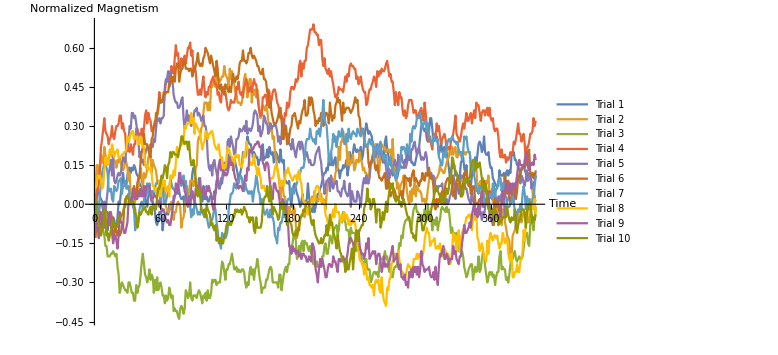

0.180907

```mathematica
magnetism1={-4,2,12,10,6,4,2,-6,-16,-14,-16,-20,-10,-8,-8,-16,-10,-12,-18,-18,-10,2,0,8,16,24,16,16,14,22,28,28,24,28,26,30,28,24,22,22,16,14,14,8,8,8,0,-2,6,8,8,4,2,-2,-6,-14,-16,-12,-6,-6,-8,-20,-12,-8,-8,-6,-8,0,-4,-2,-2,2,6,8,12,14,10,6,4,4,6,-6,8,10,6,6,-2,14,24,28,26,14,14,10,20,6,6,2,14,4,4,6,2,2,6,6,4,4,10,8,18,20,16,14,16,16,28,26,28,26,28,38,34,34,36,26,34,32,28,24,18,22,26,30,40,40,36,38,52,48,46,46,42,36,40,38,36,36,30,34,34,44,46,34,36,36,42,36,44,40,38,40,32,36,40,38,34,32,42,34,32,34,18,18,16,16,18,4,-2,12,14,16,12,8,6,2,-2,2,8,0,2,2,4,16,6,0,2,-6,0,-6,-2,4,8,8,12,14,18,22,24,24,28,26,36,30,40,30,30,34,36,26,28,26,20,26,26,30,28,30,34,22,28,40,36,32,40,46,42,40,42,40,38,44,34,38,46,56,62,58,54,56,54,52,44,44,42,40,36,36,36,42,40,38,38,48,52,42,38,32,30,30,22,28,22,18,20,24,30,30,28,28,28,34,32,42,36,36,40,32,32,30,30,34,38,40,44,52,60,62,58,56,58,50,48,56,66,66,58,48,50,50,52,46,38,42,48,40,40,44,42,40,34,28,20,26,30,28,30,22,24,22,18,22,32,34,36,28,24,30,16,16,18,14,22,30,24,36,30,38,46,48,46,40,42,52,40,38,38,40,32,28,28,20,18,16,14,14,14,26,22,22,22,24,18,24,26,22,26,24,38,38,40,34,34,30,30,26,22,28,28,30,26,24,18,22,24,22,18,12,2,6,6}/200;
magnetism2={14,30,30,18,26,38,32,32,44,38,34,32,34,38,38,38,34,34,32,28,34,32,36,32,26,26,28,36,32,28,18,24,8,8,4,0,2,12,6,12,22,28,20,12,24,20,22,28,36,38,36,24,34,30,28,26,18,16,16,16,20,18,14,10,-2,-4,-6,-6,0,2,-6,-12,-6,-6,0,2,0,-2,-18,-12,-10,-4,2,14,8,8,18,18,18,14,18,28,30,48,52,50,58,60,70,78,78,78,72,78,72,90,90,96,92,90,98,98,96,94,96,98,98,106,100,98,96,90,104,96,102,96,92,86,86,78,78,78,76,78,86,96,100,94,82,90,96,96,78,88,84,88,82,88,80,72,66,72,76,74,72,76,72,64,62,56,58,50,52,40,36,28,24,16,4,18,16,6,6,0,0,-12,-2,-6,-6,-8,-2,-4,-16,-26,-22,-16,-12,-8,-8,-8,-10,-6,-2,-2,-4,0,4,6,2,10,6,4,2,4,6,8,0,4,2,-4,8,16,16,20,16,20,18,16,24,26,28,44,34,48,48,56,46,48,46,30,40,30,32,34,38,26,28,34,34,32,40,34,32,26,28,24,24,22,16,28,32,32,38,44,46,46,38,24,26,42,46,44,44,42,40,42,42,40,42,32,50,32,24,26,12,16,8,14,16,18,22,16,18,10,4,0,10,2,12,8,20,6,14,12,10,10,8,2,4,4,0,4,12,18,24,20,20,18,14,20,20,22,24,30,26,26,24,24,28,32,34,36,44,38,44,38,42,44,36,36,42,38,40,36,40,40,38,40,40,40,40,32,30,28,30,32,28,14,12,16,18,12,20,14,8,18,16,22,8,8,6,2,0,2,2,-6,-16,-12,-6,-16,-4,-4,-14,-18,-24,-26,-28,-44,-40,-24,-22,-20,-14,-12,-6,-12,-12,-14,-10,-6,-6,-14,-14,-10,-14,0,4,2,16,4,2}/200;
magnetism3={-18,4,-2,-8,-6,-12,-18,-20,-24,-32,-32,-40,-40,-40,-38,-38,-36,-38,-40,-38,-48,-54,-68,-64,-60,-62,-64,-66,-66,-68,-60,-60,-64,-68,-68,-74,-74,-62,-68,-64,-62,-54,-44,-38,-46,-54,-56,-60,-56,-50,-58,-54,-56,-68,-58,-66,-56,-66,-62,-60,-64,-70,-70,-76,-70,-74,-72,-64,-68,-72,-70,-82,-80,-82,-82,-86,-88,-80,-78,-80,-84,-80,-66,-68,-72,-70,-60,-72,-74,-70,-70,-70,-72,-68,-66,-68,-72,-76,-70,-72,-68,-74,-66,-72,-72,-68,-58,-60,-58,-58,-62,-60,-60,-60,-52,-44,-46,-52,-58,-50,-50,-46,-46,-42,-38,-44,-50,-50,-48,-52,-50,-52,-52,-50,-50,-52,-60,-64,-60,-62,-52,-48,-54,-50,-58,-50,-48,-42,-48,-56,-60,-68,-64,-64,-64,-58,-58,-54,-50,-48,-50,-60,-60,-60,-60,-60,-64,-54,-54,-66,-60,-54,-50,-48,-52,-46,-46,-32,-34,-30,-24,-24,-28,-42,-40,-32,-38,-30,-28,-36,-28,-30,-30,-34,-36,-32,-38,-36,-46,-44,-48,-44,-48,-48,-46,-48,-40,-40,-32,-30,-38,-38,-32,-24,-26,-30,-22,-18,-18,-16,-24,-20,-10,-12,-14,-6,-12,-14,-20,-20,-20,-30,-18,-22,-22,-22,-22,-36,-34,-30,-34,-36,-44,-48,-44,-44,-42,-50,-50,-50,-60,-58,-54,-52,-52,-54,-52,-56,-46,-42,-42,-42,-40,-36,-42,-40,-48,-52,-46,-56,-56,-50,-48,-48,-46,-38,-30,-32,-24,-26,-18,-14,-12,-12,-10,-12,-14,-20,-10,-4,-2,0,-6,-6,-8,-10,-8,-12,-12,-4,-6,-12,0,-10,-8,-10,-20,-12,-12,-16,-10,-20,-14,-12,-4,-2,-4,-4,-6,-2,-6,-4,-12,-22,-18,-24,-22,-26,-22,-28,-36,-28,-38,-36,-40,-48,-52,-56,-54,-50,-48,-46,-46,-58,-52,-48,-52,-50,-40,-52,-50,-42,-36,-40,-48,-54,-60,-56,-52,-54,-52,-56,-54,-62,-56,-52,-52,-40,-36,-50,-48,-50,-50,-58,-56,-60,-54,-46,-42,-42,-38,-36,-42,-44,-42,-40,-42,-42,-40,-34,-26,-24,-22,-30,-32,-16,-8,-14,-20,-10,-2}/200;
magnetism4={2,12,10,16,28,44,50,58,66,56,54,52,46,50,52,60,52,50,56,60,60,62,68,68,58,62,56,54,40,46,42,40,46,42,38,46,46,58,58,54,54,52,58,52,58,68,72,62,70,66,64,56,56,60,64,64,70,76,86,78,80,80,78,86,94,94,94,96,98,106,104,100,112,122,114,116,104,106,112,106,110,114,108,114,120,120,124,114,118,102,106,102,92,84,84,88,84,92,98,88,82,86,84,90,90,94,96,98,94,92,92,84,86,80,78,88,90,86,86,80,74,72,74,80,78,78,78,82,90,88,94,86,84,86,82,90,92,96,92,86,88,90,86,92,96,92,92,84,76,70,68,68,82,82,84,84,76,88,86,78,80,86,88,88,84,78,76,72,66,68,58,56,70,68,78,74,76,86,90,90,88,90,96,94,96,106,110,98,108,104,110,110,120,122,128,134,134,134,138,132,132,130,130,122,126,126,112,106,112,104,102,100,104,98,102,96,92,86,82,84,84,90,88,88,88,86,92,98,94,100,98,106,108,106,106,104,104,96,98,92,94,98,92,88,86,86,76,78,84,88,88,92,94,98,96,90,102,98,102,100,104,102,102,104,108,110,104,98,100,94,94,86,76,86,80,76,86,82,82,72,68,72,66,68,76,80,80,80,76,70,72,72,66,68,70,72,74,68,64,78,70,60,50,48,52,46,42,52,54,52,62,56,60,52,46,50,52,54,50,42,42,44,42,48,50,54,60,68,54,52,50,48,52,58,62,58,64,70,64,64,68,70,62,68,72,66,78,76,76,70,64,70,72,72,68,72,74,68,74,66,64,66,58,56,58,58,52,40,36,42,36,36,38,32,36,34,36,40,38,40,48,46,50,56,62,54,54,48,50,54,46,30,44,44,48,54,54,56,66,60,64}/200;
magnetism5={-2,2,-6,-8,0,0,0,-4,2,-6,2,10,24,28,34,22,36,18,16,18,22,24,22,24,30,36,34,32,44,44,48,60,58,70,70,66,68,62,56,48,36,40,32,34,30,38,42,44,42,42,46,44,44,50,48,58,66,64,66,62,66,66,68,90,96,96,102,90,102,96,94,84,80,78,78,74,74,76,80,82,66,58,64,72,64,68,62,60,64,66,72,72,74,68,70,68,64,66,68,60,60,54,36,28,26,30,22,32,34,28,24,20,12,12,20,18,24,32,26,30,48,50,44,52,48,44,38,38,50,50,52,58,56,56,58,60,56,64,54,58,58,56,58,62,70,72,70,68,56,60,52,54,58,68,66,62,62,54,58,62,58,60,60,62,60,56,48,52,46,52,66,62,60,60,50,54,46,46,42,50,44,40,36,42,46,48,42,48,46,40,34,38,40,36,32,34,30,30,30,32,38,40,42,44,36,32,22,18,8,14,18,18,20,10,22,14,12,16,16,18,10,10,8,6,12,12,18,10,8,6,8,16,-2,10,6,2,2,2,10,8,4,-2,8,16,20,16,22,16,16,20,30,32,36,38,36,40,46,42,42,40,36,32,32,34,28,18,28,20,26,24,30,30,34,30,24,38,32,36,38,32,32,28,28,32,36,34,34,42,42,46,48,42,38,42,44,38,34,36,34,36,40,36,22,24,24,24,20,22,18,12,10,12,14,14,14,16,6,4,0,4,0,2,6,8,14,22,18,4,16,14,8,10,22,22,20,20,12,12,8,4,2,0,14,2,4,-8,-4,-4,0,-6,-6,-12,-6,-10,-2,4,0,4,0,-8,-4,-12,-2,8,4,-2,6,6,2,8,6,4,-10,-4,2,4,8,14,12,2,2,16,12,16,20,22,16,22,20,16,14,20,26,18,22,24,12,14,16,18,26}/200;
magnetism6={-26,-14,-10,-16,-10,-6,-10,-12,-4,-6,-6,-6,-12,-16,-6,-12,-26,-24,-18,-20,-24,-20,-24,-22,-16,-18,-4,4,4,6,8,2,0,6,6,14,6,6,16,20,20,34,40,44,54,46,46,46,42,38,36,50,52,60,60,70,68,72,82,78,78,80,86,84,86,86,86,92,92,98,94,98,94,104,108,108,94,100,104,104,110,110,104,104,104,102,104,104,98,102,102,106,110,116,108,106,108,106,112,114,120,118,116,112,108,114,110,106,102,98,110,104,90,88,92,86,88,84,92,90,88,86,90,86,94,100,94,94,98,96,100,108,110,110,118,110,110,108,110,116,116,120,114,112,114,112,110,106,106,102,100,100,104,96,96,94,86,86,74,78,70,66,62,62,62,64,68,72,74,66,50,50,58,60,46,48,52,58,60,68,68,70,66,62,58,64,62,68,72,74,80,68,68,70,82,76,82,80,72,68,60,64,62,66,64,70,66,60,64,70,70,68,62,78,70,64,68,66,76,78,82,78,80,72,64,78,70,72,74,74,74,72,70,72,74,78,82,78,80,68,66,56,54,58,50,46,44,46,32,28,32,34,38,36,28,26,30,24,20,20,18,20,22,24,12,12,20,14,6,8,10,12,10,6,4,4,6,8,10,4,12,22,20,20,18,20,14,20,24,26,18,20,18,16,14,18,18,24,20,18,24,22,22,28,20,20,20,14,-2,-4,4,-2,4,2,8,10,6,8,16,18,20,20,16,22,20,6,6,12,18,20,18,12,6,14,16,24,22,26,18,14,16,8,12,12,14,2,0,0,2,4,2,12,18,18,12,12,8,4,10,6,10,12,12,-4,2,2,2,-6,-2,0,6,14,22,14,8,18,8,0,2,10,12,14,4,10,22,20,26,26,28,30,28,32,30,40,42,24,22,24,20,24,20}/200;
magnetism7={-10,-14,-4,-4,8,16,24,28,32,30,28,24,10,10,12,4,2,14,12,10,12,18,18,20,8,14,14,18,12,12,14,6,2,6,-2,-4,-20,-14,-14,-10,-4,0,2,-4,2,12,6,16,8,16,8,10,10,6,12,16,16,18,14,2,12,18,0,2,2,6,10,12,20,16,12,12,10,10,14,12,22,18,14,16,22,12,18,8,2,0,-2,-10,-4,-8,2,0,-4,-8,-6,-8,-2,-6,-8,-10,-8,-8,-14,-18,-16,-12,-12,-8,-2,-4,-14,-20,-30,-30,-34,-22,-24,-24,-26,-24,-20,-4,2,8,8,10,16,14,12,16,16,20,22,20,12,10,16,12,10,8,10,8,10,2,10,14,22,18,10,8,0,4,0,-6,-8,-6,-4,-10,-10,-4,-10,-10,-14,-24,-26,-30,-18,-20,-14,-14,-10,-4,-10,-4,2,4,4,6,12,12,8,12,14,16,24,22,24,28,28,28,34,46,50,50,50,58,52,50,48,50,46,56,54,58,52,60,68,80,66,62,60,48,34,32,40,44,54,48,52,44,50,56,52,52,58,54,48,46,54,48,58,52,50,54,56,54,54,52,58,56,54,52,58,56,52,46,44,44,48,50,46,46,48,34,44,42,44,38,46,48,40,36,34,38,38,28,30,32,36,30,26,24,22,20,24,28,26,34,44,42,44,42,38,46,40,38,54,48,58,60,58,60,66,68,66,70,62,58,62,62,64,56,62,52,50,48,46,52,50,50,48,50,36,34,30,30,40,40,36,44,48,50,48,50,52,50,48,48,46,48,40,40,40,34,40,52,50,52,44,40,40,26,30,28,22,18,10,12,8,14,12,12,10,6,0,0,4,6,8,6,4,16,14,6,12,12,18,20,20,10,16,16,6,6,-2,-2,-2,0,2,6,2,-6,-18,-6,-4,-6,0,-4,8,14,8,-4,6,2,4,-6,0,0,6,14,22}/200;
magnetism8={12,16,22,20,22,18,12,14,26,36,36,30,36,42,38,46,42,36,40,40,42,36,36,36,38,38,40,40,42,52,48,50,54,56,56,50,52,50,52,46,46,52,48,44,44,32,28,30,26,28,28,24,14,14,10,12,6,12,18,6,12,18,14,18,10,10,14,6,22,22,20,26,22,32,44,38,40,46,46,46,50,60,58,62,62,62,62,70,62,66,54,62,60,58,56,54,48,42,46,48,56,54,50,54,54,56,56,52,46,44,42,42,46,38,34,36,26,30,28,34,44,42,40,36,36,28,30,38,36,36,38,30,30,28,34,40,36,48,44,40,30,32,30,32,38,30,28,22,28,24,20,12,14,14,10,12,8,6,6,20,20,20,22,28,30,28,22,20,14,16,18,14,18,26,24,28,24,22,20,18,20,22,22,18,24,26,18,16,6,2,2,-4,-4,-8,0,-2,-2,4,2,6,12,14,14,12,6,2,4,2,0,-8,-10,-14,-20,-18,-14,-8,-4,-10,0,-6,-6,-6,-10,-14,-8,-12,-6,-12,-8,-10,-16,-12,-16,-14,-14,-12,-16,-22,-30,-36,-42,-44,-44,-46,-54,-46,-52,-58,-56,-62,-62,-64,-62,-70,-60,-58,-60,-58,-66,-68,-56,-68,-74,-76,-78,-64,-66,-58,-56,-46,-44,-42,-38,-40,-40,-36,-42,-48,-52,-52,-54,-58,-54,-50,-46,-48,-48,-52,-52,-42,-42,-42,-38,-42,-38,-40,-42,-40,-36,-28,-22,-18,-22,-22,-32,-30,-28,-28,-26,-34,-34,-32,-34,-30,-36,-40,-34,-34,-36,-38,-38,-40,-46,-44,-34,-22,-28,-24,-36,-26,-20,-36,-26,-22,-20,-18,-14,-10,-10,-8,-8,-12,-20,-10,-6,-12,-8,-26,-28,-36,-34,-30,-34,-42,-42,-44,-28,-38,-26,-22,-26,-28,-24,-24,-26,-24,-30,-34,-30,-30,-22,-26,-30,-26,-26,-38,-42,-44,-38,-56,-56,-52,-52,-46,-52,-52,-44,-42,-36,-20,-28,-16,-12,-4,-6,-2,0,0,-4,4,-8}/200;
magnetism9={2,-18,-18,-26,-10,-18,-8,-14,-18,-14,-22,-16,-10,-6,-16,-22,-30,-26,-24,-28,-34,-24,-6,-14,-14,-18,-22,-22,-18,-14,2,2,4,2,12,6,4,4,4,10,6,12,6,6,14,6,14,14,14,14,6,2,4,8,6,6,4,2,-2,2,-6,-4,-4,-8,-12,-14,-12,-16,-16,-10,-4,6,6,16,14,8,24,24,16,18,16,10,8,0,-2,4,0,6,10,4,2,12,12,12,14,20,8,10,12,6,6,14,10,14,10,8,0,-4,-4,10,14,22,30,34,26,26,26,22,24,22,24,28,36,30,32,30,24,20,18,14,12,14,14,12,10,16,22,18,28,26,42,40,42,42,44,46,46,48,48,44,44,40,32,30,26,32,32,30,20,12,8,4,16,16,12,10,10,4,-2,0,4,2,-2,-2,-10,-16,-32,-34,-38,-32,-36,-34,-38,-36,-36,-40,-38,-42,-38,-38,-40,-40,-44,-44,-40,-42,-44,-30,-32,-36,-50,-54,-60,-50,-42,-48,-42,-46,-50,-56,-56,-50,-46,-46,-48,-48,-40,-44,-44,-48,-52,-42,-42,-44,-42,-40,-44,-42,-42,-38,-30,-26,-26,-28,-30,-36,-28,-28,-28,-20,-32,-36,-38,-38,-42,-38,-30,-34,-26,-42,-40,-38,-36,-38,-36,-46,-40,-38,-38,-44,-52,-48,-40,-48,-46,-48,-46,-44,-40,-36,-32,-44,-42,-42,-38,-48,-50,-46,-56,-56,-58,-54,-62,-60,-64,-52,-56,-50,-56,-48,-52,-48,-54,-48,-56,-50,-36,-46,-48,-52,-50,-50,-50,-48,-54,-56,-56,-52,-58,-48,-56,-62,-48,-38,-40,-36,-32,-42,-42,-38,-40,-46,-42,-42,-42,-32,-38,-36,-42,-44,-46,-40,-40,-30,-24,-16,-22,-22,-20,-18,-14,-18,-8,-4,2,-8,-4,-10,-2,-8,2,10,-2,-2,0,0,10,2,-8,-12,-12,-16,-14,-10,-6,-8,-12,-8,-10,2,10,4,8,18,14,10,14,16,8,16,12,14,16,22,30,34,30,30,30,28,34,38,40,28,26,32,30,32,30,38,34}/200;
magnetism10={4,-8,-10,-14,-18,-24,-20,-18,-6,-4,-24,-22,-28,-24,-20,-14,-12,-18,-16,-18,-16,-10,-10,-10,-8,-6,-2,-2,6,6,4,0,0,2,2,0,-4,-10,-18,-14,-6,-8,-6,-4,-4,-2,-6,-6,-8,-4,-2,-8,0,-2,-2,-4,6,12,12,16,22,20,24,30,28,20,30,32,40,36,40,40,38,38,38,36,42,44,52,52,48,46,48,48,42,48,36,30,30,34,28,20,8,6,12,8,-4,-6,-6,-4,-10,0,-4,-6,-8,-16,-14,-18,-20,-16,-28,-24,-26,-30,-26,-30,-30,-24,-22,-16,-14,-16,-14,-16,-14,-8,-10,-4,-6,-4,-6,-6,-4,-8,-6,-2,-4,-6,-10,-10,-14,-10,-12,-10,-20,-22,-10,-18,-18,-18,-18,-14,-2,4,6,6,14,6,2,14,0,-8,-2,-4,-6,-8,-12,-10,0,2,-4,0,-4,-10,-16,-12,-12,-14,-16,-22,-24,-24,-20,-24,-18,-20,-10,-10,-8,-4,-6,0,0,2,0,-8,-14,-16,-12,-20,-24,-26,-28,-30,-30,-26,-30,-28,-24,-24,-16,-24,-16,-8,-16,-14,-22,-24,-28,-34,-24,-30,-36,-38,-42,-44,-44,-52,-42,-50,-50,-44,-40,-34,-50,-38,-28,-20,-28,-22,-20,-18,-16,-16,-4,0,2,12,2,4,-4,-2,4,4,-2,-14,-4,-4,-4,-18,-14,-6,-12,-6,2,-6,4,10,16,12,16,6,4,2,4,6,0,2,-2,2,4,0,-4,-8,-10,-10,-16,-22,-22,-26,-24,-28,-16,-10,-12,-12,-12,-20,-20,-16,-14,-8,-8,-6,-12,-4,0,4,8,12,14,10,8,6,0,8,0,0,6,12,8,12,22,18,36,34,28,26,24,20,20,16,6,6,8,16,20,18,16,20,20,28,32,34,34,26,32,28,30,32,26,20,14,10,16,14,2,-4,-4,-6,-4,-4,-16,-4,-8,-10,-16,-12,-14,-12,-10,-10,-10,-10,-2,-8,-12,-14,-10,-12,-12,-4,-14,-22,-16,-12,-12,-4,-4,-4,-8,-18,-6,0,-4,2,-6,-14,-10,-12,-8}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT175=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### Large Lattice: 200 long, kT=1.9, 400 time steps

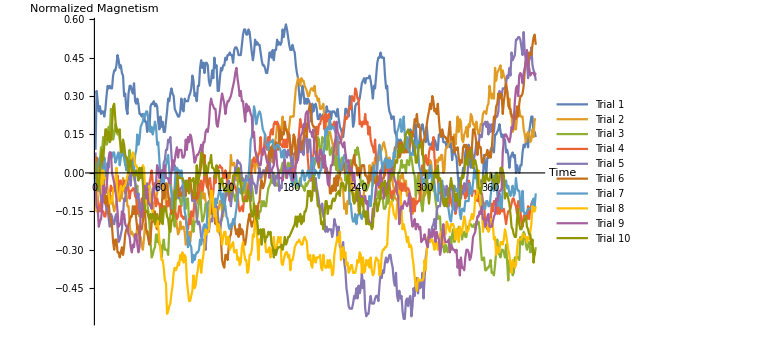

0.166795

```mathematica
magnetism1={18,64,56,48,52,46,48,48,44,50,60,68,66,68,66,66,76,80,80,84,92,88,82,84,78,76,60,62,50,46,62,68,68,64,62,70,56,54,58,54,46,46,44,46,46,40,40,32,44,34,52,54,54,56,52,54,52,40,34,44,36,40,32,32,40,48,58,56,62,66,62,60,50,48,46,44,44,48,58,50,48,58,56,56,56,60,62,66,76,72,60,62,56,68,68,82,88,82,86,78,86,86,84,72,68,72,80,74,90,82,84,64,64,74,82,80,84,84,90,88,92,92,94,92,92,86,96,98,98,96,92,92,92,100,108,112,112,108,108,112,110,102,94,88,94,104,100,102,100,100,94,88,84,84,82,78,78,84,94,94,90,96,88,96,96,104,100,102,100,102,112,106,112,116,112,106,100,96,96,100,96,94,84,78,74,62,54,60,68,62,54,58,54,58,56,52,40,54,48,52,54,50,42,42,46,44,42,46,44,42,52,48,48,48,42,48,48,48,46,44,50,42,36,34,30,28,36,50,50,46,44,60,58,50,36,40,52,54,54,56,58,64,70,72,74,70,74,74,74,76,72,66,58,68,66,76,86,90,90,94,90,90,90,76,66,68,54,48,46,42,44,44,32,30,26,26,20,26,24,22,18,20,18,20,24,26,34,30,24,16,24,38,20,24,22,32,34,38,34,28,24,36,26,22,22,22,24,18,26,24,18,18,30,30,32,32,24,24,24,20,22,24,20,24,10,18,18,14,12,0,-10,-4,-6,-4,4,2,16,20,16,22,8,4,12,4,4,-4,2,-4,-2,-8,-6,-12,-4,14,8,-2,12,12,12,18,20,18,16,30,30,32,34,38,32,28,30,24,26,16,18,14,4,12,14,16,12,14,0,6,2,0,6,6,16,22,20,24,28,20,32,38,44,44,30,32,28}/200;
magnetism2={-10,-10,-4,-4,-8,-18,-22,-14,-16,-12,-12,-14,-26,-16,-24,-18,-26,-30,-26,-22,-16,-18,-22,-14,-20,-4,-12,-14,-14,-26,-26,-40,-48,-46,-48,-50,-48,-50,-40,-48,-54,-50,-56,-60,-52,-40,-46,-48,-46,-50,-54,-34,-34,-24,-22,-20,-16,-6,-6,-10,-10,-8,-16,-14,-24,-18,-8,-8,-4,-12,-20,-18,-30,-34,-42,-48,-46,-38,-44,-42,-42,-46,-56,-52,-54,-46,-54,-46,-44,-36,-20,-16,-16,-24,-24,-22,-18,-12,-20,-16,-22,-24,-34,-32,-26,-18,-24,-26,-26,-34,-32,-30,-28,-22,-22,-30,-34,-18,-16,-8,-6,0,-4,14,6,6,8,2,-6,0,-4,-6,-6,-4,-14,-16,-8,-14,-8,-10,-10,6,10,6,6,0,16,8,4,2,-6,-4,2,2,0,2,2,14,10,14,10,8,16,24,28,38,38,30,36,34,44,32,34,34,34,30,36,44,44,44,44,56,66,70,74,72,68,74,72,72,68,66,64,60,60,64,66,66,64,68,60,60,56,58,50,50,52,54,42,46,34,26,32,32,28,24,20,22,26,6,6,-2,-4,-4,-8,-14,-28,-24,-32,-22,-24,-10,0,-6,-22,-16,-20,-18,-18,-30,-28,-18,-24,-24,-14,-14,-10,-12,-4,6,0,4,8,4,12,12,10,10,10,16,18,22,24,20,16,8,8,12,2,8,-8,-12,-20,-20,-22,-20,-16,-2,-4,0,-6,-14,-6,-18,-16,-18,-30,-26,-32,-24,-28,-20,-8,-2,0,-8,-12,-26,-18,-18,-16,-10,2,-2,10,8,-2,-6,-2,8,10,8,12,10,14,14,0,2,18,20,20,24,24,28,28,20,30,22,32,44,32,42,40,26,24,30,32,36,28,38,36,46,44,38,38,34,40,34,30,32,38,38,46,48,48,46,52,54,68,62,58,62,58,82,72,78,80,82,84,74,80,76,74,68,64,52,58,46,46,32,34,48,34,44,50,50,44,44,44,34,30,24,30,32,30,24,26,34,28,42,42}/200;
magnetism3={4,-2,0,6,10,20,18,28,26,26,22,24,36,30,50,36,26,30,38,36,30,32,26,22,20,20,12,6,12,12,6,18,0,-2,4,-4,-8,-14,-10,-32,-34,-26,-30,-22,-14,-16,-20,-24,-30,-40,-54,-66,-64,-60,-58,-48,-54,-48,-56,-56,-66,-58,-52,-60,-60,-60,-64,-46,-32,-30,-32,-36,-42,-20,-20,-14,-18,-22,-26,-18,-14,-20,-28,-20,-20,-40,-32,-36,-42,-46,-38,-38,-38,-32,-22,-8,-28,-38,-36,-32,-24,-26,-28,-34,-26,-20,-26,-30,-32,-24,-28,-32,-40,-44,-38,-36,-22,-20,-18,-10,-16,-18,-18,-10,-12,-16,-18,-22,-16,-10,-4,0,-8,-6,-4,-10,-10,-18,-18,-12,-10,0,-10,-16,-26,-30,-30,-26,-36,-30,-30,-22,-26,-22,-26,-26,-18,-12,-10,-8,-2,-8,0,-10,-8,-10,-10,2,0,4,8,6,4,-4,4,8,6,4,12,0,-2,-6,-12,-10,-12,-8,-4,-10,-10,-12,-14,-8,-10,-8,-6,-6,8,12,6,6,10,18,28,26,14,14,28,24,26,24,18,32,24,14,16,20,8,6,14,2,12,-2,2,10,12,10,6,-6,-2,-8,-2,4,10,6,8,8,18,14,20,16,10,-10,-8,-6,-12,-8,-14,-12,-10,-6,-2,0,-10,0,0,-10,-18,-20,-14,-18,-20,-20,-28,-28,-26,-14,-24,-18,-16,-18,-22,-16,-14,-14,-14,0,0,4,10,4,6,6,0,10,8,6,16,12,6,0,-2,-18,-10,-2,-16,-18,-24,-30,-22,-10,-14,-8,-8,-20,-10,-10,-2,-14,-14,-22,-28,-36,-34,-34,-50,-58,-48,-62,-56,-60,-62,-56,-50,-60,-48,-44,-54,-52,-44,-48,-42,-44,-44,-52,-48,-46,-50,-50,-42,-42,-40,-40,-42,-42,-40,-44,-38,-40,-38,-44,-58,-68,-68,-66,-76,-76,-74,-74,-72,-68,-78,-78,-80,-72,-62,-52,-62,-64,-66,-60,-60,-62,-66,-56,-70,-84,-68,-72,-74,-80,-78,-66,-66,-66,-66,-68,-50,-52,-56,-46,-48,-56,-60,-56,-54,-62,-58,-62,-60,-64,-58}/200;
magnetism4={2,-24,-18,-30,-30,-22,-30,-30,-34,-34,-28,-22,-22,-16,-10,-14,-12,-14,-14,-8,-2,-16,-6,-6,-12,-14,-6,-16,-14,-8,-12,-20,-14,-14,-12,-12,-18,-20,-32,-30,-24,-26,-20,-22,-10,-18,-22,-14,-14,-8,-4,2,-8,-12,-20,-26,-20,-24,-24,-30,-24,-28,-26,-28,-30,-22,-26,-22,-20,-26,-20,-24,-30,-32,-36,-34,-26,-26,-34,-34,-36,-34,-36,-44,-44,-36,-40,-30,-34,-30,-24,-22,-16,-20,-16,-10,-6,-14,-10,0,-4,-10,-12,-6,-4,-12,-20,-16,-2,-8,-2,4,4,6,4,4,-4,-4,2,-2,-12,-18,-22,-8,-16,-4,-8,-12,-14,-16,-26,-30,-28,-26,-30,-20,-18,-22,-18,-10,-10,-6,4,10,12,8,10,10,14,16,28,14,14,18,30,20,18,28,24,32,34,30,38,40,38,40,38,32,22,22,20,26,20,26,20,32,30,16,12,0,4,2,10,8,22,32,42,36,36,32,26,28,22,10,0,-4,-6,12,14,28,26,36,30,38,38,42,44,44,34,46,40,44,46,34,38,36,38,40,34,28,14,24,24,24,30,34,38,44,42,44,48,52,50,60,58,56,66,64,58,58,38,40,36,40,38,46,38,40,30,36,26,22,20,16,26,10,-2,-8,-12,-2,4,6,6,-2,6,4,0,-8,-16,-20,-14,-16,-14,-10,-8,-6,-10,-18,-8,-14,-10,-8,-14,-12,-12,-14,-18,-20,-30,-20,-30,-22,-24,-22,-22,-16,-2,6,-2,10,14,8,6,16,20,20,18,28,12,4,-4,-4,-16,-16,-14,-16,-16,-20,-24,-26,-26,-26,-16,-22,-26,-28,-22,-32,-28,-24,-26,-12,-10,-10,-16,-16,-20,-14,-18,-6,-8,-14,-18,-14,-14,-14,-20,-22,-16,-24,-26,-16,-22,-24,-38,-42,-44,-42,-42,-38,-24,-30,-22,-22,-26,-32,-26,-32,-28,-30,-30,-28,-34,-40,-34,-30,-30,-28,-24,-20,-20,-24,-26,-32,-22,-24,-28,-40,-42,-34,-32,-32,-36,-26,-36,-28,-24,-22,-24,-22,-22}/200;
magnetism5={16,-12,-6,-14,-10,-20,-24,-22,-14,-24,-28,-28,-36,-42,-32,-34,-40,-40,-34,-32,-42,-54,-52,-48,-44,-32,-20,-22,-6,-10,4,-2,-10,4,12,2,-6,-16,-20,-16,-28,-30,-26,-20,-16,-16,-12,-8,-12,-16,-24,-20,-12,-14,-12,-10,-14,-12,-10,-8,-4,-6,8,10,18,18,26,24,28,14,2,2,6,0,-10,-18,-20,-12,-12,-10,-8,-14,-6,-10,-14,-6,-10,-14,-22,-20,-22,-24,-36,-40,-38,-42,-50,-52,-52,-56,-60,-46,-42,-46,-38,-36,-38,-26,-32,-28,-26,-32,-42,-48,-38,-32,-30,-28,-20,-16,-12,-6,-14,-26,-18,-10,-6,4,2,10,8,8,6,-4,-6,-6,-6,-2,-6,-4,-8,-22,-2,-8,-8,-10,-16,-10,-2,4,-4,0,0,2,-4,4,0,6,12,2,2,0,-8,-10,-2,-4,0,-14,-10,-12,0,6,18,16,12,18,14,14,8,4,14,16,16,14,20,18,18,16,24,14,26,28,30,16,26,26,10,-4,-12,-14,-4,-12,-16,-22,-32,-26,-24,-34,-36,-46,-42,-46,-44,-44,-44,-50,-46,-36,-40,-42,-50,-42,-58,-58,-58,-54,-70,-76,-90,-96,-104,-106,-106,-106,-102,-96,-98,-90,-98,-88,-94,-90,-78,-90,-84,-106,-112,-110,-110,-102,-96,-102,-102,-102,-98,-96,-96,-100,-88,-78,-82,-76,-78,-70,-66,-70,-68,-64,-64,-70,-74,-84,-88,-78,-96,-100,-92,-98,-96,-108,-114,-114,-100,-98,-104,-98,-96,-112,-104,-90,-96,-84,-82,-94,-84,-90,-88,-78,-98,-82,-66,-60,-54,-50,-54,-46,-42,-40,-36,-44,-30,-26,-26,-26,-18,-12,-10,-14,-18,-10,-14,-18,-14,-8,-10,-24,-28,-30,-22,-20,-10,-20,-20,-14,-16,-8,-14,-10,-2,16,10,14,20,4,12,16,24,16,20,30,28,28,38,38,40,36,40,30,38,32,38,36,32,42,44,44,48,64,62,60,66,66,66,70,76,74,82,76,94,88,90,92,104,104,106,106,104,98,92,110,94,88,86,74,88,90,98,84,80,78,72}/200;
magnetism6={2,12,8,-8,6,0,10,0,-14,-24,-18,-26,-24,-34,-36,-42,-54,-60,-52,-52,-62,-62,-66,-62,-58,-64,-58,-48,-44,-44,-40,-38,-34,-34,-26,-32,-26,-36,-44,-42,-48,-42,-44,-38,-18,-32,-44,-46,-52,-56,-50,-38,-38,-38,-30,-42,-44,-40,-40,-28,-30,-14,-20,-18,-8,-10,-16,-22,-26,-32,-20,-18,-16,-6,2,-8,-18,-16,-18,-14,-10,-10,-18,-10,-14,-4,-4,-12,-16,-20,-16,-20,-20,-10,-4,0,6,16,8,14,0,0,-8,-16,-20,-32,-28,-28,-32,-40,-34,-40,-42,-44,-52,-68,-72,-74,-64,-64,-68,-58,-50,-48,-40,-38,-38,-44,-48,-44,-50,-40,-48,-44,-46,-56,-56,-50,-42,-36,-32,-38,-42,-38,-38,-26,-26,-34,-24,-22,-10,-6,-12,-10,-6,0,4,8,20,20,12,22,8,20,24,22,18,32,34,26,32,30,40,34,32,28,30,22,14,20,30,28,10,16,26,22,28,18,24,26,38,38,28,46,50,54,44,38,36,36,34,22,8,4,12,10,10,12,12,0,4,0,0,-16,-16,-10,-14,-4,-14,-2,-10,-4,-2,6,2,6,8,0,2,6,6,-2,2,4,10,14,6,6,-2,4,-2,0,6,6,6,-2,-2,-4,-8,-2,-6,4,4,-6,-8,-8,-2,-8,-10,-8,-8,-4,-4,10,12,8,10,4,-2,8,-2,12,20,20,20,24,12,14,24,16,16,16,22,16,20,16,24,32,28,34,42,40,46,36,38,34,22,14,26,26,32,38,44,48,54,50,60,56,48,50,46,54,42,32,28,34,30,28,28,26,24,32,40,26,26,28,16,20,18,20,12,6,10,8,20,22,20,22,12,18,20,12,20,34,34,30,24,14,24,20,20,8,8,12,14,14,18,12,16,12,18,32,44,42,52,54,62,58,62,60,46,56,62,70,64,56,50,50,44,44,42,44,42,52,44,54,60,60,62,68,80,88,86,84,94,92,92,100,106,108,100}/200;
magnetism7={-16,0,6,10,12,6,2,-8,12,-4,4,8,4,16,12,12,16,16,8,10,14,16,6,12,18,14,12,8,2,6,8,6,10,4,8,2,14,18,30,22,26,36,38,40,46,44,48,48,42,34,32,36,30,34,40,36,22,24,10,-2,0,-8,-8,0,6,10,14,2,-10,-16,-28,-20,-10,4,4,2,2,-4,2,-6,-12,-30,-34,-42,-58,-50,-56,-58,-70,-64,-68,-64,-62,-62,-60,-52,-56,-50,-42,-40,-46,-42,-24,-22,-22,-20,-24,-26,-26,-20,-24,-20,-16,-10,-18,-24,-16,-22,-26,-34,-36,-42,-44,-40,-42,-36,-40,-34,-28,-20,-12,-14,-16,-12,-14,-10,-8,-6,-4,-2,8,26,28,38,52,48,38,42,46,48,46,40,34,32,30,22,22,18,24,24,24,26,20,18,20,22,22,20,18,12,16,18,6,2,2,4,0,-2,-6,-10,-6,-4,0,-8,-10,-10,-10,-4,2,0,-6,-2,-2,2,-4,-2,8,6,12,-2,2,0,0,-4,2,2,16,12,22,34,30,36,34,42,34,36,36,34,32,28,28,12,4,2,6,10,14,14,2,0,-6,-24,-24,-34,-38,-38,-32,-40,-34,-32,-30,-34,-36,-30,-34,-34,-34,-30,-26,-18,-26,-18,-2,6,-2,0,2,16,22,16,8,0,8,10,12,4,10,4,10,4,6,16,12,20,32,34,38,42,32,34,44,30,20,28,18,18,14,14,16,14,14,22,26,20,6,2,0,-8,-8,-4,-10,-10,0,-4,6,-2,-6,-2,-8,-16,-20,-22,-8,-14,-8,-6,-16,-20,-22,-20,-24,-30,-36,-38,-30,-26,-10,-14,-14,-12,-18,-32,-36,-28,-28,-30,-22,-22,-22,-22,-8,-16,-16,-8,2,-4,0,-12,-12,-14,-12,-24,-26,-28,-28,-22,-22,-26,-26,-18,-10,-2,-14,-2,0,-16,-26,-16,-20,-28,-12,-4,-10,-6,-12,-10,-16,-18,-14,-10,-18,-16,-4,-12,-14,-14,-24,-30,-14,-30,-32,-32,-30,-28,-28,-28,-26,-22,-20,-26,-16}/200;
magnetism8={-16,-30,-16,-8,4,0,-16,2,-4,-4,-6,-12,-16,-24,-22,-22,-14,-10,-6,4,-22,-18,-16,-10,-12,-14,-10,-10,-6,-2,0,0,8,14,16,14,6,6,4,0,0,-2,2,6,4,-12,-24,-22,-14,-10,-26,-26,-32,-34,-36,-42,-36,-42,-52,-60,-68,-68,-74,-84,-86,-110,-108,-104,-102,-94,-88,-78,-74,-76,-74,-70,-72,-64,-68,-62,-70,-64,-66,-84,-92,-100,-100,-96,-92,-80,-90,-88,-80,-76,-68,-68,-78,-70,-64,-56,-44,-48,-46,-44,-28,-14,-14,-28,-34,-28,-38,-46,-40,-44,-48,-56,-50,-46,-46,-56,-50,-50,-60,-58,-56,-54,-62,-62,-60,-68,-66,-72,-70,-58,-54,-62,-68,-68,-78,-76,-64,-64,-60,-48,-50,-34,-38,-52,-68,-52,-52,-50,-48,-46,-52,-62,-60,-62,-58,-66,-60,-60,-50,-60,-62,-56,-50,-54,-50,-70,-72,-68,-64,-62,-62,-66,-64,-76,-68,-68,-64,-58,-56,-54,-54,-52,-54,-56,-56,-52,-50,-52,-54,-66,-68,-64,-72,-74,-64,-66,-70,-66,-66,-66,-64,-74,-76,-64,-72,-74,-74,-68,-74,-68,-72,-80,-78,-64,-58,-54,-50,-54,-46,-68,-66,-58,-66,-62,-72,-70,-78,-76,-72,-72,-78,-78,-78,-74,-68,-70,-62,-64,-78,-66,-78,-76,-68,-72,-68,-74,-66,-76,-80,-78,-70,-66,-68,-68,-80,-78,-64,-60,-60,-58,-58,-56,-38,-28,-24,-22,-26,-32,-34,-36,-24,-22,-14,-16,-28,-44,-40,-44,-48,-54,-50,-58,-56,-58,-66,-72,-82,-88,-92,-82,-84,-84,-84,-84,-82,-68,-76,-60,-50,-54,-54,-52,-52,-56,-60,-54,-54,-60,-54,-48,-46,-48,-56,-48,-48,-38,-40,-44,-46,-40,-40,-40,-44,-52,-44,-44,-54,-42,-48,-46,-40,-34,-38,-46,-46,-44,-38,-36,-32,-36,-32,-18,-20,-16,2,-12,-28,-28,-46,-40,-40,-42,-40,-46,-44,-36,-38,-40,-52,-50,-64,-58,-62,-60,-54,-54,-56,-52,-44,-48,-54,-60,-64,-72,-78,-68,-70,-74,-72,-60,-52,-52,-52,-52,-48,-48,-50,-50,-54,-50,-52,-46,-40,-26,-30,-30,-26}/200;
magnetism9={-10,-26,-28,-42,-38,-36,-28,-10,-12,-16,-12,0,12,16,16,0,-4,-8,-14,-20,-30,-42,-40,-40,-30,-36,-32,-40,-42,-42,-48,-50,-58,-62,-56,-58,-48,-48,-56,-62,-58,-30,-34,-26,-16,-10,-20,-12,-24,-24,-26,-28,-16,-12,-8,-8,6,2,-4,0,2,2,2,6,-4,-4,-4,-8,-8,2,10,6,10,16,20,12,18,18,18,12,12,14,26,18,28,24,30,28,22,16,8,10,14,14,16,18,22,16,24,24,32,34,32,38,52,58,54,52,50,50,38,36,42,48,56,62,58,54,46,52,56,56,58,60,64,68,72,78,82,74,68,60,64,56,56,48,40,54,48,52,50,46,44,28,32,18,14,12,8,6,6,14,18,20,16,12,8,8,-4,2,2,4,6,16,18,6,2,-4,-4,-4,-6,2,10,0,-4,2,0,4,2,-6,-4,-2,6,10,10,18,28,30,32,38,36,46,48,48,36,32,32,28,34,16,16,10,8,12,18,18,12,4,14,6,2,-8,-10,-2,6,6,12,20,26,40,32,30,28,24,22,20,24,16,10,8,10,2,4,2,-6,0,-12,-12,-22,-14,-14,-24,-18,-26,-20,-18,-24,-22,-36,-40,-40,-38,-28,-34,-18,-10,-8,-10,-8,2,-6,-12,-20,-10,-8,-14,-6,2,-2,0,4,-2,-6,-8,-16,-18,-40,-30,-26,-28,-24,-22,-24,-26,-24,-16,-24,-36,-42,-40,-36,-44,-40,-40,-44,-42,-54,-52,-52,-48,-52,-56,-58,-44,-50,-48,-50,-44,-46,-54,-46,-50,-52,-64,-60,-48,-40,-50,-54,-54,-54,-52,-62,-56,-58,-60,-60,-62,-60,-74,-68,-80,-66,-74,-74,-76,-66,-60,-60,-62,-68,-66,-60,-50,-48,-46,-40,-34,-34,-30,-32,-26,-36,-36,-42,-40,-34,-32,-42,-42,-42,-38,-34,-32,-20,-22,-18,-14,-14,-12,16,26,30,30,28,26,24,28,36,34,40,56,66,68,60,76,78,76,70,78,82,88,96,80,82,76,78,78,78,76,78}/200;
magnetism10={8,-2,-14,-10,2,12,18,10,22,34,34,26,32,24,26,36,52,54,42,32,34,32,34,16,16,26,22,14,12,10,0,8,10,2,2,-2,-2,2,-2,-6,4,-4,4,-8,-20,-28,-30,-30,-34,-36,-32,-36,-32,-32,-40,-36,-32,-36,-36,-38,-28,-40,-30,-26,-28,-34,-36,-44,-46,-38,-36,-32,-14,-20,-8,-2,-4,-4,-4,-4,-6,-8,-12,-6,-10,-16,-6,-6,-6,-4,-18,-10,6,-8,-2,6,16,12,8,-2,6,2,0,8,8,14,4,4,2,-4,6,0,2,-12,-6,-4,-10,-14,-14,-14,-14,-10,-16,-12,-14,-2,-2,0,-2,2,4,-4,-10,-14,-22,-22,-22,-22,-22,-14,-16,-28,-34,-34,-24,-30,-36,-38,-48,-46,-44,-56,-44,-44,-54,-50,-50,-46,-48,-46,-56,-58,-66,-60,-64,-60,-58,-58,-58,-56,-60,-56,-50,-56,-54,-50,-50,-48,-46,-44,-42,-40,-34,-42,-34,-38,-32,-40,-34,-38,-30,-30,-26,-14,-18,-14,-22,-18,-2,-10,-12,-16,-26,-26,-28,-40,-38,-44,-34,-22,-22,-32,-26,-26,-28,-22,-20,-22,-20,-16,-16,-14,-18,-8,-10,-8,-12,-14,-8,-2,-2,-14,-14,-14,-18,-24,-22,-14,-12,-18,-32,-20,-24,-20,-34,-30,-40,-30,-40,-40,-40,-44,-42,-24,-24,-20,-30,-26,-22,-18,-8,-10,-8,-6,-18,-14,-16,-6,-6,0,-2,-2,6,10,8,18,16,22,16,18,18,26,30,32,34,30,30,28,24,22,20,8,8,16,22,20,24,18,10,-2,2,-10,-14,-24,-14,-12,-10,-8,0,2,-4,6,-6,-4,-8,-18,-24,-26,-20,-26,-20,-12,-12,-4,-10,-10,-16,-22,-16,-22,-24,-26,-6,-2,-4,0,10,12,6,16,16,18,14,4,8,10,6,0,-12,-12,-16,-10,-4,-2,-8,0,-4,-6,-6,0,-2,-6,-6,-12,0,0,-8,-6,4,4,2,-2,-20,-16,-16,-20,-24,-32,-42,-44,-48,-50,-50,-36,-28,-40,-44,-44,-40,-38,-36,-34,-42,-44,-48,-48,-56,-52,-70,-62,-62}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT19=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### Large Lattice: 200 long, kT=2, 400 time steps

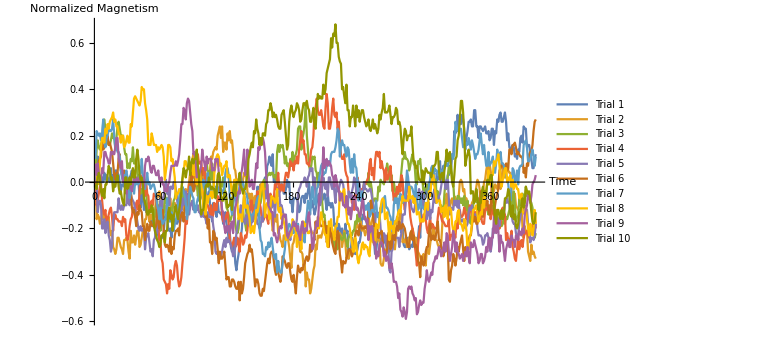

0.163904

```mathematica
magnetism1={4,2,22,6,-2,-2,4,0,8,2,6,4,2,0,12,0,6,-4,10,10,8,6,0,-8,-2,-2,-4,6,4,0,-8,4,6,10,4,10,2,0,4,0,-12,-22,-6,-14,-24,-16,-26,-22,-18,-34,-32,-38,-30,-28,-42,-48,-40,-44,-50,-50,-46,-48,-44,-30,-28,-28,-40,-42,-40,-48,-40,-42,-32,-34,-36,-34,-28,-26,-18,-18,-6,-12,-8,-18,-10,-14,-4,4,-2,0,-4,-2,-4,-4,-16,-12,-8,-14,-16,-30,-24,-14,-12,-8,-18,-28,-34,-18,-22,-26,-30,-16,-26,-26,-28,-28,-36,-34,-26,-36,-40,-50,-44,-56,-60,-54,-54,-70,-76,-68,-62,-50,-48,-40,-24,-12,-16,-26,-32,-26,-22,-24,-22,-22,-22,-28,-20,-4,-6,-4,-2,-2,-8,0,4,0,14,16,22,18,14,24,0,2,-4,-8,-6,-2,-2,-2,-2,-10,-10,-6,2,-4,0,-18,-16,-26,-14,-14,-14,-14,-18,-26,-24,-14,-12,-12,-18,-10,-14,-8,0,-14,-22,-16,-22,-28,-24,-18,-12,-10,-14,-16,-16,-14,-10,-16,-24,-10,-20,-18,-22,-18,-22,-38,-36,-42,-44,-36,-40,-46,-40,-46,-48,-36,-44,-42,-66,-58,-58,-48,-62,-60,-62,-62,-58,-52,-52,-46,-32,-28,-32,-30,-34,-38,-44,-40,-46,-48,-38,-50,-62,-60,-50,-50,-48,-56,-50,-52,-46,-52,-54,-60,-52,-60,-54,-52,-38,-34,-34,-36,-30,-38,-40,-40,-44,-40,-54,-56,-56,-50,-48,-58,-56,-54,-56,-50,-56,-48,-58,-48,-38,-48,-22,-12,-20,-8,-6,-10,-2,-4,-8,-12,-12,-10,-6,-8,8,2,6,18,0,8,14,2,-2,-2,6,6,14,10,24,22,44,42,44,58,46,54,50,58,54,46,32,38,44,52,52,54,48,48,62,62,48,48,38,48,48,46,44,46,48,42,42,44,36,38,46,46,32,44,42,54,52,58,60,52,52,56,60,52,36,42,30,28,30,32,30,22,24,20,28,26,38,40,34,48,46,46,30,32,32,26,20,12,12,20,24}/200;
magnetism2={10,-32,-28,-30,-36,-34,-24,-32,-28,-36,-30,-34,-30,-42,-46,-42,-56,-58,-62,-58,-48,-48,-52,-56,-58,-62,-50,-50,-48,-50,-60,-66,-42,-52,-52,-46,-54,-48,-42,-42,-56,-54,-48,-42,-44,-32,-32,-20,-26,-34,-28,-32,-28,-24,-30,-10,-14,-12,-8,-10,-16,-20,-24,-26,-20,-20,-14,-18,-14,-24,-22,-18,-18,-20,-20,-26,-24,-20,-12,-22,-24,-18,-6,-8,-8,0,8,8,20,24,20,14,16,8,6,-12,-6,-4,0,10,4,2,8,4,10,22,20,26,28,30,28,40,44,48,38,48,26,34,34,28,42,36,44,34,36,26,12,10,2,2,-2,-2,-6,-6,2,8,6,4,-8,-14,-10,-18,-10,-14,-22,-12,-12,-22,-8,-10,-2,-6,-4,-4,-8,0,-2,-20,-26,-20,-32,-42,-36,-28,-34,-28,-44,-44,-50,-52,-56,-46,-46,-50,-42,-50,-56,-66,-74,-54,-52,-46,-46,-42,-50,-52,-60,-60,-62,-72,-68,-90,-78,-84,-84,-96,-92,-84,-76,-72,-54,-58,-46,-48,-46,-48,-44,-40,-42,-42,-52,-48,-48,-44,-40,-40,-46,-44,-44,-46,-54,-50,-44,-46,-56,-50,-42,-52,-66,-64,-66,-60,-58,-64,-60,-50,-46,-34,-38,-40,-38,-34,-42,-38,-42,-46,-42,-40,-26,-38,-40,-34,-30,-28,-46,-52,-44,-50,-50,-70,-72,-72,-66,-58,-62,-60,-56,-54,-46,-44,-54,-54,-58,-48,-30,-40,-32,-24,-32,-52,-50,-52,-48,-56,-54,-48,-46,-46,-40,-44,-52,-48,-56,-60,-62,-64,-70,-68,-62,-66,-72,-58,-58,-62,-54,-46,-48,-40,-46,-50,-50,-54,-56,-56,-54,-38,-22,-22,-20,-10,-18,-24,-22,-16,-14,-20,-12,-14,-18,-16,-12,0,2,0,-8,-6,-16,-14,-34,-34,-24,-24,-18,-16,-12,-10,-4,2,0,-6,-18,-8,-10,0,2,10,16,8,16,10,2,-8,-8,-2,-4,-6,0,-4,-6,2,14,4,4,4,16,10,8,8,-8,-12,-14,-10,-20,-22,-24,-24,-24,-22,-40,-48,-38,-44,-42,-60,-64,-68,-54,-62,-60,-64,-66}/200;
magnetism3={6,28,36,30,28,32,36,52,54,46,38,34,32,32,36,42,38,38,30,38,48,52,46,40,40,40,30,24,24,12,16,12,20,18,30,16,16,20,8,2,6,-10,-6,-8,-10,-8,-6,-26,-22,-24,-18,-26,-26,-34,-26,-20,-16,-30,-20,-42,-34,-32,-28,-10,-18,-14,-32,-34,-22,-30,-22,-16,-14,-8,-10,-18,-22,-18,-10,-6,-18,-18,-16,-18,-26,-20,-10,-10,4,6,4,0,-2,-12,-6,0,6,6,6,8,14,18,8,8,10,2,16,2,-12,-8,-12,2,2,0,-2,-4,4,0,-14,-22,-24,-28,-34,-32,-28,-28,-22,-36,-42,-44,-40,-28,-22,-24,-22,-34,-36,-42,-24,-26,-26,-32,-32,-28,-20,-32,-30,-28,-24,-20,-18,-12,-2,2,-4,-4,6,6,8,6,8,8,4,6,2,26,32,26,32,30,32,26,16,22,14,16,10,20,16,26,14,22,24,28,46,48,48,28,38,42,50,66,40,28,14,10,14,22,20,22,10,8,-4,8,-2,-4,-18,-30,-28,-38,-38,-38,-38,-40,-42,-46,-50,-58,-48,-56,-58,-52,-46,-48,-50,-48,-44,-48,-52,-56,-48,-46,-44,-46,-42,-42,-34,-36,-28,-34,-34,-24,-20,-10,0,0,0,-2,8,-4,0,-6,-18,-16,-14,-16,-16,-4,-8,2,0,0,-2,6,10,16,10,2,0,6,-8,0,-6,-14,-10,-10,-2,0,10,20,20,26,20,20,18,10,14,20,24,16,14,0,-2,18,16,20,8,2,-10,-6,-4,-2,-8,-2,-6,0,0,4,2,2,-14,-8,-12,-20,-20,-24,-26,-10,0,-6,4,14,8,14,6,0,-16,-18,-18,-12,-12,-14,-18,-14,-20,-12,-22,-24,-16,-26,-34,-36,-24,-22,-14,-16,-10,-18,-14,-22,-32,-20,-18,-10,-16,-22,-24,-28,-22,-24,-20,-24,-24,-28,-38,-36,-40,-40,-34,-38,-36,-30,-36,-30,-32,-28,-24,-8,-14,-22,-8,-20,-34,-30,-30,-14,-20,-16,-10,-24,-14,-4,-12,-8,-10,-16,-18,-22,-30,-48,-44}/200;
magnetism4={4,-20,-16,-10,-4,-2,-16,-26,-28,-24,-36,-32,-28,-24,-22,-30,-42,-30,-28,-32,-32,-34,-34,-34,-38,-30,-34,-32,-46,-50,-46,-38,-32,-30,-22,-24,-30,-18,-16,-24,-8,6,4,6,0,-12,0,-10,-12,-26,-20,-16,-20,-10,-12,-12,-28,-36,-50,-50,-66,-70,-84,-86,-88,-96,-88,-92,-76,-80,-84,-82,-72,-68,-72,-84,-90,-88,-82,-70,-60,-48,-30,-36,-22,-2,-4,-2,8,4,10,4,10,24,16,16,18,6,12,12,-10,-18,-20,-24,-28,-20,-30,-28,-18,-24,-24,-12,-16,-16,-12,-30,-34,-32,-32,-28,-26,-36,-50,-54,-56,-52,-48,-56,-54,-48,-54,-60,-44,-48,-54,-52,-46,-48,-42,-30,-26,-16,-16,-32,-24,-20,-22,-8,-14,-18,-22,-32,-34,-32,-28,-28,-32,-36,-12,-10,-22,-16,-14,-2,-6,0,8,-6,-8,-2,-6,-8,2,8,8,4,10,18,14,16,10,18,16,22,16,28,36,44,34,36,24,24,16,16,14,20,28,30,40,62,64,72,62,58,58,62,56,48,46,64,76,68,46,46,52,64,72,58,56,60,46,52,36,24,20,20,24,10,6,4,-10,-12,-10,-18,-14,-24,-10,-14,4,-2,-12,-6,-6,-6,-2,-2,0,2,4,16,20,6,12,2,18,26,26,22,26,12,18,12,10,0,12,2,4,8,14,2,-6,-16,-10,-12,-4,-10,-2,-8,6,2,-16,-24,-14,-14,-12,-18,-30,-36,-40,-48,-54,-62,-72,-54,-44,-38,-32,-34,-28,-28,-32,-40,-44,-38,-30,-40,-36,-38,-40,-40,-40,-30,-22,-26,-30,-34,-34,-36,-38,-38,-38,-32,-50,-46,-46,-42,-46,-48,-34,-40,-28,-24,-30,-30,-28,-22,-26,-32,-28,-32,-20,-22,-28,-32,-26,-26,-26,-30,-34,-30,-24,-34,-36,-36,-24,-22,-24,-22,-20,-32,-24,-24,-30,-26,-24,-40,-36,-40,-36,-24,-22,-26,-28,-50,-44,-50,-52,-48,-42,-56,-60,-66,-68,-58,-48,-58,-52,-50,-56,-48,-44,-44,-42,-46,-48,-38,-40,-40,-28,-26,-40}/200;
magnetism5={12,-2,-26,-18,-16,-20,-40,-40,-32,-44,-36,-34,-46,-50,-60,-56,-34,-26,-26,-26,-26,-14,-22,-24,-20,-24,-20,-20,-20,-10,-18,-20,-10,-14,-16,-18,-24,-28,-34,-40,-42,-38,-42,-40,-42,-58,-48,-46,-44,-52,-60,-58,-64,-50,-48,-40,-44,-28,-24,-16,-28,-14,-12,-4,2,-10,-4,-20,-4,-4,-6,0,0,-6,-14,-22,-26,-34,-28,-14,-20,-16,-8,-16,-12,-28,-22,-18,-16,-24,-20,-24,-24,-20,-26,-26,-30,-26,-30,-28,-32,-36,-26,-30,-30,-30,-30,-38,-44,-60,-62,-60,-68,-64,-64,-60,-54,-50,-56,-48,-52,-50,-52,-54,-58,-64,-62,-56,-44,-38,-32,-30,-20,-26,-32,-32,-36,-28,-30,-36,-38,-38,-34,-34,-26,-26,-28,-36,-36,-40,-38,-30,-34,-20,-8,-14,-2,-12,-20,-22,-22,-20,-16,-30,-14,-8,-12,-8,-22,-20,-24,-30,-30,-28,-42,-48,-44,-50,-40,-44,-36,-36,-38,-32,-10,-6,-4,0,0,0,4,2,-4,4,6,12,10,12,-4,4,-14,-12,-12,-16,-20,-16,-4,4,-2,-6,0,-12,4,4,-2,-6,0,-8,-18,-2,-8,-6,-2,2,0,-2,-10,-18,-18,-24,-8,-10,-14,-8,-4,4,2,-10,2,0,-2,-16,-12,-8,0,-6,-6,-8,-8,-6,-6,-12,-18,-24,-36,-26,-28,-30,-26,-40,-50,-52,-44,-46,-54,-46,-56,-76,-78,-60,-58,-46,-48,-48,-48,-48,-56,-48,-44,-28,-28,-28,-12,-8,0,-2,-14,-22,-24,-26,-22,-14,-16,-12,-6,-12,-12,-8,-22,-18,-20,-32,-28,-18,-32,-24,-26,-16,-8,-18,-16,-16,-12,-10,-4,2,2,2,-6,0,2,-14,-28,-24,-22,-24,-16,-20,-16,-22,-16,-28,-34,-34,-32,-34,-40,-38,-36,-26,-22,-24,-20,-30,-28,-28,-28,-40,-46,-46,-46,-48,-54,-52,-46,-46,-44,-48,-56,-60,-54,-40,-44,-36,-40,-30,-34,-38,-26,-32,-28,-30,-16,-18,-14,-18,-18,-26,-28,-34,-36,-36,-44,-48,-46,-36,-30,-24,-24,-22,-20,-26,-24,-36,-40,-52,-48,-48,-50,-46,-36}/200;
magnetism6={-2,0,4,18,20,22,36,28,30,34,38,40,32,34,30,26,16,6,2,8,8,20,24,10,6,8,10,-2,0,-6,-2,-8,-4,-22,-26,-24,-30,-38,-26,-28,-20,-24,-26,-38,-38,-50,-42,-36,-42,-42,-34,-36,-38,-38,-40,-38,-24,-34,-40,-34,-32,-24,-44,-54,-56,-54,-56,-60,-48,-62,-56,-58,-46,-42,-42,-40,-46,-32,-28,-26,-34,-24,-20,-24,-20,-14,-8,8,-2,-8,-6,12,6,-2,-4,4,10,-4,-14,-20,-30,-28,-40,-32,-52,-52,-62,-42,-44,-50,-48,-58,-70,-60,-66,-66,-64,-60,-72,-84,-82,-82,-90,-90,-84,-84,-86,-90,-92,-92,-86,-102,-86,-96,-92,-82,-70,-66,-62,-60,-54,-60,-58,-66,-78,-90,-84,-84,-88,-96,-98,-98,-92,-94,-86,-78,-70,-66,-70,-62,-60,-60,-68,-76,-80,-70,-78,-82,-86,-80,-64,-66,-68,-72,-74,-70,-70,-78,-84,-86,-80,-88,-96,-82,-72,-76,-78,-74,-76,-72,-70,-66,-64,-68,-66,-54,-60,-58,-48,-50,-34,-44,-30,-32,-36,-38,-38,-38,-34,-44,-38,-46,-56,-38,-42,-52,-56,-60,-62,-50,-42,-46,-62,-68,-78,-68,-70,-70,-66,-62,-58,-58,-60,-64,-58,-58,-46,-42,-42,-46,-36,-38,-40,-40,-40,-38,-40,-40,-22,-28,-16,-20,-28,-38,-36,-38,-40,-48,-44,-44,-42,-52,-60,-60,-62,-58,-44,-44,-58,-56,-46,-46,-50,-40,-38,-42,-34,-40,-40,-36,-38,-40,-46,-52,-56,-56,-44,-42,-50,-46,-56,-54,-56,-68,-70,-82,-64,-68,-72,-70,-60,-56,-56,-44,-36,-50,-48,-46,-50,-48,-40,-34,-50,-50,-56,-58,-64,-60,-56,-56,-52,-84,-86,-76,-72,-62,-66,-72,-66,-56,-60,-54,-50,-46,-58,-68,-56,-62,-56,-50,-46,-46,-38,-28,-34,-30,-36,-36,-26,-22,-8,-12,-30,-18,-16,-20,-16,-24,-28,-24,-2,-14,-28,-20,-14,-10,-6,10,12,16,16,12,14,16,10,12,28,28,24,32,32,34,30,24,26,24,22,22,20,8,12,4,16,14,24,26,26,32,44,52,54}/200;
magnetism7={20,44,42,40,42,36,42,54,36,30,38,40,46,44,44,46,54,40,28,30,26,26,22,10,4,0,6,4,10,4,-6,-14,-10,0,0,-10,0,-2,2,-2,6,8,20,6,2,-6,2,8,-2,0,-6,-4,-2,-2,-6,-12,-20,-24,-32,-22,-32,-36,-34,-32,-32,-14,-30,-26,-34,-26,-34,-42,-36,-34,-26,-20,-14,-6,-6,-4,-8,-12,-18,-32,-26,-12,-4,-8,-12,-14,-26,-26,-18,-14,-12,0,-4,-6,2,-2,-10,0,8,-4,-8,-6,-12,-6,-10,-4,-4,-4,-8,-6,-6,-10,-8,-4,8,12,12,6,-14,-22,-28,-22,-12,-10,-18,-18,-10,-2,6,-2,0,-6,-10,-10,-14,-24,-26,-34,-28,-28,-26,-24,-18,-14,-12,-40,-50,-52,-62,-62,-64,-56,-58,-52,-56,-52,-48,-56,-64,-66,-62,-78,-68,-76,-78,-78,-70,-64,-58,-46,-48,-38,-36,-38,-44,-36,-44,-40,-44,-44,-36,-50,-44,-50,-50,-40,-52,-36,-28,-16,-18,-28,-16,-4,-12,-18,-20,-6,-4,2,8,14,16,6,8,8,14,16,18,14,24,26,26,26,30,36,46,44,22,30,36,32,32,26,22,30,28,16,8,20,8,24,14,12,0,-16,-10,-16,-8,-14,-22,-24,-20,-24,-18,-30,-28,-24,-24,-26,-22,-16,-30,-28,-34,-22,-26,-16,-14,-12,-22,-22,-24,-28,-30,-36,-40,-20,-14,-18,-14,-26,-14,-10,-16,-18,-16,-12,-4,10,4,-8,-4,-4,-6,-10,-14,-2,-18,-24,-22,-10,-20,-22,-22,-24,-18,-20,-18,-2,2,12,14,-2,12,10,10,6,6,10,4,10,6,14,18,14,14,18,24,22,24,20,26,52,48,44,46,46,46,38,30,32,28,34,32,38,34,28,36,32,26,20,24,24,28,36,42,32,24,32,22,14,14,26,14,16,18,22,12,8,16,28,20,20,26,16,16,14,10,6,2,-2,-12,-16,-4,12,10,0,2,10,-2,12,14,14,16,32,34,36,30,18,18,20,24,28,22,14,22}/200;
magnetism8={16,8,-2,4,16,30,38,38,34,46,42,50,46,52,54,56,60,52,54,48,48,42,40,34,40,40,30,32,36,40,34,34,50,48,60,72,74,72,70,68,66,70,82,80,80,68,62,54,32,32,32,42,38,32,32,32,26,30,28,30,32,30,22,2,10,16,32,32,30,18,20,12,4,-14,-10,-10,-6,-8,-6,2,6,18,18,14,12,12,10,10,16,6,16,4,-2,6,8,8,-2,-8,-22,-24,-28,-12,-18,-12,-12,-8,-14,-12,8,14,22,24,22,14,16,6,10,14,14,18,4,6,6,-2,-10,-6,2,2,2,-20,-32,-28,-28,-34,-24,-8,-22,-22,-20,-26,-32,-44,-42,-38,-44,-36,-24,-26,-22,-14,-8,-4,0,-12,-30,-20,-18,-20,-32,-20,-12,-14,-14,-18,-16,-6,-24,-26,-22,-32,-28,-34,-38,-50,-44,-44,-48,-44,-46,-32,-34,-40,-42,-56,-46,-48,-46,-58,-38,-34,-38,-36,-40,-44,-44,-42,-42,-44,-44,-46,-40,-40,-34,-40,-32,-26,-32,-38,-44,-46,-46,-56,-34,-38,-32,-42,-44,-50,-38,-38,-30,-30,-8,-10,-16,-8,-6,-18,-26,-36,-36,-40,-46,-52,-60,-60,-48,-54,-66,-70,-64,-62,-54,-52,-58,-54,-56,-56,-62,-64,-48,-44,-52,-50,-50,-36,-38,-40,-32,-22,-16,-14,-16,-32,-30,-26,-38,-50,-34,-40,-38,-44,-34,-34,-32,-26,-24,-26,-18,-12,-16,-16,-16,-16,-16,-4,-14,-14,-12,-18,-14,-20,-28,-26,-26,-34,-34,-32,-34,-26,-18,-18,-24,-8,-12,-2,4,6,-4,-10,-18,-16,-16,-16,-26,-24,-22,-30,-20,-24,-32,-22,-22,-24,-36,-42,-44,-34,-34,-26,-24,-36,-36,-38,-42,-32,-34,-42,-58,-58,-48,-44,-36,-24,-24,-22,-20,-28,-34,-30,-26,-28,-14,-22,-10,-6,0,10,-2,-2,6,6,18,14,18,20,24,14,2,-4,2,6,12,12,0,4,2,6,-4,2,-6,-2,-2,-6,-6,-14,-14,-10,-26,-26,-28,-22,-32,-40,-46,-36,-40,-46,-40,-24,-36}/200;
magnetism9={16,6,16,8,0,2,12,8,26,26,22,20,16,16,26,24,26,24,30,38,38,20,16,12,18,0,2,0,-10,-4,2,-4,-4,-8,-2,4,0,4,2,0,4,4,2,-6,-4,14,20,18,22,18,10,8,14,14,10,6,6,10,2,0,4,-2,-2,-8,-6,-8,-2,0,8,14,14,14,14,18,14,18,24,36,50,50,64,62,54,68,72,70,60,50,44,24,26,18,4,8,4,10,14,28,20,16,10,22,16,20,20,20,10,12,10,20,18,20,8,-4,-12,-24,-26,-38,-44,-38,-42,-38,-44,-36,-34,-44,-30,-22,-18,-10,-8,-10,6,10,18,28,6,8,28,6,-4,-2,2,-6,-6,4,16,12,30,28,34,36,38,34,26,8,-6,-20,-22,-24,-26,-26,-46,-44,-48,-52,-48,-40,-38,-40,-30,-28,-28,-32,-46,-48,-44,-42,-40,-38,-34,-38,-36,-42,-38,-46,-50,-38,-34,-44,-44,-40,-42,-30,-26,-38,-42,-58,-56,-42,-40,-34,-38,-18,-6,0,6,30,12,16,20,14,18,16,14,6,4,-4,6,2,-4,-6,-16,-10,-10,-20,-20,-22,-12,-20,-28,-22,-32,-24,-12,-12,-14,-24,-22,-26,-30,-28,-18,-14,-28,-32,-34,-32,-50,-38,-42,-38,-46,-54,-52,-66,-60,-64,-54,-52,-52,-54,-64,-60,-68,-64,-66,-74,-74,-70,-76,-86,-86,-86,-90,-100,-96,-110,-112,-116,-108,-112,-118,-112,-92,-90,-92,-90,-96,-98,-102,-100,-114,-112,-106,-102,-106,-104,-104,-92,-86,-76,-84,-86,-82,-78,-80,-70,-68,-64,-66,-62,-56,-58,-64,-62,-56,-52,-60,-44,-46,-60,-68,-62,-56,-42,-48,-60,-52,-60,-62,-66,-64,-62,-68,-64,-60,-64,-56,-64,-70,-52,-56,-56,-50,-54,-58,-62,-70,-68,-62,-62,-70,-68,-64,-56,-60,-50,-48,-58,-48,-48,-30,-42,-44,-32,-42,-60,-46,-52,-52,-60,-68,-58,-54,-50,-56,-56,-46,-50,-50,-56,-46,-48,-50,-42,-44,-46,-40,-44,-28,-24,-20,-10,-12,-18,-12,-2,0,2,6}/200;
magnetism10={-2,-6,4,8,4,-8,-12,-6,-14,-2,-2,6,14,10,2,4,-8,-2,-4,2,6,-4,-10,-8,-14,-18,-20,4,4,-6,-4,4,-2,6,12,4,4,20,28,20,6,2,4,-2,-14,-18,-22,-28,-28,-24,-26,-20,-22,-36,-42,-46,-50,-52,-56,-54,-46,-46,-44,-52,-42,-42,-26,-22,-32,-28,-42,-32,-22,-20,-28,-32,-24,-18,-8,4,12,10,4,10,12,22,6,16,20,16,20,20,28,14,6,-18,-28,-24,-24,-16,-4,-2,-4,4,-2,-6,-4,-6,-6,-14,-8,6,8,4,-12,-16,-16,-10,-8,-14,-22,-20,-20,-14,-24,-8,-2,-12,0,0,0,8,-4,-6,-10,-6,-6,0,6,20,24,30,34,30,44,42,54,46,42,32,38,32,42,42,40,50,52,62,62,68,64,56,60,56,58,54,48,46,46,58,60,62,52,40,28,32,52,62,66,60,56,60,62,68,66,62,52,54,62,68,68,66,70,64,62,52,52,58,64,48,46,64,76,72,74,72,72,84,76,80,94,98,102,106,124,116,128,126,136,120,120,108,104,102,80,82,74,68,84,62,62,48,56,56,66,58,48,66,56,62,52,58,62,62,56,52,48,50,54,46,44,48,54,46,50,46,42,46,58,54,60,64,76,60,60,60,62,66,58,50,56,56,58,64,62,50,52,48,34,24,38,46,44,36,40,40,40,48,32,18,18,12,14,8,2,2,0,10,-2,6,12,10,8,8,8,4,8,14,14,16,26,26,10,2,6,8,0,10,16,28,18,24,26,10,0,-4,6,20,22,36,40,54,70,70,60,42,14,20,24,28,22,-10,-8,-8,-18,-16,-6,-14,-24,-18,-18,-8,-4,-10,-8,-12,2,-2,2,6,6,-12,-18,-30,-36,-24,-24,-30,-32,-24,-32,-30,-14,-14,-12,-6,-10,-28,-30,-20,-32,-28,-38,-40,-36,-26,-26,-20,-14,-22,-18,-4,-8,-10,-8,-16,-26,-34,-36,-34,-26}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]

averageMagnetization1Dn200kT2=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### Large Lattice: 200 long, kT=2.1, 400 time steps

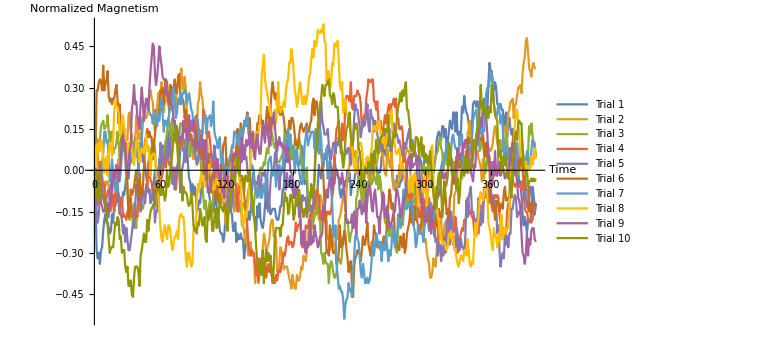

0.140735

```mathematica
magnetism1={-24,-58,-64,-60,-68,-58,-56,-44,-36,-32,-38,-38,-42,-46,-44,-32,-38,-24,-26,-20,-12,-18,-26,-20,-24,-16,-18,-12,-4,-6,-6,4,6,14,12,18,24,16,20,16,14,10,24,6,10,4,-4,-10,-16,-14,-22,-22,-20,-10,0,-2,-10,-10,8,-2,0,18,10,10,10,22,28,16,24,26,28,32,36,26,24,12,4,14,20,26,14,22,18,20,4,-6,-8,-18,-10,-18,-12,-16,-30,-28,-22,-24,-14,-12,0,-8,-10,-10,-12,-16,-22,-34,-24,-30,-24,-18,-26,-32,-36,-44,-46,-46,-52,-48,-34,-30,-22,-24,-28,-30,-32,-44,-44,-38,-52,-46,-50,-50,-46,-50,-50,-64,-58,-48,-32,-30,-36,-30,-18,-30,-34,-34,-44,-26,-34,-24,-36,-40,-42,-36,-26,-14,-28,-22,-24,-32,-30,-28,-28,-28,-34,-36,-36,-32,-26,-26,-14,-14,6,12,6,22,10,16,8,12,18,14,6,8,4,4,6,18,16,4,-10,-8,-8,-26,-24,-28,-26,-30,-26,-20,-20,-24,-10,4,-2,-6,2,2,12,8,14,18,14,8,2,-12,-4,10,2,0,-2,-6,-16,-20,-14,-18,-8,-12,-6,0,-8,-2,-18,-10,-10,-8,-2,-2,10,-2,0,-8,-8,-4,-18,-14,-30,-22,-8,-14,2,4,4,-2,8,4,-4,0,-2,0,10,12,18,12,10,22,18,18,16,6,-8,-12,-8,-16,-4,-12,-12,-8,-8,0,-6,-2,-14,-16,-16,-18,-34,-20,-14,-10,-18,-4,0,10,10,8,6,-2,-2,12,6,10,10,-2,-12,-12,2,-2,4,10,22,26,28,24,22,32,32,24,30,16,20,28,36,32,30,42,42,28,42,26,28,18,28,46,42,54,46,42,40,34,26,26,32,48,50,50,46,50,46,30,38,30,48,52,48,44,42,64,78,72,72,58,58,64,60,48,48,48,48,44,44,30,38,42,24,34,38,30,26,30,22,4,6,6,2,-12,-8,-18,-32,-40,-34,-38,-46,-36,-36,-38,-26,-12,-18,-26,-24}/200;
magnetism2={-8,16,14,0,0,-2,-10,-20,-20,-8,-10,-8,-12,-20,-30,-20,-8,-4,-2,2,0,8,-2,6,26,20,18,20,24,22,40,42,28,26,8,16,16,40,34,22,24,28,38,38,36,40,38,40,50,54,58,52,50,34,28,36,46,56,56,56,64,48,42,50,50,56,48,52,62,58,50,46,48,46,62,62,64,66,74,60,58,68,60,42,36,28,16,16,16,8,24,38,28,48,52,64,56,52,44,42,38,32,12,8,-10,-16,-14,-18,-16,-10,-2,-14,-20,-8,-22,-18,-24,-18,-38,-40,-40,-24,-30,-26,-14,-26,-24,-14,-18,-10,-22,-26,-24,-40,-40,-44,-52,-44,-54,-62,-56,-52,-62,-60,-64,-82,-72,-64,-82,-76,-70,-74,-56,-46,-50,-60,-56,-54,-50,-40,-36,-36,-48,-46,-50,-74,-72,-68,-56,-58,-66,-72,-70,-70,-70,-74,-78,-82,-86,-76,-82,-86,-86,-76,-80,-80,-76,-70,-72,-62,-64,-66,-60,-48,-42,-40,-46,-30,-36,-34,-30,-28,-26,-36,-18,-20,-24,-32,-34,-36,-36,-50,-48,-58,-52,-46,-52,-56,-58,-44,-50,-36,-34,-30,-24,-20,-18,-30,-14,-4,-4,8,20,20,14,10,14,6,6,-8,-10,-16,-18,-2,-6,-2,8,4,-6,-6,-10,-2,-2,-4,4,4,6,14,22,22,12,12,2,-2,-4,16,10,4,2,14,0,-14,-8,-12,-12,-10,4,-6,-2,4,12,10,12,16,14,14,-2,-8,-14,-16,-18,-4,-10,-14,-12,-18,-12,-32,-50,-52,-50,-60,-64,-68,-78,-78,-74,-64,-68,-70,-58,-46,-40,-40,-34,-52,-54,-40,-38,-36,-50,-42,-44,-50,-52,-42,-18,-16,-14,2,8,6,6,0,6,4,-2,8,26,30,36,24,16,18,18,18,12,14,8,6,2,-8,8,-6,2,4,8,14,16,14,16,20,28,32,28,20,16,12,22,14,18,32,30,28,24,42,44,50,50,52,38,48,48,54,60,60,62,56,70,78,82,94,96,86,74,72,68,76,78,74,74}/200;
magnetism3={26,22,22,18,22,32,34,36,30,32,32,40,28,20,28,28,12,16,16,20,28,20,8,20,26,32,18,8,-6,-14,-30,-36,-22,-28,-38,-24,-30,-42,-26,-24,-16,-22,-28,-28,-24,-20,-12,-12,2,16,10,16,18,22,16,0,-6,2,-12,-18,0,2,12,18,22,28,38,34,24,34,38,22,22,20,20,18,22,34,34,32,18,12,14,26,22,18,10,20,18,12,20,24,24,16,12,10,2,-8,-20,-28,-22,-34,-30,-26,-22,-24,-30,-18,-12,-2,2,4,0,-10,-10,-8,-6,-4,-8,-14,-16,-30,-22,-18,-12,-22,-30,-24,-16,-24,-26,-30,-22,-24,-24,-26,-30,-26,-20,-14,-10,-14,-22,-30,-24,-16,-12,-18,-8,-2,2,0,2,6,4,12,16,12,22,30,28,24,18,16,20,6,6,6,8,10,12,18,30,20,12,12,8,8,16,8,12,22,22,20,20,24,18,12,-6,-4,-2,-6,2,-18,-16,-30,-30,-42,-38,-30,-32,-32,-14,-30,-36,-60,-62,-68,-60,-66,-68,-68,-82,-70,-66,-68,-74,-78,-78,-74,-64,-64,-66,-68,-60,-48,-50,-32,-38,-36,-46,-52,-46,-44,-32,-40,-40,-20,-18,-4,-10,-4,-30,-28,-16,-10,-14,-10,-8,-18,-6,-10,-8,-4,-6,-10,-2,-14,-4,-8,-18,-24,-30,-38,-34,-44,-32,-48,-38,-40,-44,-50,-54,-58,-60,-40,-36,-36,-28,-40,-32,-26,-14,-26,-26,-20,-10,-16,-6,-14,-24,-20,-36,-32,-16,-14,-8,0,4,2,-4,2,2,-12,6,0,0,0,4,10,12,14,22,24,16,14,0,12,12,4,8,6,4,8,8,-4,6,-2,8,6,2,6,12,-6,2,6,2,12,22,10,2,0,10,18,16,18,18,36,32,14,16,22,26,12,-2,0,8,12,6,6,2,-10,4,0,-4,-2,10,22,10,16,14,22,18,28,22,8,16,8,4,2,-4,8,14,-4,-2,0,6,10,8,2,6,2,4,12,32,26,34,26,20,20,10}/200;
magnetism4={-8,-26,-10,0,6,6,-4,-12,-10,-28,-20,-16,-14,-18,-28,-24,-18,-30,-16,-12,-22,-24,-32,-20,-20,-34,-32,-34,-36,-30,-30,-26,-20,-34,-32,-32,-32,-30,-34,-24,-18,-12,-22,-14,-20,-20,-10,-12,6,0,-8,-8,-18,-18,-14,-14,-2,-22,-14,-8,-6,-2,4,10,2,16,8,4,6,-6,2,2,-6,-14,-4,6,14,22,18,20,30,32,42,30,22,32,34,36,32,28,38,38,40,24,30,28,28,26,44,38,36,28,24,28,22,12,2,10,8,-2,-10,-16,-24,-18,-4,2,4,-2,0,8,8,-2,-4,-6,-10,-10,-6,-8,-14,-30,-16,-16,-6,-6,-8,-18,-24,-28,-42,-54,-58,-62,-58,-60,-60,-68,-76,-70,-80,-64,-66,-68,-70,-74,-66,-78,-72,-68,-74,-68,-76,-80,-78,-82,-76,-80,-74,-72,-74,-68,-66,-60,-62,-56,-50,-48,-54,-52,-52,-56,-54,-48,-38,-44,-40,-40,-36,-48,-56,-48,-56,-40,-42,-42,-36,-32,-34,-26,-26,-28,-18,-14,-18,-18,-34,-36,-30,-26,-28,-38,-30,-32,-30,-32,-30,-20,-14,10,20,30,32,36,22,16,34,22,26,50,54,54,52,50,64,46,44,54,54,54,58,56,54,48,30,32,40,38,52,58,66,64,64,66,66,50,50,44,50,36,32,36,22,28,34,40,34,40,46,48,42,48,48,52,46,52,38,38,30,30,32,28,6,10,6,-10,-20,-18,-18,-22,-10,-6,-10,-10,-20,-28,-34,-34,-26,-22,-6,-12,-2,-14,-26,-20,-28,-24,-30,-30,-48,-40,-32,-40,-58,-58,-56,-56,-62,-48,-52,-52,-46,-40,-38,-40,-46,-46,-44,-34,-42,-60,-58,-50,-46,-42,-44,-36,-36,-34,-20,-24,-32,-30,-34,-34,-44,-48,-44,-46,-46,-36,-26,-28,-24,-14,-16,-20,-12,-24,-16,-20,-26,-30,-20,-18,-20,-18,-20,-32,-38,-42,-50,-42,-48,-46,-30,-24,-30,-12,0,-6,-10,-12,-10,-10,-12,-10,-12,-14,-8,-14,-28,-30,-30,-36,-36,-36,-38,-36,-32,-32,-24}/200;
magnetism5={-12,-30,-38,-32,-18,-8,-16,-18,-24,-22,-26,-34,-34,-14,-10,-4,-10,-4,-4,-14,-16,-18,-28,-32,-36,-46,-40,-52,-42,-50,-58,-58,-52,-46,-38,-42,-28,-10,-12,-22,-16,-30,-20,-16,-16,-24,-14,-12,-16,-14,-24,-20,-16,-18,-38,-30,-30,-8,0,20,14,12,4,6,12,20,8,12,24,4,-10,-4,-14,2,0,6,0,-16,-2,2,6,16,6,20,20,26,22,26,18,18,22,10,4,6,16,16,8,20,22,8,-10,-10,-4,8,10,12,8,8,18,10,6,8,-2,-8,4,6,8,-18,-10,-6,-26,-18,-24,-30,-22,-14,-2,10,10,14,8,8,16,6,18,18,8,10,0,-4,-6,-12,-16,-2,-10,-8,-10,-10,-4,-12,-16,-2,-2,-4,0,-10,-6,-30,-24,-8,0,0,0,12,14,-4,2,-14,-4,-2,2,2,-6,-14,-2,-12,-10,-4,-12,-14,-18,-14,-8,-16,-18,-20,-30,-26,-18,-22,-20,-20,-34,-30,-26,-28,-26,-30,-22,-4,22,26,28,22,30,50,36,32,26,26,26,30,18,14,8,14,20,20,12,20,18,24,20,20,12,4,10,14,12,16,16,10,4,12,22,38,48,44,44,38,32,24,30,36,32,34,40,48,32,28,44,38,38,28,36,34,26,22,18,22,14,20,18,30,22,18,24,30,14,14,20,34,30,26,26,20,22,18,14,10,12,20,16,22,26,30,16,22,22,14,14,12,6,-10,-14,-16,-22,-28,-30,-40,-30,-24,-34,-44,-30,-30,-42,-42,-44,-52,-50,-62,-54,-54,-66,-58,-50,-52,-60,-40,-34,-34,-54,-30,-38,-54,-48,-56,-42,-46,-54,-58,-50,-56,-56,-60,-48,-22,-34,-20,-16,-12,-30,-30,-34,-40,-36,-36,-20,-26,-40,-30,-38,-16,-14,-16,-18,-16,-14,-10,-24,-18,-28,-22,-24,-46,-40,-58,-70,-64,-60,-64,-46,-54,-48,-56,-46,-46,-28,-28,-22,-18,-20,-34,-30,-32,-32,-24,-22,-18,-6,-20,-26,-28,-12,-12,-18,-24,-28,-32,-24}/200;
magnetism6={16,58,58,64,66,64,58,76,58,62,66,72,54,50,52,48,52,52,58,62,52,34,48,28,20,16,18,14,8,-10,-34,-28,-14,-18,-16,-12,-6,0,-8,-22,-2,-16,-18,-12,2,22,24,30,24,28,24,24,8,18,26,34,36,38,46,58,56,60,48,58,66,64,52,42,62,52,60,60,66,56,56,68,70,56,50,52,50,38,44,38,30,26,26,24,22,22,16,16,30,20,14,20,10,18,2,-2,4,0,0,12,-6,-16,-4,-2,-6,-20,-22,-12,-8,-8,4,2,18,20,24,4,4,2,0,10,14,2,4,10,18,30,8,22,34,28,26,32,34,38,42,30,38,24,26,22,22,26,16,34,34,40,40,34,34,30,26,38,46,38,28,44,58,64,56,52,56,46,56,42,40,46,42,38,30,28,26,26,36,30,38,38,34,26,18,20,16,26,32,34,30,28,30,32,34,28,28,34,36,48,52,40,50,50,42,32,18,14,4,-4,-24,-38,-60,-58,-62,-40,-44,-56,-60,-60,-58,-68,-66,-60,-40,-56,-50,-54,-44,-46,-58,-64,-74,-68,-66,-84,-92,-70,-64,-62,-58,-60,-60,-66,-58,-48,-54,-54,-46,-38,-54,-58,-62,-52,-56,-40,-46,-46,-56,-56,-52,-58,-60,-52,-48,-54,-50,-36,-26,-14,-18,-28,-24,-30,-48,-48,-54,-56,-58,-48,-50,-56,-46,-60,-56,-46,-42,-38,-30,-38,-28,-40,-26,-36,-36,-40,-40,-46,-38,-24,-32,-24,-20,-22,-36,-36,-40,-42,-42,-34,-30,-32,-40,-32,-28,-34,-34,-28,-24,-8,-18,-32,-28,-36,-20,-18,-8,-2,-10,4,10,8,2,2,4,8,14,-2,4,14,12,24,20,20,4,10,22,18,20,26,20,24,22,22,26,14,10,20,10,8,0,-22,-22,-26,-26,-36,-26,-22,-24,-30,-26,-24,-28,-16,-12,-22,-22,-20,-18,-4,0,20,28,16,-2,12,4,0,12,10,0,-8,-4,-14,-14,-14,-30,-24,-32,-26,-24,-24,-26}/200;
magnetism7={0,0,-6,-14,-14,-10,6,12,28,28,20,22,6,-8,-4,8,0,-4,-14,-16,-14,-4,-8,0,14,14,20,20,18,10,14,18,14,10,20,8,18,10,18,-6,20,18,22,36,40,44,50,52,46,42,40,40,34,38,44,36,32,40,36,46,52,40,28,36,36,32,34,42,50,44,54,60,50,38,42,52,48,56,48,56,56,58,56,48,54,56,50,44,42,32,34,38,38,36,26,18,24,26,34,40,40,26,38,38,40,32,36,50,28,24,22,16,20,24,6,12,4,-2,-4,-12,2,-4,10,12,18,16,28,28,26,20,18,28,30,20,26,36,32,32,40,26,26,0,4,2,-2,-14,-12,-20,-16,-14,-20,-20,-12,-10,-20,-4,-6,6,8,10,2,-4,-2,0,-12,-4,-2,4,-2,0,2,18,14,22,24,30,18,26,16,16,14,-2,8,16,4,0,-6,-10,-10,0,18,24,32,18,22,24,28,28,28,16,30,28,22,12,30,24,6,8,12,10,16,-6,6,-6,-14,-24,-44,-48,-40,-68,-76,-86,-84,-88,-88,-94,-108,-98,-94,-92,-82,-88,-86,-92,-72,-62,-48,-46,-50,-52,-62,-74,-78,-68,-74,-82,-82,-78,-82,-80,-74,-64,-52,-62,-54,-46,-50,-56,-52,-52,-66,-54,-58,-58,-46,-56,-66,-58,-62,-54,-40,-46,-56,-50,-48,-32,-38,-42,-38,-24,-14,-28,-28,-28,-24,-24,-26,-24,-22,-40,-44,-56,-52,-40,-46,-46,-46,-46,-52,-38,-34,-28,-30,-26,-24,-28,-32,-36,-32,-22,-16,-16,-10,-2,2,6,4,12,12,20,8,8,6,14,24,26,20,16,16,12,10,24,22,26,4,2,0,2,4,10,16,18,22,36,40,42,44,34,18,28,34,26,30,28,40,56,60,60,64,70,70,66,48,42,38,42,48,42,34,40,30,12,4,18,12,14,0,-10,-14,6,0,-2,4,20,10,14,14,14,14,10,8,6,14,12,4,2,14,22,20,16,10}/200;
magnetism8={-14,18,12,20,14,22,20,8,-2,8,10,-4,14,20,16,10,22,42,50,46,46,42,26,24,36,40,30,30,8,8,20,16,14,18,6,4,12,20,22,16,6,12,16,14,12,16,26,14,18,8,-4,10,12,12,10,0,-8,-16,-28,-42,-50,-52,-44,-40,-46,-50,-40,-40,-44,-54,-58,-52,-48,-48,-44,-50,-36,-32,-32,-34,-34,-46,-64,-70,-60,-60,-66,-70,-68,-44,-40,-44,-24,-10,-16,-8,-2,-8,-4,-10,-12,-8,-6,4,0,-2,-8,-14,-14,-10,-6,-10,2,-16,-12,-10,-8,-28,-16,-6,-4,-12,-4,2,4,6,6,4,8,-2,2,-10,-10,-28,-40,-38,-30,-34,-28,-22,-8,10,22,14,18,24,28,20,26,32,40,68,76,84,66,60,56,50,48,40,40,36,30,44,34,46,64,46,42,44,46,50,46,58,64,66,78,78,88,82,72,58,54,46,50,60,64,56,48,48,54,48,52,58,68,70,80,88,82,94,90,92,102,100,100,102,100,106,94,92,64,72,72,60,62,78,76,92,92,90,94,80,62,58,64,42,50,52,42,40,34,30,26,20,10,2,-2,4,12,20,18,20,16,6,-2,-6,8,10,8,4,12,16,32,30,32,28,34,30,36,26,28,20,24,16,22,28,28,34,42,44,22,26,18,12,12,14,16,4,0,4,2,-8,-2,-4,-10,-16,-6,-4,-16,-6,-2,-8,-8,-26,-26,-22,-14,-12,-16,-4,-16,-26,-18,-6,-8,16,18,-8,-24,-20,-24,-34,-38,-50,-48,-54,-52,-52,-56,-58,-56,-46,-48,-44,-52,-46,-58,-58,-64,-68,-70,-66,-62,-62,-66,-58,-58,-62,-50,-58,-68,-70,-66,-68,-50,-38,-48,-40,-34,-20,-16,-20,-22,-18,-12,-8,-20,-38,-42,-46,-54,-58,-42,-48,-48,-56,-46,-52,-38,-32,-50,-46,-42,-46,-42,-42,-26,-8,2,2,12,34,40,44,34,28,10,10,20,4,0,6,0,2,0,4,10,4,10,16,8}/200;
magnetism9={2,-24,-6,-4,-16,-24,-26,-30,-30,-28,-30,-24,-30,-24,-22,-12,-2,0,-6,4,2,-8,0,6,24,26,18,20,2,-2,6,14,18,44,50,62,48,50,40,34,30,48,60,50,36,46,52,50,44,60,72,82,92,90,70,62,68,78,90,82,76,68,66,66,56,54,56,56,48,48,46,36,34,32,32,26,20,24,22,24,36,28,30,22,26,40,28,30,32,36,32,14,18,20,16,22,26,22,16,8,22,8,-16,-14,-14,-12,-4,-6,6,4,0,8,-6,-2,-8,-16,-12,-20,-2,-6,-4,-16,-10,-14,2,6,12,12,14,0,0,-2,14,24,14,8,14,22,18,20,28,20,16,28,10,8,22,26,18,12,12,24,36,26,20,36,30,24,18,18,38,34,42,32,22,14,20,24,18,20,16,18,14,10,18,6,10,0,-2,-4,-20,-20,-18,-12,-18,-34,-30,-54,-46,-44,-56,-60,-52,-56,-54,-36,-54,-48,-52,-40,-46,-50,-56,-54,-48,-48,-46,-26,-30,-20,-14,-20,-10,-6,-10,-14,-6,-10,-2,0,-4,-6,-6,-10,-2,-8,-18,-24,-38,-38,-38,-38,-38,-32,-42,-30,-40,-46,-28,-28,-22,-26,-32,-26,-30,-22,-38,-14,-16,-10,-16,-28,-30,-18,-14,-24,-34,-34,-46,-32,-28,-16,-18,-34,-34,-26,-34,-42,-40,-38,-34,-30,-30,-18,-14,-18,-24,-34,-32,-26,-20,-22,-16,0,8,10,0,12,2,4,4,6,10,10,8,-14,-24,-20,-28,-32,-38,-34,-28,-26,-30,-46,-30,-26,-26,-20,-12,-20,-16,-18,-2,0,-6,-6,-2,-6,-2,6,6,8,-4,0,-8,-2,4,16,10,8,12,12,20,16,22,22,18,4,8,-2,-4,-8,4,2,18,22,28,34,36,32,42,46,42,38,26,10,10,-8,-12,6,-4,14,-2,-4,0,6,-4,2,4,-2,-6,-2,-4,-6,2,16,14,20,10,0,-2,-8,-20,-22,-28,-46,-60,-62,-68,-60,-46,-62,-50,-54,-44,-42,-42,-50,-52}/200;
magnetism10={2,-20,-20,-24,0,-16,-20,-20,-24,-26,-32,-40,-50,-60,-56,-56,-56,-46,-38,-40,-34,-36,-50,-48,-60,-58,-58,-70,-74,-70,-84,-84,-80,-90,-92,-78,-70,-70,-70,-74,-84,-62,-58,-52,-46,-52,-52,-36,-44,-36,-30,-28,-26,-24,-26,-14,-16,-8,-12,-18,-18,-12,-16,-22,-18,0,-12,-10,0,6,14,26,22,32,26,6,8,-6,-2,-22,-12,-16,-16,-18,-24,-26,-24,-16,-24,-40,-44,-42,-46,-38,-40,-28,-32,-40,-40,-34,-50,-52,-30,-36,-30,-26,-44,-44,-34,-28,-42,-40,-32,-18,-26,-28,-30,-24,-26,-32,-44,-28,-22,-12,-14,-4,-10,-6,6,10,6,-4,-4,-4,-6,-16,-4,-4,-8,-8,0,-12,-20,-22,-34,-42,-56,-66,-72,-68,-74,-76,-58,-82,-68,-58,-66,-60,-66,-62,-74,-82,-70,-48,-42,-42,-42,-42,-48,-40,-40,-28,-16,-22,-20,-32,-30,-18,-18,-24,-36,-32,-20,-26,-16,-14,-22,-24,-30,-34,-28,-32,-28,-28,-22,-22,-10,-20,-18,-6,12,14,34,38,48,52,62,58,54,62,62,64,66,54,54,48,56,54,46,46,46,34,20,12,14,2,8,22,30,32,38,42,24,18,20,32,30,34,30,16,14,6,-10,-10,-4,2,-2,-2,6,2,4,12,-2,14,6,22,16,12,20,24,24,26,30,30,28,28,40,18,18,18,22,28,24,28,40,46,50,56,50,58,54,60,64,44,44,36,30,14,18,10,14,24,24,22,10,18,24,10,18,8,12,10,4,6,14,2,-6,-18,-24,-28,-26,-8,-2,-2,-12,-34,-24,-14,-12,-10,-4,20,16,10,-4,-2,-4,-2,-14,-6,-24,-18,-2,0,-2,-4,10,2,-2,8,2,2,2,22,18,16,26,30,30,44,62,46,44,48,42,44,38,38,46,42,62,56,48,40,38,36,10,10,14,-2,10,8,4,12,-4,0,-6,-16,-20,6,10,24,28,22,34,36,34,34,16,2,0,-4,0,-12,-8,-8,-6,-8,-6,-8,-6}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT21=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

I had some notion that the critical temperature would be around 2. That doesn’t seem to be the case, so let’s try higher temperatures.

### Large Lattice: 200 long, kT=2.5, 400 time steps

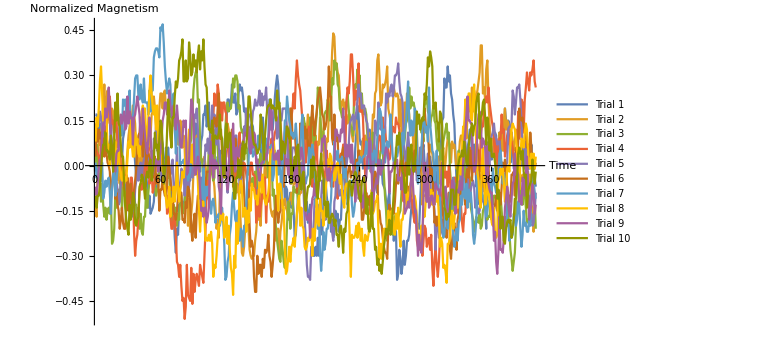

0.121901

```mathematica
magnetism1={34,34,24,18,28,26,20,20,34,32,44,32,38,30,12,34,32,30,24,24,18,16,6,-8,2,18,22,34,34,34,32,40,26,20,22,12,2,-8,2,4,-4,14,30,12,6,-14,-6,-14,-28,-20,-32,-30,-28,-24,-10,-18,-16,-10,0,0,18,14,0,-6,12,2,12,0,-8,-24,-36,-32,-48,-58,-42,-46,-26,-26,-26,-24,-28,-22,-12,-16,-2,-6,-10,8,-4,4,-2,28,12,4,2,-4,16,20,34,34,40,26,32,42,22,14,10,6,4,0,0,6,4,10,0,-2,-6,8,24,30,44,44,38,42,54,42,42,48,34,36,48,54,50,52,46,36,38,30,34,18,16,26,28,26,16,8,6,-26,-16,-14,6,16,32,18,18,12,8,18,44,44,24,24,34,46,54,60,54,38,0,0,16,8,-26,-14,-16,-36,-24,-18,-28,-20,-30,-48,-46,-32,-20,-12,-6,-4,-4,-14,-16,-24,-24,-38,-32,-26,-40,-50,-60,-60,-54,-60,-48,-60,-40,-36,-46,-26,-6,-10,-20,-26,-30,-26,-44,-36,-48,-42,-30,-36,-32,-44,-36,-36,-18,-4,8,-2,4,12,14,6,4,2,2,-8,12,22,40,34,18,14,16,-2,0,14,8,10,16,24,10,14,0,-14,-6,-14,-18,-8,0,4,-2,-12,-14,-16,-24,-34,-22,-18,-42,-34,-38,-50,-42,-44,-76,-72,-56,-62,-72,-66,-50,-66,-60,-50,-50,-46,-36,-28,-16,-24,-32,-28,-38,-40,-42,-24,-8,10,14,2,0,-24,-14,0,6,0,-2,-10,-16,-12,-4,-14,6,4,16,30,32,58,52,52,66,56,60,48,44,34,28,8,-10,-16,-20,-12,-4,-16,4,-2,-10,-20,12,16,24,24,6,10,14,4,-14,-12,-24,-26,-20,-22,-22,-26,-28,-42,-8,16,14,6,4,14,16,22,20,-2,10,22,10,16,28,10,38,30,24,30,28,2,22,14,-2,-2,-12,-4,-6,6,4,0,10,12,8,0,-4,0,-2,4,14,2,-12,-8,-14}/200;
magnetism2={-28,-34,-2,20,14,20,30,42,54,38,42,50,32,28,34,38,36,18,16,-10,2,-8,-12,-8,8,4,-20,-8,-2,10,20,26,32,32,40,34,28,10,-2,-4,12,4,-8,8,26,10,10,12,10,12,20,34,36,46,38,24,28,20,38,48,48,38,48,50,38,38,36,28,20,14,32,28,26,28,26,14,14,30,28,12,20,12,-10,-18,-40,-22,-44,-32,-24,-4,-6,16,20,16,18,8,4,2,4,6,0,-8,-16,6,16,20,4,-8,-14,-28,-42,-36,-48,-16,-4,6,12,6,14,24,28,24,8,0,4,-12,-12,-10,-18,-12,-18,-24,-40,-58,-60,-54,-42,-36,-26,-42,-56,-60,-62,-60,-60,-50,-44,-32,-36,-18,-40,-22,-22,-12,4,-8,-6,2,-14,-28,-32,-34,-30,-50,-42,-42,-42,-58,-44,-38,-30,-24,-22,-28,-30,-34,-24,-22,-18,-26,-12,-12,0,-12,-8,-20,-18,-18,-4,4,28,14,24,34,20,22,24,28,2,16,20,4,16,14,32,26,20,22,0,6,18,16,34,62,56,76,88,86,68,68,62,60,46,36,42,44,38,42,30,28,34,34,24,20,16,28,30,30,20,2,10,8,6,18,10,20,16,14,22,12,0,16,34,32,48,50,70,74,60,40,42,54,52,54,58,66,38,34,30,26,38,52,48,46,48,46,26,44,22,16,24,42,32,48,40,34,22,28,24,10,24,28,22,-6,0,-2,2,-26,-20,-20,-20,-6,-4,6,14,10,8,2,-2,-2,4,6,-12,-6,10,8,12,-4,2,12,18,16,14,2,16,12,14,6,-2,2,4,16,20,20,12,26,32,18,34,36,46,36,52,36,50,42,46,50,56,62,80,80,48,52,44,64,70,44,28,18,14,18,6,14,-10,-6,8,22,20,20,10,30,38,24,30,28,22,24,22,16,10,16,24,22,2,-18,-8,-10,-6,-18,-8,-10,-4,-4,-12,-6,-26,-28,-44,-36,-36}/200;
magnetism3={-2,14,10,-8,-6,-24,-12,-26,-34,-28,-36,-30,-28,-32,-22,-52,-50,-42,-20,-28,-20,-16,-22,-10,-30,-16,-10,-22,-18,-10,-12,-22,-22,-28,-24,-16,-26,-26,-36,-28,-42,-32,-44,-46,-34,-34,-16,-28,-18,-10,-6,10,2,-4,-14,-20,-16,-14,0,-6,6,-4,-2,-4,-4,6,-8,-4,-22,-30,-40,-26,-30,-28,-40,-32,-36,-18,-20,-32,-30,-24,-10,6,12,8,14,18,34,50,58,62,64,42,44,16,4,4,-16,-26,-24,-22,-14,14,8,-2,-6,-10,-8,24,16,14,-4,-10,-4,-10,10,6,24,40,42,36,38,38,46,58,52,60,60,56,38,40,26,22,24,16,8,12,10,-6,0,-12,-14,-8,-14,-4,-14,-4,4,2,8,2,0,2,12,10,2,-8,-6,0,6,-20,-16,-30,-42,-50,-56,-62,-64,-50,-56,-64,-68,-60,-40,-24,-26,-42,-32,-32,-14,-16,-18,-16,-24,-16,-14,0,2,32,28,22,18,10,6,32,16,26,24,14,26,34,52,46,38,18,10,20,34,36,36,44,40,30,42,58,54,70,64,68,54,52,38,36,32,32,32,28,42,48,38,30,26,24,20,48,54,52,64,56,60,36,48,34,36,38,34,20,4,12,-4,0,22,0,8,0,4,-4,4,10,10,10,-6,-20,-30,-50,-32,-38,-42,-40,-46,-36,-34,-32,-34,-34,-32,-30,-18,2,12,18,28,30,36,52,38,46,40,42,38,30,30,32,30,30,22,22,16,40,42,46,36,34,26,32,34,40,30,28,16,10,18,8,4,6,16,20,24,28,18,22,-2,-12,-18,-30,-8,-18,-22,-2,10,-4,-14,-8,6,8,-8,-6,-6,-6,-8,-28,-32,-36,-44,-38,-34,-36,-38,-32,-42,-40,-30,-28,-24,-28,-36,-34,-34,-20,-22,-26,-20,-20,-22,-30,-16,-20,-20,-30,-40,-50,-48,-34,-40,-30,-44,-56,-62,-70,-64,-58,-40,6,-8,-4,-22,-18,-26,-16,-18,-28,-38,-36,-36,-20,-22,-16,-14,-20,-42}/200;
magnetism4={14,10,8,6,-2,14,20,20,8,8,26,36,42,46,34,28,30,22,28,34,12,20,16,-6,-2,-12,-16,-12,-6,-12,-14,-24,-8,-8,-18,-44,-60,-50,-46,-34,-16,-12,-16,-12,4,6,-8,2,12,-12,-8,-4,-18,-14,-10,4,2,-2,14,18,-6,-4,2,-4,-12,-32,-20,-30,-34,-42,-42,-34,-32,-48,-64,-66,-74,-66,-80,-90,-88,-102,-94,-66,-86,-88,-90,-68,-92,-72,-84,-76,-72,-76,-80,-66,-70,-74,-78,-60,-42,-16,-10,-22,-4,0,6,32,48,40,40,54,48,34,42,30,42,42,36,34,14,6,4,2,6,0,-18,-10,-4,-6,16,22,2,12,-8,2,0,-6,-12,-30,-10,2,2,-6,-6,-8,-38,-28,-16,-34,-28,-22,-10,-8,-8,-38,-20,-24,-14,14,18,4,16,22,24,30,32,34,28,18,10,8,22,26,26,12,-4,4,32,38,48,38,58,70,60,54,50,40,30,22,14,2,12,24,26,22,6,-14,-4,0,16,12,-6,-10,-8,2,0,-6,-8,-2,10,-8,4,-2,-14,-12,-14,-2,0,-14,-22,-8,6,8,6,14,14,10,42,52,48,56,74,74,60,40,50,44,46,68,36,36,38,32,10,-6,-24,-30,-32,-32,-26,-28,4,14,10,6,0,16,20,18,10,32,12,26,16,16,8,4,8,18,26,24,22,32,28,28,24,10,-6,-20,-24,-14,-18,-14,-24,-24,-20,-10,-28,-34,-38,-32,-50,-54,-56,-48,-44,-60,-50,-40,-42,-54,-50,-48,-56,-46,-68,-80,-62,-54,-66,-74,-64,-46,-36,-18,-8,-4,-8,-4,-14,0,-8,-22,-20,-16,-12,-8,-20,-30,-32,-30,-26,-38,-44,-32,-32,-18,-14,-14,12,8,2,-4,2,-2,-6,0,10,-4,20,26,26,40,42,46,42,52,42,36,30,26,18,6,18,4,-2,18,18,34,22,24,6,10,20,24,14,16,16,12,6,0,10,6,36,18,30,44,42,22,44,52,62,56,50,62,60,64,70,56,52}/200;
magnetism5={18,26,30,28,36,32,24,10,16,24,22,10,8,16,20,16,6,4,2,-10,-16,-26,-24,-10,-10,-10,-8,-16,-8,-18,-26,-18,-26,-34,-28,-30,-16,-10,0,-10,-6,2,-8,0,4,10,24,4,6,4,-2,-4,-4,18,16,26,10,16,12,-2,-8,-12,4,-14,-2,4,4,-2,-6,-2,4,-14,-22,-10,12,-8,-24,-14,-2,-4,-4,-20,-4,-4,-20,-14,-4,6,-8,4,34,32,38,24,4,-20,-8,-18,-4,2,14,10,18,8,20,24,40,26,34,24,14,32,12,2,0,-10,0,4,10,-10,-18,-10,-10,-4,4,18,18,20,20,4,2,-16,-18,-2,6,26,22,38,18,32,34,34,26,36,38,44,40,40,44,50,40,48,40,46,44,52,36,36,32,24,30,34,38,32,32,18,20,40,30,30,38,38,38,38,22,0,-8,10,2,12,12,12,8,4,-10,-2,-8,2,-6,-16,-36,-48,-66,-74,-74,-76,-54,-54,-48,-22,-24,-28,-26,-34,-40,-22,-10,-18,-18,-36,-28,-24,-26,-28,-40,-44,-50,-24,-20,-2,-4,-18,-20,-16,-16,-18,-22,-8,0,6,12,28,30,32,34,24,32,36,44,54,46,48,38,40,40,34,30,28,18,18,16,6,-8,4,30,24,20,42,36,24,28,16,22,22,48,42,48,46,52,54,46,50,60,60,62,68,56,48,46,42,16,8,-2,12,22,12,6,6,-6,0,-4,4,-10,0,-2,12,4,22,-4,-6,-2,0,8,4,-6,-22,-18,-22,-30,-56,-34,-38,-48,-46,-44,-36,-42,-28,-36,-28,-32,-24,-36,-30,-22,-8,-16,-12,-28,-6,0,-10,-8,10,2,20,16,6,-6,-16,-22,-16,-12,-10,-14,-28,-24,-28,-32,-30,-24,-24,-10,-16,-18,-8,10,2,0,16,20,22,28,20,18,14,16,16,6,-2,-10,-6,-8,0,2,24,26,26,28,50,46,34,42,52,52,54,44,30,12,0,-2,16,0,-16,-26,-36,-32,-40,-38,-30,-18}/200;
magnetism6={6,28,16,24,18,22,16,18,6,26,8,2,0,-4,-22,-14,-4,2,-22,-18,-26,-30,-42,-36,-28,-38,-42,-42,-26,-8,-30,-16,-12,-26,-24,-18,-10,-2,10,20,22,32,16,6,26,26,0,8,8,6,4,0,-8,0,6,-12,-6,-10,-30,-16,-16,-8,-16,-20,-20,-14,6,0,-8,-16,-16,-32,-32,-36,-30,-20,-14,-18,-18,-36,-36,-38,-24,-28,-14,-16,-24,-42,-50,-38,-32,-48,-30,-20,-20,-22,-22,-28,-26,-16,-12,-4,-4,-4,-4,6,6,28,32,28,26,38,48,18,24,8,8,2,10,-8,-4,-10,2,14,24,-14,2,18,10,6,-6,2,-2,-6,2,-18,-32,-40,-26,-16,-40,-54,-50,-54,-74,-84,-84,-60,-72,-66,-66,-74,-62,-68,-56,-58,-56,-46,-60,-64,-74,-66,-56,-38,-20,-30,-38,-32,-30,-14,-8,-14,8,26,20,20,18,38,38,18,20,22,12,-18,-4,-4,28,24,22,18,26,18,24,16,4,10,30,40,28,20,30,36,44,48,52,44,34,32,24,26,30,40,66,46,46,18,14,34,16,20,18,-4,-8,4,8,12,2,-6,-16,-6,-2,0,-8,-4,-4,-4,0,4,-6,10,-12,-16,-36,-36,-30,-22,-18,-22,-26,-20,-30,-28,-26,-10,-4,-6,-8,-30,-30,-38,-40,-48,-54,-58,-58,-62,-42,-26,-42,-34,-28,-32,-24,-12,-6,-12,-4,2,8,6,-4,-12,2,-14,-14,-24,-18,-20,-8,4,10,-2,-4,-6,-6,-2,6,12,28,38,28,22,24,8,-6,-2,-4,-20,-38,-34,-40,-34,-38,-34,-24,-28,-34,-42,-42,-48,-28,-18,-56,-62,-50,-42,-38,-44,-56,-36,-32,-26,-12,-20,-16,-20,-26,-6,-2,-8,4,10,-10,2,2,4,16,14,4,-22,-12,0,-14,-12,-16,-16,-4,0,-14,-20,-36,-30,-30,-26,-20,-28,-34,-18,-26,-14,2,-4,4,-2,-14,-30,-20,-24,-6,-6,-4,-20,12,2,14,38,32,30,32,26,24,20,12,14,6,22,12,-2,-2,-2,2}/200;
magnetism7={2,-8,-2,-8,-8,-10,2,-22,-18,-10,-14,-10,-8,-18,-32,-16,-6,-2,-20,-10,-2,10,32,24,20,44,40,44,34,38,36,50,22,30,32,44,58,60,60,46,44,54,46,42,58,42,42,42,34,50,36,50,50,72,76,78,78,76,72,92,90,94,82,66,56,48,54,58,54,32,38,48,26,8,22,30,20,0,2,2,4,0,-6,0,-10,-8,-4,6,4,6,-2,4,18,2,-10,-10,-20,-22,-2,-28,-14,-20,-14,-14,-24,-32,-24,-22,-28,-38,-34,-34,-32,-40,-36,-28,-38,-52,-76,-74,-64,-60,-46,-40,-26,-18,-28,-36,-38,-30,-40,-50,-42,-44,-54,-40,-42,-26,-6,2,22,24,20,6,8,10,14,10,20,12,12,14,8,2,14,18,16,12,12,12,14,-10,-6,10,8,2,-6,2,-6,-22,4,10,30,30,46,38,30,26,20,22,18,20,28,16,6,8,8,26,34,8,-8,-12,-8,-6,12,2,10,14,8,-2,-26,-18,-42,-32,-58,-70,-60,-44,-56,-52,-42,-42,-36,-30,-22,-4,-8,16,6,4,10,0,4,4,6,-2,-8,-2,-10,-26,-22,-18,-10,-26,-34,-30,-22,-16,2,-2,6,2,4,6,6,8,16,8,-2,0,6,8,4,10,10,2,18,28,38,36,30,8,24,2,8,16,12,14,34,20,6,2,-2,12,6,10,16,18,4,22,14,24,28,42,56,30,20,30,20,22,38,36,20,-12,-2,0,8,24,32,28,22,26,16,52,28,20,10,8,-10,-2,10,-4,-26,-20,-38,-42,-48,-46,-20,-28,-42,-28,-18,-24,-38,-46,-54,-48,-42,-50,-38,-36,-20,-26,-8,-20,-22,-12,-28,-16,-24,-18,-28,-46,-52,-46,-36,-4,-12,-16,-10,-18,-20,-22,-24,-34,-30,-24,-24,-10,-18,-2,-12,-14,-18,-12,-8,8,10,0,-12,-6,-10,-20,-36,-36,-50,-44,-48,-46,-32,-34,-40,-36,-24,-26,-42,-54,-46,-30,-40,-38,-44,-44,-36,-40,-22,-12,-10,-18,-22}/200;
magnetism8={16,32,26,38,56,66,48,30,32,34,32,10,14,0,12,12,2,2,16,0,4,10,-2,-6,-10,0,-12,-8,-10,4,16,12,30,14,6,6,22,14,18,8,6,20,36,40,36,38,18,16,32,50,60,48,38,34,40,24,40,18,10,22,24,-4,-4,-16,-22,-28,-26,-14,-34,-22,-24,-14,-24,-16,2,-14,-24,-16,-12,-4,-8,-2,12,2,14,24,6,2,14,0,0,0,0,-10,-30,-44,-30,-24,-24,-36,-50,-48,-50,-46,-50,-44,-52,-74,-66,-68,-60,-48,-40,-38,-30,-36,-32,-48,-46,-34,-52,-40,-56,-68,-72,-86,-60,-68,-38,-52,-42,-14,-10,-14,-34,-30,-28,-44,-30,-38,-22,-30,-12,-16,-16,-22,-20,-26,-20,-10,-2,-18,-6,-18,-24,-26,-22,-18,-10,8,10,12,16,6,6,-14,-30,-12,-12,-18,-28,-28,-54,-72,-70,-62,-54,-64,-54,-52,-48,-54,-42,-32,-24,-20,-40,-28,-40,-42,-54,-56,-54,-48,-50,-44,-42,-60,-42,-50,-38,-22,-38,-40,-22,-30,-30,-40,-34,-18,-8,4,0,8,6,-2,2,-10,-8,0,2,-6,-12,-6,-18,-24,-28,-14,-12,-12,-26,-48,-74,-46,-48,-48,-46,-40,-48,-38,-42,-50,-42,-54,-60,-46,-48,-50,-46,-40,-34,-16,-32,-30,-24,-24,-20,-42,-62,-52,-62,-52,-42,-42,-46,-42,-30,-36,-38,-30,-34,-44,-46,-32,-42,-28,-44,-54,-36,-36,-30,-24,-8,-28,-18,-20,-12,-10,-18,-22,-20,-24,-36,-48,-54,-48,-40,-44,-30,-34,-24,-6,-6,-16,-20,-16,-26,-18,-26,-16,-24,-20,-34,-54,-48,-52,-68,-66,-70,-78,-52,-52,-48,-34,-30,-42,-36,-28,-28,-28,8,-4,-6,10,26,24,44,38,36,48,48,32,30,42,54,32,14,-4,-10,-22,-28,2,12,-6,-26,-24,-12,-16,-24,-30,-38,-40,-28,-46,-48,-46,-10,-8,-2,-6,-2,-12,-24,-18,-2,0,-4,14,24,28,26,24,18,10,-4,-16,4,18,16,12,22,28,24,10,0,-2,8,-4,8,-2,6}/200;
magnetism9={-14,-20,-12,-2,4,2,22,28,24,38,32,38,52,38,20,6,-2,0,-4,8,10,10,26,34,28,32,36,24,26,46,28,36,32,32,14,32,34,40,46,40,34,14,18,38,28,20,12,8,18,32,22,4,-6,-2,2,4,4,-4,6,8,18,30,34,42,42,34,34,50,40,36,32,40,30,24,40,30,26,14,12,18,30,26,30,-6,-4,4,26,44,42,30,-4,-6,0,6,-4,-16,-30,-28,-34,-28,-28,-38,-34,-28,4,16,2,-8,4,-2,2,0,-14,-18,-32,0,6,10,16,-6,-16,-2,12,18,4,28,8,-4,12,10,6,12,14,14,16,18,22,20,24,26,10,8,26,12,22,20,2,4,-6,-10,-4,2,2,6,8,4,8,16,24,40,34,16,4,4,8,4,10,0,10,14,14,10,16,0,4,-6,4,-12,-8,4,0,-10,4,-14,0,10,4,12,8,2,-12,-32,-36,-36,-32,-48,-30,-22,-20,-12,-20,-20,-20,-12,0,6,18,16,20,10,-4,-10,-2,-10,-6,-4,0,0,24,24,20,20,16,24,22,38,24,6,14,6,10,14,2,14,0,-8,-24,-8,-10,-22,-20,-14,-20,-28,-20,-10,-8,6,6,18,-2,-6,-30,-18,-14,-10,-12,4,2,-6,-2,-2,4,8,12,10,4,-18,-4,-4,-2,2,2,0,4,-10,-8,-8,-16,-4,-10,-32,-30,-28,-24,-28,-20,-2,-8,-20,-28,-30,-44,-60,-46,-54,-58,-50,-18,2,-16,-24,-2,-28,-26,-20,-20,-26,-26,-12,-14,-16,-16,-20,-10,2,-18,-22,-14,-22,-30,-32,-28,-24,-10,-12,-16,-32,-16,-16,-18,-10,-16,-16,2,12,22,34,46,30,30,28,28,4,-4,-2,2,26,34,36,30,12,18,16,12,-6,14,-12,-16,-18,-18,-30,-50,-44,-64,-72,-58,-34,-56,-56,-58,-48,-28,-22,-14,-18,-32,-34,-22,-12,-10,8,-6,-4,-6,-24,-20,-26,-8,-8,-20,-6,6,-16,-36,-30,-26,-12,-18,-32,-26}/200;
magnetism10={-20,-28,-20,-20,-14,-4,8,14,14,22,10,10,8,4,20,12,-4,16,42,30,48,28,26,14,6,6,-12,-28,-36,-42,-46,-26,-36,-32,-18,-22,-38,-40,-36,-34,-14,-12,-6,-8,-14,-22,-8,-4,-8,2,4,-10,-4,2,22,12,14,4,18,30,28,14,-12,-4,2,22,44,36,22,12,32,32,46,56,52,58,70,72,76,84,56,56,70,56,58,82,74,60,62,74,66,70,62,74,80,64,76,70,84,66,54,52,34,24,24,22,30,8,20,20,18,18,22,34,20,18,-6,-8,18,28,12,20,22,14,-6,-8,-22,-22,-8,-8,4,-8,-6,10,16,4,14,12,24,46,46,36,28,18,14,14,12,8,10,12,34,28,18,4,20,30,38,40,40,44,38,40,38,38,30,50,38,42,30,4,16,14,8,16,26,24,20,14,-12,0,-2,6,0,12,14,0,-12,-16,-6,-4,-22,-30,-20,-14,-14,-12,4,-8,6,-2,-4,-18,-22,0,-10,8,-2,-8,-26,-24,-34,-24,-38,-38,-34,-32,-34,-40,-36,-46,-46,-54,-42,-40,-46,-58,-42,-44,-32,-30,-12,-10,-14,-20,-14,-6,-4,-6,-12,-18,-22,-24,-10,-10,-8,-18,-32,-22,-42,-44,-40,-18,-42,-42,-56,-54,-66,-62,-70,-66,-72,-64,-54,-48,-42,-46,-42,-36,-46,-44,-30,-18,0,8,20,14,22,14,4,-4,-6,-18,-18,-8,12,-6,10,14,2,-4,0,8,36,28,34,24,28,32,30,48,44,54,72,66,76,72,66,38,38,42,30,28,16,36,34,26,-18,-28,-30,-36,-32,-34,-30,-16,-16,-16,-26,-26,-14,-2,2,6,6,10,6,16,10,2,0,12,20,24,28,20,26,28,42,46,48,18,32,34,42,44,32,14,32,26,10,18,6,6,8,2,-4,-22,-16,-24,-42,-34,-34,-50,-52,-42,-38,-36,-38,-36,-48,-44,-36,-22,-22,-10,8,12,8,4,10,-4,-8,-6,-28,-18,-14,-12,-10,4,-4,-12,-4}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT25=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

The domains here look to be much smaller.

### Large Lattice: 200 long, kT=3, 400 time steps

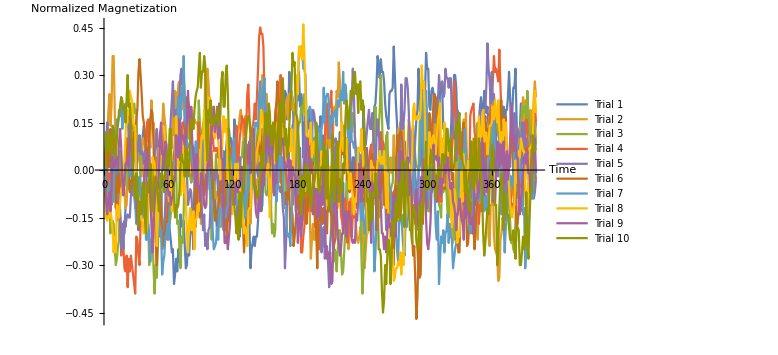

0.11144

```mathematica
magnetism1={-4,-4,8,16,2,14,-18,-14,-14,4,-2,0,-20,-28,-30,-40,-34,-40,-40,-24,-16,-6,28,14,12,4,2,14,6,10,20,10,8,4,12,22,28,22,6,-18,-10,-8,4,-24,-14,-6,-10,-2,-28,-24,-40,-24,-26,0,26,30,18,2,-12,-18,-38,-44,-52,-50,-72,-66,-56,-64,-50,-58,-28,-34,-36,-32,-48,-62,-60,-44,-54,-42,-38,-34,-34,-10,8,-4,2,6,-6,-16,-12,-16,-14,-6,16,18,14,0,6,-14,-16,-10,-14,-28,-40,-24,-12,0,12,-10,12,-4,10,18,26,26,18,20,0,6,32,18,18,0,-32,-42,-30,-12,-14,-22,-22,-40,-36,-30,-34,-62,-50,-46,-42,-48,-42,-42,-32,-6,-6,-26,-22,-2,18,22,28,26,28,-2,-8,-10,-14,-10,8,28,28,26,24,20,34,34,44,50,48,32,34,62,52,48,46,30,32,36,50,44,62,40,48,44,8,30,20,16,28,38,26,32,-2,4,8,8,18,0,-4,8,34,4,22,16,4,14,26,2,-6,-2,-12,-42,-24,-2,-12,-6,-8,12,24,-18,-32,-8,-34,-28,-18,6,28,20,-2,-6,8,8,-8,-10,-8,14,4,-14,-12,10,40,14,14,10,4,-2,2,6,14,20,40,42,54,72,66,58,70,62,62,56,42,34,30,26,48,50,50,52,78,60,42,30,-2,-16,4,2,-8,-4,18,-14,-8,-12,-10,-16,-18,-16,-6,2,20,32,38,64,50,12,10,24,36,48,74,64,64,40,38,50,52,48,36,8,6,34,30,50,52,50,26,26,2,-6,4,-6,10,24,38,42,60,60,52,30,30,4,-16,-20,-12,-12,-28,-22,-22,-14,-12,-16,-8,-14,-20,-22,-22,4,14,24,40,46,38,32,50,42,36,40,26,8,-2,12,-2,0,12,24,28,24,16,26,22,24,40,16,38,38,46,62,46,22,36,52,52,64,32,12,22,24,42,42,42,32,12,20,18,0,-14,-2,10,20,6,24,30}/200;
magnetism2={-4,16,16,36,48,28,40,72,72,38,2,-24,-20,-24,-16,-2,-2,2,-12,-24,-22,-4,12,10,-2,22,34,12,10,0,6,8,12,-4,-4,20,20,16,20,28,18,28,14,44,26,30,20,-6,-8,2,10,8,16,24,42,34,28,14,4,6,4,26,14,38,22,50,48,30,54,56,50,38,58,60,48,40,20,20,40,34,38,30,26,32,30,30,28,-2,2,-34,-26,2,18,62,38,64,56,40,2,12,-8,-8,-12,-18,-14,-20,-34,-36,-12,-28,-12,-22,-20,2,-32,-24,-6,-24,-22,-14,0,4,12,24,26,34,38,32,28,8,34,-4,-14,-6,-6,-34,-16,4,8,-18,-22,-6,-6,26,40,36,60,38,28,32,48,24,10,2,2,-14,-10,-14,-14,-2,-2,8,0,2,24,28,28,32,38,46,32,48,38,50,38,42,36,28,14,-4,4,2,-24,-4,-16,-16,-2,22,-2,-4,-26,-56,-44,-34,-44,-44,-32,-20,0,-6,-14,-18,-8,-12,6,10,30,24,14,30,14,8,34,40,34,50,46,68,56,38,14,10,28,20,2,-16,-50,-42,-18,-30,-16,-26,-26,-36,-44,-46,-42,-36,-40,-28,-58,-62,-50,-40,-20,-2,-6,-4,-10,-22,12,8,-10,-28,-30,-26,-10,-24,-2,6,-8,22,10,-4,2,8,-2,2,22,0,8,6,26,24,30,28,14,28,10,6,0,18,32,26,-4,-12,-8,-12,-28,-44,-52,-64,-34,-20,-14,8,0,-14,12,16,18,4,26,10,10,16,28,38,20,40,44,8,16,12,-4,-4,6,-6,-10,-24,-16,-8,-42,-46,-34,-14,6,-12,16,4,4,20,18,32,2,36,4,2,-8,-20,-4,0,-6,-34,-40,-32,-44,-16,-22,-4,10,20,-14,-4,-14,-8,-42,-48,-22,-22,-6,-42,-50,-52,-54,-70,-68,-44,-40,-30,-34,-26,-8,-18,-14,-12,-14,-18,-10,-16,-12,-12,6,14,16,26,28,34,46,26,44,42,38,22,34,38,16,30,46,56,46}/200;
magnetism3={-6,-12,8,-18,-18,-40,-32,-32,-34,-50,-60,-56,-48,-44,12,6,-4,-2,0,16,8,-8,-12,26,40,26,34,42,36,38,16,20,12,-10,-26,-26,-30,-18,-8,-10,-32,-60,-44,-46,-40,-62,-78,-60,-68,-50,-28,-28,-12,-34,-40,-32,-28,-26,-20,-22,-34,-28,-24,-10,-4,16,2,-34,-32,-46,-62,-42,-46,-26,12,4,8,2,0,-4,-8,-6,2,-4,0,0,12,44,30,22,20,28,34,36,20,0,-4,-8,-26,-44,-28,-16,-8,10,-2,-4,-12,-6,-16,-12,-38,-24,-22,-8,8,0,6,-2,6,4,8,8,-10,-2,-26,-2,8,8,18,8,-18,-24,-32,-6,4,-18,4,16,18,6,6,20,30,14,14,4,14,18,8,-14,-16,-14,-8,-22,-22,-40,-34,-42,-38,-10,6,-4,4,-8,2,2,-2,2,-16,-22,-8,0,-8,2,2,8,12,2,6,24,30,30,40,36,42,48,32,24,10,16,14,6,18,20,10,20,22,28,10,6,22,-18,-22,-6,-20,-32,-26,-26,-4,-2,-14,-32,-58,-50,-52,-64,-50,-38,-38,-52,-66,-64,-52,-38,-16,2,34,24,28,24,36,34,20,10,4,-6,-10,-18,-54,-78,-60,-56,-32,-12,-12,-22,-30,-20,4,22,10,40,26,22,26,38,60,36,10,-2,16,18,24,-2,-16,-14,-10,-8,8,6,8,4,-28,-30,-28,-32,-36,-28,-32,-10,-2,-18,-24,-6,-2,-2,18,20,8,2,2,0,28,44,22,30,6,4,-14,-6,-26,-26,-6,-2,4,8,-4,-4,-10,-16,-22,-24,-30,2,-14,-2,-10,-14,-28,-30,-16,-18,-14,-22,-40,-44,-32,-6,-4,20,16,6,-4,-16,-4,14,-6,0,-10,-18,-24,-6,-20,8,4,28,30,18,14,18,20,18,0,-4,-12,-4,22,34,18,14,46,46,28,36,26,22,28,30,0,-10,-4,-16,-22,-16,-22,-22,-32,-46,-44,-50,-52,-32,6,-4,-18,-2,18,40,40,36,40,32,50,36,24,12,24,32,30,30,18}/200;
magnetism4={4,12,-4,-8,-2,-18,-22,-14,-2,-10,-10,-32,-24,-18,-30,-54,-40,-48,-62,-64,-54,-74,-56,-64,-54,-60,-66,-72,-78,-42,-44,-54,-60,-34,-28,-20,-26,8,18,30,32,0,-2,0,-20,-8,4,-8,8,2,16,24,6,22,12,6,-2,-22,-44,-34,-14,6,2,-2,10,12,12,8,10,22,28,18,30,28,32,34,14,10,10,8,8,-4,8,14,-6,12,0,30,14,18,18,12,28,8,2,4,16,40,14,20,22,12,14,12,14,8,12,-14,-20,-30,-16,-30,-38,-32,-22,0,-16,14,2,18,8,4,28,6,8,20,26,34,30,32,22,26,48,54,34,20,24,28,32,42,32,46,64,84,90,86,86,78,46,40,34,34,30,28,22,28,12,-6,32,42,20,4,24,60,30,38,36,8,-2,-8,-14,-12,6,-4,-22,-4,-2,-10,-4,-22,-28,-18,-52,-52,-42,-36,-16,-14,-26,-6,-8,-26,-26,-18,-16,-36,-16,-30,-36,-50,-32,-14,-8,10,18,42,42,20,42,40,50,28,6,14,10,-6,-12,0,-6,-28,-32,-40,-30,-18,-34,-46,-40,-20,-32,-42,-28,-30,-16,14,10,-8,-10,-6,-8,6,-12,-16,-14,0,-20,-4,12,16,0,10,2,-4,-24,-6,-2,22,24,12,18,6,-18,-24,-26,-16,-20,-14,-14,-30,-14,-12,-10,-26,-22,-30,-30,-24,-8,-4,-6,-12,-12,-8,-28,-12,-18,-20,0,0,-34,-24,-30,-34,-40,-34,-32,-14,-20,-10,-22,-22,-10,2,-4,-14,-8,-12,-4,-20,-6,0,-20,-2,-20,8,4,2,-2,12,18,16,2,0,12,24,56,46,18,10,30,14,10,-24,-34,-34,-12,-10,0,6,-8,34,38,40,42,24,20,2,-20,-34,-22,-26,-12,8,14,30,8,22,14,30,46,48,56,72,62,64,60,56,76,54,34,12,-4,-10,6,4,6,-2,-10,-20,-24,-22,-20,-4,0,-8,-10,-26,-26,-14,-16,12,22,32,30,0,-4,12,12,4,30,42,30}/200;
magnetism5={-2,16,30,18,16,16,12,2,-2,22,12,-12,4,-12,-26,-50,-34,-50,-32,-36,-30,-28,-30,-30,-16,-10,-16,-8,-24,-10,18,12,22,10,12,10,4,12,4,10,14,18,-10,2,-18,6,10,18,26,6,-26,-14,-14,-50,-44,-38,-20,8,-14,-6,18,32,44,56,34,36,38,30,46,44,60,64,54,60,26,26,-2,-22,-18,-12,-14,-26,-50,-36,-16,-4,-10,-12,-8,-18,-28,-38,-28,-48,-40,-50,-38,-36,-22,-18,-14,0,-6,0,-2,-16,-4,-10,-16,-26,-22,-20,-22,-28,-24,-18,0,4,-8,-20,0,2,-4,-30,-12,8,-2,-14,-14,-16,20,8,16,14,14,20,4,16,-4,8,8,0,-4,4,4,6,16,10,18,40,32,28,34,20,4,6,24,30,6,-14,-8,-10,-12,-14,-10,-24,-30,-62,-46,-20,-16,26,26,18,28,30,36,-4,-22,-10,0,14,-10,-18,-2,16,34,4,2,6,16,2,16,38,36,30,18,-2,14,-2,-26,-52,-44,-36,-56,-48,-48,-58,-74,-46,-36,-12,-6,-2,20,10,-4,-22,0,10,24,28,18,8,8,-2,0,12,30,44,64,48,20,8,10,-4,0,-2,10,6,10,24,16,24,32,38,26,26,36,22,14,-14,22,32,24,16,-2,2,2,-22,-14,-38,-36,-30,-28,-32,-18,-26,-42,-16,-12,-20,-16,22,12,54,26,28,38,58,58,52,36,6,4,24,28,18,-4,-10,-24,0,2,6,10,-6,2,-4,-14,-24,6,10,16,14,32,36,30,46,30,44,60,52,54,56,46,48,64,58,58,52,58,58,30,34,20,24,6,38,34,22,24,16,-6,-22,-20,-28,-16,-28,-12,-14,-2,-18,-12,-16,-2,2,4,20,38,16,18,18,38,38,54,80,64,56,42,62,44,48,32,6,4,-4,24,16,6,12,2,-32,-16,-2,-22,6,2,24,28,20,36,22,28,26,24,18,-6,30,4,30,16,18,10,14,6,2,22,6,-18,-14,-6}/200;
magnetism6={-8,14,20,2,2,26,20,20,20,0,-24,-4,-14,-2,-14,-14,-6,-10,-10,10,20,6,14,-14,-8,-6,0,24,24,32,38,62,70,60,48,34,30,22,14,12,2,22,32,38,36,16,-22,-46,-60,-32,-8,-16,-28,-48,-48,-44,-38,-32,-34,-18,-18,2,0,0,4,22,24,28,36,40,26,16,10,12,28,18,46,44,40,22,38,10,12,2,-36,-26,-6,0,-30,8,12,-12,-16,-10,-4,10,26,4,12,6,-16,-20,-32,-28,-28,-24,-18,-8,-14,0,-8,0,-22,-44,-30,-32,-18,-6,-10,12,-2,2,-18,-18,-16,-30,-10,-20,-34,-52,-40,-32,-32,-28,-14,-4,-6,-4,-6,2,2,14,20,14,10,16,26,2,14,0,8,18,10,8,4,0,8,18,36,42,56,44,32,4,-10,-16,-14,-22,-14,-18,-18,-12,-40,-24,-28,-48,-42,-32,-22,-16,-24,-12,-10,-32,-22,-18,-18,-34,-22,-14,2,20,6,-4,-20,-28,-38,-62,-32,-20,-32,-24,-34,-24,-26,-26,-40,-16,-14,-26,-28,-40,-50,-46,-42,-16,-4,-16,12,22,10,16,8,14,20,-6,6,-14,-8,-10,-2,-24,-16,-16,-24,-16,-2,4,-6,-28,-24,-14,-2,-6,-10,-20,2,8,10,-4,-12,4,-14,-16,-18,8,-14,-10,4,-2,-22,-22,-28,-20,-18,-34,-30,-32,-60,-16,-4,22,12,22,24,24,18,-2,-2,-6,0,-2,-8,-26,-10,-42,-54,-48,-70,-94,-80,-48,-68,-66,-26,-34,-6,34,28,20,18,36,28,14,28,46,48,44,36,2,-8,2,-2,14,-6,-12,4,18,4,0,18,4,-6,-2,-30,-18,-26,-42,-52,-52,-26,-20,26,30,16,-6,-48,-46,-34,-20,-28,-40,-36,-50,-36,-20,12,2,10,14,6,6,28,34,24,26,26,12,6,-10,8,32,28,-2,0,8,8,44,44,22,16,26,34,8,0,6,8,22,26,-8,-22,-14,-36,-34,-24,-8,-4,-10,-22,-6,-6,14,12,14,6,4,-18,-12,-8,2,-6}/200;
magnetism7={8,-18,-22,-30,-12,-6,-20,-20,-20,10,18,32,28,38,34,46,26,40,38,42,34,34,26,-4,8,-4,2,-16,-22,-34,-18,-20,-4,-22,-20,-10,-30,-22,-44,-44,-34,-40,-58,-44,-46,-26,-22,-14,-2,-16,-36,-42,-38,-66,-58,-54,-42,-42,-34,-44,-24,-14,-6,-4,6,0,32,26,46,42,32,52,44,72,36,28,18,16,14,14,6,16,2,-6,18,18,4,-4,0,-2,2,24,28,18,26,8,4,-12,-12,-26,-40,-50,-48,-46,-36,-44,-26,-24,-24,-36,-30,-30,-30,-24,-22,-2,10,-2,-10,14,20,-10,-22,-10,-12,-10,-24,-10,-14,-22,-30,-14,-18,8,-8,-14,-12,-2,-6,30,28,30,26,48,56,34,36,52,58,36,20,-6,-16,-18,-24,4,12,0,2,-20,-12,-6,14,10,0,8,-22,-24,-24,-40,-42,-40,-48,-30,-10,-4,30,24,46,52,74,76,78,76,64,64,60,34,32,36,40,38,26,6,20,10,16,28,24,26,12,26,30,52,30,46,48,48,40,20,34,30,36,34,38,28,44,40,46,50,44,62,42,54,48,26,18,30,40,18,18,14,14,12,4,14,-10,-24,-32,-20,-30,-40,-40,-6,-12,-24,-20,-26,-16,-34,-64,-52,-34,-6,-8,-2,10,12,2,2,0,-16,-6,-2,-10,-12,-42,-28,-34,-34,-40,-50,-58,-32,-30,-28,-40,-50,-54,-32,-36,-22,-2,-26,-24,-14,6,0,-24,-12,-14,-6,8,18,54,42,8,34,50,32,-10,-18,-10,-14,2,-2,-16,-36,-44,-26,-72,-56,-42,-46,-38,-52,-40,-38,-28,-46,-34,-42,-44,-62,-56,-50,-46,-24,-28,2,6,-12,-2,-4,26,10,-10,-22,-34,-40,-34,-30,-10,-14,-16,-12,-8,-20,-14,-18,0,4,-26,-16,-22,-28,0,16,-4,8,28,36,14,12,2,8,22,2,-28,-16,-34,-52,-36,-30,-16,-22,-4,-4,-10,-8,16,6,6,16,8,10,-8,-2,-28,-24,-62,-50,-46,-14,2,-8,-16,-18,-6,12,18}/200;
magnetism8={-14,-30,-32,-22,-30,-26,-30,-38,-52,-42,-52,-22,-24,-30,-20,-12,-10,-4,4,22,38,30,30,50,46,44,30,28,28,-16,-14,-18,-20,-26,-32,-34,-40,-30,-40,-36,-14,-12,-22,-30,8,6,4,-16,-48,-32,14,0,12,24,28,26,6,10,-8,-16,-20,12,-26,-26,-4,2,34,20,2,0,-16,-8,20,-14,-8,-20,-40,-52,-34,-24,-38,-38,-26,-50,-32,-30,-22,-26,-6,16,22,20,38,4,-2,12,22,46,40,36,40,22,20,24,38,18,12,-6,-4,20,34,24,32,24,-8,0,6,0,-28,-12,-14,4,-4,4,-18,-18,-12,-20,-32,-40,-36,-42,-48,-26,-24,-24,-2,4,26,0,6,12,16,20,22,38,32,28,0,-4,2,4,-6,-30,-8,-2,10,4,16,24,30,30,28,32,26,26,12,14,6,16,12,14,12,26,8,-8,16,36,60,48,78,78,72,70,92,74,50,22,22,16,20,30,8,12,18,8,12,4,-30,-26,-2,12,0,10,-4,-16,-22,-22,-18,2,-6,-4,-6,-2,-20,-22,-24,-22,10,18,30,12,20,10,20,0,-2,-12,-2,-10,-16,-28,-18,-20,-12,14,12,12,26,10,2,12,-2,-24,-40,-36,-4,6,2,2,-8,-18,-4,6,6,12,4,8,4,12,-4,-24,-2,-28,-32,-54,-52,-50,-70,-68,-62,-62,-58,-60,-52,-66,-52,-60,-40,-10,-10,-20,-30,-26,-4,8,38,42,32,32,34,34,32,38,66,52,56,32,-6,0,6,24,20,14,20,22,18,10,22,32,36,42,6,20,-10,30,26,22,24,-6,-6,-20,-36,-30,-12,-14,-28,-46,-42,-42,-18,0,-20,10,-4,-10,-2,6,2,-2,2,18,20,-2,-14,-8,-6,34,22,18,30,38,18,24,22,10,18,28,28,30,40,32,44,36,30,44,26,18,24,6,32,22,30,4,4,-10,-22,-26,-30,-24,-22,6,-8,-6,12,8,20,16,12,12,-8,-26,-28,-2,14,14,16,18,42,50,36}/200;
magnetism9={-6,-20,-28,-18,-14,-26,-8,8,2,2,8,8,2,18,26,14,-6,-16,-6,4,4,8,2,34,28,4,-10,-6,-4,-18,-32,-38,-20,-24,-26,-14,-8,6,6,10,-4,-2,-16,-34,-52,-32,-20,-10,-8,-12,-2,22,30,10,12,0,18,16,-10,-16,-14,-22,-18,-16,-8,-6,22,12,8,32,6,20,22,20,16,20,32,50,34,28,40,16,10,0,-10,10,-10,-10,-20,-2,-8,-10,-22,-24,-22,2,10,2,10,24,32,40,24,32,36,20,42,28,8,6,-26,-46,-46,-42,-50,-42,-34,-8,0,-16,-22,-8,-12,-14,-10,-6,-6,2,-14,2,14,12,12,4,18,-2,2,6,26,-12,-26,-30,-28,-12,-26,-10,6,-10,-2,4,28,18,10,22,24,22,-6,-16,-2,-8,12,10,20,16,16,20,8,0,2,2,10,-6,6,-8,2,-2,-4,-26,-28,-46,-32,-22,-42,-32,-22,-2,8,14,20,10,0,-16,-16,-28,-10,-16,-12,-30,-12,-30,-10,-22,-20,4,-26,-54,-56,-52,-56,-52,-72,-70,-44,-18,-10,-22,-44,-46,-54,-50,-40,-40,-28,-26,-42,-32,-26,-30,-30,-44,-46,-44,-46,-28,-32,-18,4,-6,-20,-12,-8,2,2,14,6,-8,-16,-46,-8,-18,-16,-8,-38,-20,0,-4,-24,-40,-40,-50,-42,-52,-40,-28,-36,-34,-42,-26,-16,-22,-42,-12,-14,-14,12,12,6,-16,0,-14,-14,8,-16,0,-10,-28,-30,-30,-20,-12,-30,-38,-36,-6,-4,-20,-18,0,-32,-46,-50,-44,-34,-14,-12,16,-10,-4,-20,-10,8,-10,-16,-6,-8,4,-2,4,8,0,-10,-12,-8,-20,-22,-28,-38,-28,-24,-18,-26,-32,-32,-44,-20,-30,-16,-22,-32,-34,-34,-30,-40,-4,0,4,-18,-14,-4,4,20,0,-16,8,-8,-14,-8,0,6,6,-20,-8,-22,-4,18,14,2,16,16,4,18,-8,6,12,-6,6,18,42,28,18,12,22,8,8,-24,-28,-20,-10,-2,8,10,4,12,-2,-2,-14,2,-2,10,20,-2}/200;
magnetism10={2,24,20,12,22,18,10,28,26,20,8,20,30,34,40,46,44,38,40,30,44,60,40,42,20,20,-2,-12,-18,-2,-6,-36,-20,-28,-26,-8,-12,-32,-40,-8,-14,-2,4,0,-26,-12,-10,-4,-10,-16,-26,-12,-2,-2,-6,-14,2,6,12,2,26,26,-8,-4,-16,-30,-22,-24,-22,-14,4,10,6,4,-4,14,10,-4,0,22,32,28,26,38,46,50,52,64,74,52,62,62,72,66,22,6,38,30,44,30,32,28,34,32,40,28,32,34,56,62,40,40,60,66,48,18,-6,-4,-10,-22,-22,-30,-40,-30,-44,-14,-36,-16,-12,4,-2,22,32,34,32,24,24,14,-8,-12,-10,-18,-14,-16,-4,12,0,2,26,36,30,22,42,36,16,16,30,26,22,6,24,32,42,10,42,58,40,16,26,8,14,28,40,52,74,66,68,36,34,30,12,-8,-28,-4,-18,-8,2,4,-16,-6,-2,-24,-18,-8,-10,-4,30,12,-10,-14,-6,2,0,18,12,-18,12,-14,-26,-20,-6,22,-10,-20,4,4,18,-20,-6,-10,-14,4,-2,30,44,40,26,32,50,50,46,60,62,48,54,36,54,56,38,44,40,20,2,-20,-18,-38,-14,-26,-32,-14,-16,-2,-10,-14,-50,-50,-54,-76,-90,-82,-60,-72,-54,-44,-48,-72,-56,-32,-40,-30,-20,-32,-10,-8,-32,-8,6,-12,-36,-18,6,-14,-26,-38,-38,-46,-22,-26,-26,-44,-48,-50,-22,-44,-22,-30,-12,-6,18,-12,-8,-12,8,12,4,0,-4,-18,-10,-2,2,-4,-2,10,10,4,8,26,26,12,12,20,2,0,2,12,30,22,32,36,10,12,4,2,-14,0,-12,-22,-26,0,18,0,-12,20,2,-8,0,20,8,-6,-16,-40,-54,-46,-34,-24,-28,-10,0,16,12,-16,-22,-22,-60,-48,-24,-6,-2,-12,-38,-18,-14,-28,-28,-36,-44,-44,-44,-38,-46,-56,-36,-36,-38,-60,-60,-52,-42,-50,-46,-14,-46,-56,-32,-12,-14,22,18,12,14}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT3=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

The domains here look to be much smaller.

### Large Lattice: 200 long, kT=0.05, 400 time steps

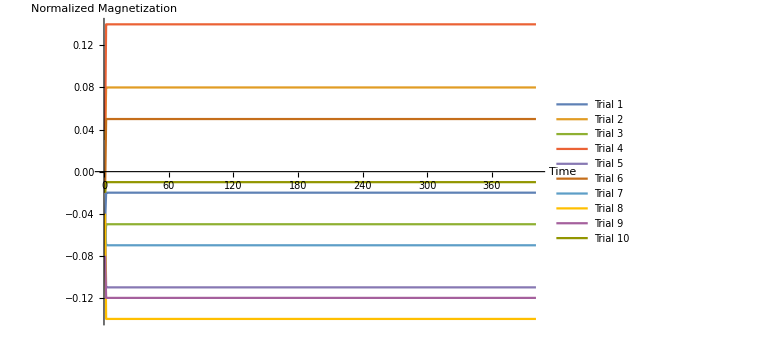

0.079

```mathematica
magnetism1={-10,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4}/200;
magnetism2={6,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}/200;
magnetism3={-14,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10}/200;
magnetism4={8,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28}/200;
magnetism5={-8,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22,-22}/200;
magnetism6={-4,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}/200;
magnetism7={-10,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14}/200;
magnetism8={-8,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28,-28}/200;
magnetism9={-16,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24,-24}/200;
magnetism10={-4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT005=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

The domains here look to be much smaller.

### Large Lattice: 200 long, kT=0.5, 400 time steps

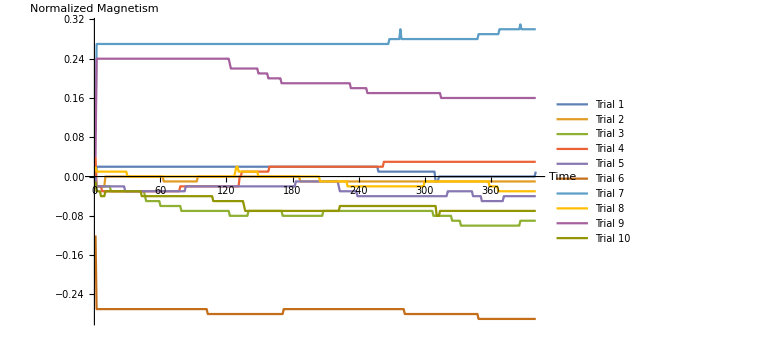

0.0968212

```mathematica
magnetism1={-2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2}/200;
magnetism2={-4,-4,-4,-4,-4,-4,-4,-4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}/200;
magnetism3={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-8,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-16,-18,-18,-18,-18,-18,-18,-18,-18,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18,-18}/200;
magnetism4={8,-4,-4,-4,-4,-4,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}/200;
magnetism5={0,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-4,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-8,-8,-8,-8,-8,-8,-8,-8,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8}/200;
magnetism6={-24,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-54,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-56,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58,-58}/200;
magnetism7={18,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,56,56,56,56,56,56,56,56,56,56,60,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,62,60,60,60,60,60,60,60,60,60,60,60,60,60,60}/200;
magnetism8={4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-4,-4,-4,-4,-4,-4,-4,-4,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6}/200;
magnetism9={8,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,46,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,42,42,42,42,42,42,42,42,42,40,40,40,40,40,40,40,40,40,40,40,40,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32}/200;
magnetism10={-2,-6,-6,-6,-6,-8,-8,-8,-8,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-10,-12,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-16,-16,-16,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14,-14}/200;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization1Dn200kT05=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### All data for 1D

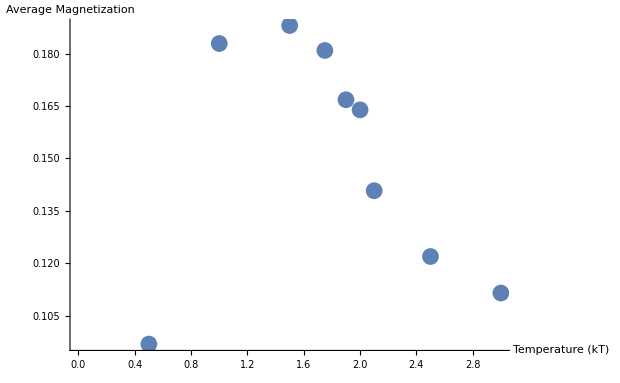

```mathematica
ListPlot[{{1,averageMagnetization1Dn200kT1},{1.5,averageMagnetization1Dn200kT15},{1.75,averageMagnetization1Dn200kT175},{1.9,averageMagnetization1Dn200kT19},{2,averageMagnetization1Dn200kT2},{2.1,averageMagnetization1Dn200kT21},{2.5,averageMagnetization1Dn200kT25},{3,averageMagnetization1Dn200kT3},{0.5,averageMagnetization1Dn200kT05}},AxesLabel->{"Temperature (kT)","Average Magnetization"}]
```

## 2 D Ising Model

These runs come from the file regular2D.py file

### 200x200, kT=0.5, 200 time steps

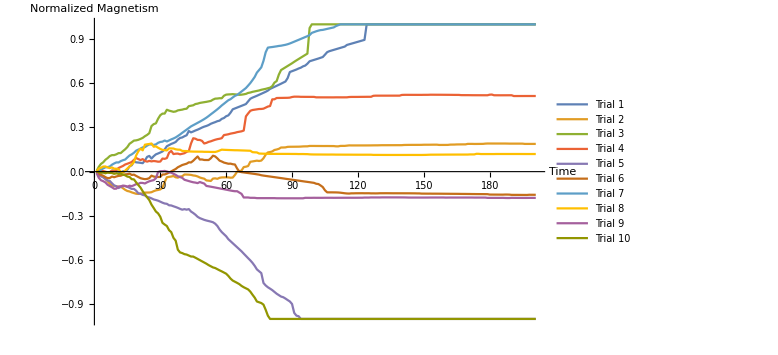

0.609446

```mathematica
magnetism1={132,-64,-190,-222,-144,-132,-252,280,290,110,8,-306,86,156,526,1438,1740,2756,2532,2474,2392,2298,3026,4004,4262,3558,4190,4690,4930,5192,5472,6028,6904,7214,7530,7760,8046,8694,9142,9286,9614,9886,11028,10664,10904,11174,11400,11674,11972,12214,12402,12646,12992,13232,13442,13700,13844,14332,14566,15046,15280,16018,16926,17162,17398,17634,17870,18108,18356,19070,19792,20100,20346,20598,20870,21142,21414,21686,22012,22470,22748,23028,23306,23588,23876,24174,24472,25398,27048,27276,27504,27732,28010,28232,28586,28800,29312,29970,30156,30342,30528,30714,30918,31122,31766,32446,32712,32890,33068,33246,33424,33602,33780,33958,34404,34576,34748,34918,35092,35264,35436,35608,35780,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,39998,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000}/(200*200);
magnetism2={-64,-514,-968,-1388,-1952,-2604,-3270,-3766,-3882,-3946,-4146,-4078,-4498,-4936,-5252,-5386,-5632,-5824,-6006,-6046,-5966,-5928,-5692,-5678,-5670,-5586,-5304,-5092,-4968,-4828,-4388,-2816,-1526,-1414,-1328,-1186,-1532,-1632,-1350,-1248,-778,-790,-822,-884,-1038,-1114,-1304,-1590,-1772,-1912,-2388,-2452,-2526,-1888,-1826,-1950,-1674,-1574,-1562,-1530,-1572,-1650,-1608,-894,-18,84,302,1234,1342,1522,2668,2772,2876,2980,2886,3002,3634,4604,5214,5314,5492,5880,6010,6194,6552,6558,6586,6730,6752,6758,6764,6772,6778,6802,6850,6866,6874,6974,6974,6974,6966,6964,6960,6956,6954,6958,6950,6946,6942,6874,6864,6980,6994,6992,7058,7124,7114,7114,7114,7114,7116,7116,7116,7118,7120,7126,7138,7142,7144,7162,7176,7176,7176,7178,7180,7182,7184,7186,7184,7190,7240,7250,7260,7264,7266,7266,7268,7270,7276,7302,7304,7306,7310,7318,7320,7322,7250,7252,7254,7256,7262,7334,7344,7350,7386,7392,7398,7402,7402,7536,7536,7536,7518,7520,7526,7532,7540,7606,7638,7636,7634,7632,7632,7632,7632,7632,7632,7622,7606,7606,7606,7606,7606,7606,7600,7528,7528,7528,7528,7528,7530}/40000;
magnetism3={188,1308,2104,2526,3216,3664,4224,4486,4490,4706,5030,5044,5572,6064,6676,7564,7980,8424,8492,8644,8888,9168,9616,9972,10450,12370,12900,13108,14368,15320,15754,15768,16808,16566,16410,16248,16342,16634,16740,16838,17008,17088,17782,17898,18020,18356,18466,18656,18760,18858,18954,19076,19196,19558,19820,19854,19934,19924,20608,20908,20966,20996,21040,20982,20932,20854,20904,20990,21112,21370,21484,21668,21792,21918,22044,22228,22356,22480,22652,22800,23220,24172,24594,26358,27586,27954,28322,28690,29058,29426,29830,30212,30580,30952,31318,31686,32054,38994,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000}/40000;
magnetism4={-68,-74,142,138,-14,-184,-120,254,32,452,988,1272,1546,1936,2146,2364,2616,3206,3704,3410,3142,3402,2892,2718,2912,2784,2890,2816,2698,2730,3544,3474,3684,5146,5616,4770,4872,4896,4708,4848,5004,5360,5618,7644,9068,8938,8622,8596,8354,7642,7810,8076,8234,8456,8660,8820,8928,9090,9934,10030,10148,10320,10434,10550,10726,10836,10946,11156,14998,15794,16518,16734,16826,16920,17008,17022,17100,17382,17674,17816,19628,19648,19994,20010,20020,20030,20040,20050,20096,20266,20356,20356,20350,20314,20312,20304,20302,20300,20300,20296,20176,20174,20172,20170,20170,20168,20168,20166,20166,20180,20178,20176,20174,20176,20180,20262,20286,20288,20288,20292,20302,20308,20312,20320,20322,20322,20590,20630,20630,20630,20632,20632,20632,20632,20634,20634,20636,20634,20636,20826,20852,20856,20854,20852,20850,20850,20846,20846,20844,20858,20858,20862,20888,20886,20882,20878,20876,20874,20868,20864,20860,20854,20848,20840,20838,20834,20774,20772,20770,20770,20762,20754,20750,20748,20746,20744,20742,20740,20738,20896,20932,20742,20736,20736,20732,20734,20736,20738,20740,20742,20526,20528,20530,20532,20534,20536,20538,20538,20538,20538,20538}/40000;
magnetism5={-6,-1026,-1292,-1540,-2024,-2406,-2524,-3156,-3748,-3968,-4458,-4148,-3936,-3912,-4118,-4398,-4690,-4686,-5176,-5886,-6002,-6314,-6444,-6884,-7012,-7260,-7548,-7708,-7890,-8156,-8434,-8654,-8742,-9136,-9186,-9410,-9610,-9840,-10108,-10332,-10186,-10330,-10178,-10838,-11232,-11698,-12266,-12624,-12856,-13090,-13268,-13416,-13564,-13744,-14134,-14764,-15694,-16418,-16984,-17552,-18346,-18892,-19444,-19990,-20538,-21086,-21634,-22266,-22882,-23500,-24102,-24778,-25590,-26542,-27052,-27552,-30236,-30910,-31400,-31776,-32176,-32666,-33152,-33538,-33924,-34106,-34464,-34870,-35252,-35942,-38364,-39110,-39262,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-39998,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-39998,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-39998,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000}/40000;
magnetism6={-96,-658,-876,-1116,-1494,-1764,-1728,-1342,-1518,-1312,-1154,-1100,-856,-742,-688,-532,-902,-818,-1158,-1470,-1778,-1934,-2042,-1976,-1770,-1086,-1340,-1424,-1454,-1428,-786,-760,-546,-248,68,398,714,1190,1486,1798,1980,2160,2526,2494,2954,3550,4120,3288,3308,3166,3156,3152,3622,4326,4128,3602,2988,2750,2458,2302,2146,2168,2010,1930,842,20,-136,-218,-300,-382,-464,-546,-628,-722,-818,-980,-1078,-1164,-1248,-1332,-1416,-1500,-1584,-1670,-1756,-1842,-1936,-2022,-2108,-2192,-2276,-2362,-2448,-2532,-2618,-2706,-2786,-2870,-2962,-3048,-3288,-3372,-3752,-4188,-5070,-5622,-5628,-5626,-5636,-5642,-5666,-5716,-5794,-5870,-5930,-5954,-5894,-5892,-5874,-5870,-5866,-5862,-5876,-5872,-5870,-5902,-5898,-5910,-5900,-5870,-5868,-5866,-5864,-5868,-5872,-5880,-5878,-5880,-5880,-5880,-5884,-5884,-5886,-5888,-5896,-5900,-5916,-5918,-5968,-5970,-5976,-5980,-5976,-5988,-5986,-5988,-5992,-5996,-6004,-6008,-6012,-6020,-6024,-6028,-6030,-6038,-6050,-6054,-6058,-6066,-6072,-6084,-6088,-6096,-6100,-6104,-6108,-6114,-6118,-6228,-6232,-6236,-6238,-6242,-6248,-6250,-6226,-6228,-6244,-6308,-6310,-6312,-6314,-6320,-6324,-6328,-6332,-6280,-6284,-6288,-6292}/40000;
magnetism7={164,326,500,872,1174,1228,1384,1884,2222,2504,2488,2856,3100,3280,3850,4386,4696,5122,5692,5976,6232,6586,6656,7064,7386,7376,7244,7398,7820,8058,8140,8450,8194,8472,8760,9004,9292,9682,10092,10550,10976,11406,11842,12286,12610,12924,13250,13572,13910,14266,14654,15088,15558,16006,16466,16932,17436,17976,18442,18922,19392,19682,20148,20578,20826,21294,21758,22224,22700,23360,24048,24858,25716,26892,27598,28326,30078,32424,33672,33770,33840,33934,34024,34134,34200,34322,34438,34598,34802,35044,35292,35542,35788,36040,36290,36540,36792,37078,37680,37892,38112,38290,38436,38492,38626,38766,38900,39034,39166,39526,39764,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000,40000}/40000;
magnetism8={68,812,1052,1382,1410,1148,962,1142,812,798,624,-20,-214,246,846,1392,1920,2582,4382,5514,6264,5786,7312,7424,7510,7644,6768,6872,6492,6168,5910,5834,5762,6318,6298,6276,6062,5976,5952,5628,5592,5590,5486,5466,5440,5432,5428,5420,5418,5384,5380,5374,5352,5348,5344,5498,5732,5970,5926,5902,5876,5854,5832,5808,5804,5782,5760,5740,5718,5694,5670,5290,5242,5216,4914,4894,4868,4870,4840,4820,4820,4820,4818,4818,4818,4816,4816,4816,4810,4800,4798,4796,4770,4778,4778,4760,4752,4694,4672,4660,4656,4652,4648,4644,4640,4636,4636,4642,4636,4622,4620,4618,4614,4610,4610,4608,4606,4600,4598,4596,4594,4594,4594,4596,4594,4592,4546,4544,4542,4540,4536,4534,4532,4532,4530,4530,4530,4530,4530,4530,4530,4530,4534,4534,4534,4532,4530,4530,4530,4540,4552,4580,4604,4606,4608,4612,4614,4616,4618,4626,4626,4628,4630,4632,4634,4636,4634,4636,4638,4640,4676,4676,4678,4842,4836,4776,4776,4776,4776,4776,4774,4774,4790,4790,4790,4790,4790,4790,4790,4790,4790,4792,4792,4788,4786,4784,4782,4782,4782,4784,4784}/40000;
magnetism9={-396,-1672,-2346,-2590,-2928,-3566,-3910,-4246,-4648,-4620,-4058,-3998,-3788,-3876,-4102,-3820,-3944,-3696,-3400,-3312,-3048,-3070,-3212,-2886,-2626,-2448,-2306,-1792,-106,108,122,194,38,-154,-302,-586,-874,-1258,-1470,-1684,-2210,-2384,-2564,-2738,-2888,-2978,-3122,-2824,-3036,-3236,-3884,-3984,-4092,-4204,-4318,-4434,-4550,-4666,-4778,-4896,-5014,-5134,-5244,-5322,-5318,-5678,-6038,-7018,-7018,-7020,-7108,-7110,-7118,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7232,-7234,-7236,-7238,-7240,-7240,-7240,-7240,-7242,-7242,-7242,-7242,-7242,-7114,-7114,-7116,-7116,-7102,-7110,-7108,-7114,-7112,-7100,-7100,-7100,-7100,-7110,-7106,-7102,-7100,-7098,-7094,-7094,-7092,-7094,-7094,-7094,-7090,-7084,-7082,-7042,-7042,-7044,-7006,-7010,-7010,-7010,-7012,-6990,-6990,-6990,-6990,-6992,-6992,-6992,-6994,-6996,-6998,-7002,-7016,-7036,-7042,-7042,-7040,-7040,-7042,-7042,-7042,-7038,-7036,-7028,-7028,-7026,-7024,-7024,-7020,-7022,-7050,-7040,-7034,-7036,-7036,-7036,-7034,-7034,-7034,-7032,-7032,-7032,-7032,-7046,-7046,-7044,-7044,-7046,-7046,-7124,-7126,-7126,-7126,-7126,-7128,-7128,-7118,-7148,-7164,-7164,-7116,-7124,-7128,-7132,-7134,-7136,-7136,-7136,-7128,-7128,-7130,-7132}/40000;
magnetism10={-38,-50,-296,-204,-464,-222,-326,-372,-594,-448,-610,-562,-820,-982,-1344,-1452,-2046,-2106,-2896,-3640,-4340,-5318,-6174,-6964,-7732,-8964,-9878,-10830,-11338,-12254,-13900,-14362,-14770,-15890,-16432,-17976,-18744,-21190,-21934,-22116,-22408,-22522,-22786,-23050,-23066,-23376,-23700,-24026,-24352,-24676,-25000,-25382,-25696,-26010,-26176,-26490,-26804,-27090,-27404,-27718,-28318,-29050,-29584,-29898,-30212,-30552,-31028,-31388,-31686,-31984,-32584,-33426,-34220,-35266,-35476,-35686,-36120,-37522,-39116,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT05=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
(*data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]]; *)
```

```mathematica
(*Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}] *) (*Commented out to prevent crashing!!*)
```

### 200x200, kT=1, 200 time steps

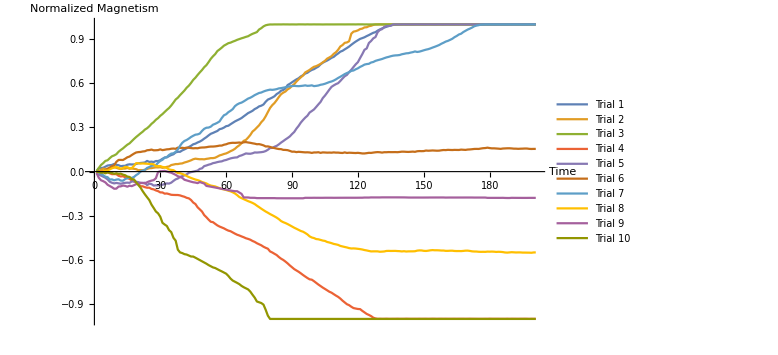

0.746167

```mathematica
magnetism1={32,870,960,1046,1346,1650,1738,1814,2094,1848,1744,1478,1556,1578,1872,1982,1938,1962,2072,2262,2346,2406,2486,2900,2632,2708,2606,2868,2872,3090,3488,3824,3866,4222,4502,4708,5206,5388,5374,5758,6030,6328,6676,7006,7422,7596,7914,8160,8504,8954,9354,9836,10268,10506,10780,11038,11520,11674,11954,12334,12458,12868,13246,13626,13930,14220,14548,15004,15442,15892,16182,16510,16984,17286,17710,17902,18228,18974,19558,19820,20114,20460,21054,21414,21964,22158,22604,23512,23846,24254,24656,25040,25346,25846,26170,26628,26838,27276,27612,27826,28192,28524,29128,29572,29880,30162,30512,30904,31160,31676,32094,32568,32806,33196,33560,33960,34440,34890,35310,35680,36040,36252,36480,36800,37076,37398,37692,37870,38286,38604,38878,39114,39328,39534,39732,39826,39872,39932,39978,39976,39986,39962,39976,39958,39960,39972,39974,39982,39976,39966,39974,39982,39980,39968,39970,39966,39978,39968,39980,39962,39976,39968,39978,39960,39980,39970,39968,39972,39962,39974,39962,39958,39976,39962,39982,39972,39974,39988,39976,39958,39956,39954,39968,39984,39974,39958,39968,39960,39982,39984,39982,39958,39972,39982,39970,39964,39968,39976,39966,39982,39974}/(200*200);
magnetism2={2,94,520,798,706,768,950,1010,1198,1044,822,698,820,834,1010,778,838,762,666,376,428,390,508,722,916,946,1066,1160,1134,1186,1038,1124,1294,1408,1784,1912,2048,2054,2172,2230,2474,2636,2842,3070,3358,3514,3426,3360,3374,3332,3462,3546,3666,3664,3778,4074,4396,4572,4788,4944,5220,5554,5824,6198,6732,7154,7712,8358,8614,9240,9950,10870,11362,11976,12580,13420,14050,15028,16176,17288,18046,18622,19400,20260,21012,21446,21752,22336,22698,23280,23750,24452,25052,25602,26102,26936,27264,27618,28082,28466,28636,28928,29248,29676,30086,30684,31000,31360,31982,32418,33096,33982,34368,34968,35076,35404,37460,38010,38136,38352,38704,38830,39162,39202,39490,39602,39830,39946,39962,39972,39972,39962,39972,39978,39972,39980,39984,39984,39956,39972,39970,39972,39972,39960,39970,39974,39978,39980,39966,39976,39980,39984,39978,39980,39972,39960,39968,39974,39962,39986,39972,39978,39976,39964,39960,39966,39990,39972,39968,39950,39960,39978,39976,39956,39964,39978,39976,39976,39980,39964,39974,39972,39974,39972,39978,39972,39970,39970,39968,39968,39984,39974,39958,39970,39982,39962,39964,39974,39968,39966,39982}/40000;
magnetism3={202,998,1798,2300,2906,3086,3652,4162,4400,4734,5396,5876,6298,6816,7310,7668,8258,8846,9392,9878,10382,10840,11410,11782,12314,12964,13460,14088,14530,15152,15624,16202,16770,17278,17960,18748,19576,20072,20764,21384,22012,22770,23338,24072,24906,25500,26246,26938,27584,28350,28908,29732,30622,31312,31900,32736,33180,33662,34200,34524,34872,35022,35292,35510,35780,35988,36198,36380,36590,36764,37114,37412,37644,37892,38590,38950,39428,39734,39876,39956,39948,39968,39964,39970,39962,39984,39972,39974,39958,39968,39962,39954,39984,39978,39978,39960,39986,39966,39966,39980,39968,39972,39966,39952,39966,39970,39966,39968,39966,39968,39974,39974,39972,39968,39974,39978,39974,39976,39966,39988,39982,39984,39964,39970,39960,39966,39974,39968,39966,39976,39966,39972,39968,39974,39968,39974,39968,39958,39962,39976,39972,39974,39984,39970,39978,39978,39974,39978,39968,39970,39970,39972,39964,39968,39972,39976,39978,39982,39966,39980,39980,39952,39972,39970,39968,39972,39974,39984,39962,39964,39970,39974,39968,39984,39968,39962,39960,39966,39962,39974,39978,39970,39970,39968,39966,39958,39946,39974,39964,39986,39980,39984,39980,39958,39978,39964,39974,39974,39976,39968,39972}/40000;
magnetism4={-328,-268,138,118,-32,-158,-450,-694,-672,-690,-1126,-1310,-1246,-1526,-1768,-1970,-2398,-2694,-2912,-3308,-3990,-3988,-4224,-4374,-4372,-4706,-4824,-5108,-5302,-5642,-5660,-5982,-5940,-6106,-6292,-6332,-6348,-6354,-6458,-6660,-6830,-7110,-7260,-7700,-8398,-8802,-9690,-10252,-10842,-11802,-12386,-13036,-13616,-13728,-14172,-14604,-14918,-15162,-15408,-15742,-16020,-16188,-16516,-16842,-17134,-17340,-17594,-17820,-18094,-18270,-18490,-18828,-19084,-19446,-19728,-20006,-20392,-20692,-20936,-21674,-21954,-22312,-22654,-23190,-23638,-23984,-24428,-24920,-25476,-25968,-26470,-26836,-27196,-27616,-28068,-28484,-28888,-29244,-29346,-29752,-30208,-30666,-31076,-31490,-31856,-32232,-32614,-32878,-33278,-33664,-34012,-34476,-35038,-35520,-36002,-36266,-36694,-37050,-37178,-37298,-37336,-37810,-38218,-38642,-38912,-39230,-39660,-39874,-39978,-39960,-39982,-39974,-39956,-39982,-39982,-39974,-39974,-39962,-39978,-39978,-39976,-39952,-39970,-39976,-39976,-39972,-39976,-39966,-39972,-39968,-39964,-39978,-39968,-39954,-39962,-39978,-39964,-39962,-39970,-39964,-39972,-39970,-39968,-39964,-39972,-39966,-39964,-39964,-39972,-39970,-39956,-39970,-39972,-39978,-39986,-39980,-39980,-39972,-39980,-39954,-39968,-39968,-39970,-39968,-39976,-39974,-39978,-39960,-39980,-39962,-39968,-39970,-39978,-39966,-39968,-39960,-39968,-39990,-39970,-39976,-39968}/40000;
magnetism5={-476,-788,-1078,-1364,-1660,-2114,-2748,-3030,-3198,-3074,-3184,-3294,-3148,-3042,-2996,-3042,-2668,-2648,-2752,-2860,-3088,-3098,-3022,-3676,-3262,-3390,-3794,-3716,-3762,-3522,-3574,-3348,-3202,-3244,-2992,-2520,-2098,-1874,-1438,-1224,-1014,-744,-314,-136,-2,138,272,738,898,1494,1664,1882,2036,2302,2414,2588,2712,2788,3032,3166,3388,3590,3724,3822,3866,4240,4412,4666,4936,4870,4848,4978,5204,5174,5228,5282,5378,5584,5940,6414,6436,6750,6992,7400,7882,8288,8726,9122,9562,10202,10764,11670,12418,13314,14014,14650,15176,16040,16448,16882,17558,18260,18932,19962,20646,21446,22274,23026,23416,23760,24018,24616,25284,25894,26258,27020,27660,28412,29136,29724,30840,31904,33080,33448,34926,35470,36184,36536,37874,38462,38686,39286,39536,39538,39612,39964,39970,39966,39952,39962,39978,39968,39966,39966,39974,39978,39974,39966,39984,39974,39970,39974,39978,39972,39956,39976,39982,39958,39964,39968,39974,39966,39964,39964,39966,39960,39970,39964,39956,39980,39976,39968,39970,39974,39980,39962,39974,39986,39974,39978,39976,39978,39970,39972,39956,39982,39960,39964,39968,39964,39982,39980,39986,39972,39966,39968,39974,39970,39984,39978,39976}/40000;
magnetism6={-156,-376,-506,-96,362,742,1098,1476,1694,2656,3168,3182,3154,3496,3888,4090,4500,4874,5194,5300,5340,5470,5532,5800,5854,5982,5784,5798,5840,6042,5834,5932,6048,6086,6218,6264,6194,6516,6434,6464,6382,6510,6478,6390,6322,6368,6338,6490,6546,6562,6630,6746,6802,6804,6852,6940,7060,7070,7300,7424,7656,7768,7828,7806,7846,7904,7792,7966,8016,7906,7820,7690,7584,7434,7464,7320,7132,6830,6848,6700,6506,6394,6246,6132,6102,5906,5886,5824,5630,5408,5426,5296,5378,5332,5276,5226,5244,5200,5080,5204,5200,5264,5092,5218,5192,5148,5170,5140,5218,5158,5162,5096,5064,5216,5072,5132,5108,5070,5046,5098,5024,4934,4932,5010,5104,5078,5170,5250,5298,5258,5164,5268,5264,5306,5288,5290,5302,5274,5338,5416,5412,5370,5348,5388,5432,5374,5528,5576,5554,5578,5720,5670,5700,5742,5710,5676,5696,5792,5864,5840,5914,5882,5862,5900,5886,5878,5974,5932,5896,5990,6022,6082,6156,6168,6158,6268,6358,6396,6502,6392,6316,6320,6280,6234,6174,6270,6300,6330,6336,6296,6234,6230,6186,6220,6238,6272,6268,6180,6150,6168,6166}/40000;
magnetism7={-456,-450,-634,-966,-1390,-1518,-2148,-2110,-2350,-2168,-2086,-2432,-2472,-2030,-1772,-1666,-1708,-1462,-956,-582,14,294,454,1008,1238,1580,1664,1750,2408,2892,3206,3778,3964,4524,4896,4974,5380,6012,7000,7812,8318,8588,8966,9402,9734,10028,10112,10336,11046,11620,11914,11962,12212,12736,12974,13268,13642,14554,15302,15576,16140,16518,16974,17772,18230,18546,18734,19068,19446,19832,20064,20396,20774,21062,21352,21478,21748,21964,22128,22258,22200,22278,22396,22598,22672,22786,22914,23046,23154,23226,23288,23232,23202,23256,23322,23420,23294,23330,23428,23216,23284,23382,23582,23684,23856,24082,24318,24476,24726,25054,25434,25758,26110,26482,26766,27002,27352,27458,27786,28052,28434,28714,29058,29196,29274,29626,29768,30072,30252,30412,30578,30806,31010,31156,31338,31478,31554,31586,31662,31864,31982,32116,32158,32318,32438,32632,32488,32582,32752,32942,33114,33248,33446,33682,33896,34130,34376,34718,34996,35308,35504,35782,36074,36508,36832,37236,37444,37896,38236,38570,38824,39116,39466,39650,39766,39922,39936,39964,39962,39974,39954,39966,39970,39972,39948,39980,39952,39974,39968,39960,39960,39974,39966,39950,39948,39952,39974,39970,39970,39968,39982}/40000;
magnetism8={-186,-120,22,38,294,320,608,910,1106,1270,1054,790,978,1286,1214,928,932,1562,2288,2270,2172,2218,2174,2138,2068,2080,1992,1506,1488,1502,1272,1190,972,580,472,388,-14,-402,-432,-620,-870,-1186,-1478,-1714,-1940,-2152,-2304,-2520,-2816,-3004,-3206,-3546,-3790,-3900,-4022,-4258,-4490,-4718,-4834,-4994,-5182,-5352,-5614,-5934,-6378,-6900,-7198,-7480,-7742,-8018,-8238,-8500,-8814,-9250,-9650,-10068,-10458,-10838,-11166,-11526,-11830,-12154,-12498,-12908,-13422,-13730,-13962,-14246,-14568,-14900,-15234,-15520,-15820,-16120,-16314,-16656,-17046,-17578,-17890,-18044,-18310,-18380,-18548,-18724,-18824,-19106,-19250,-19424,-19634,-19752,-19896,-20176,-20320,-20464,-20596,-20770,-20870,-20848,-20888,-20964,-21040,-21146,-21298,-21404,-21540,-21666,-21648,-21646,-21654,-21758,-21724,-21676,-21542,-21524,-21544,-21536,-21530,-21570,-21602,-21670,-21608,-21694,-21654,-21650,-21644,-21618,-21454,-21392,-21408,-21510,-21542,-21468,-21368,-21310,-21358,-21356,-21384,-21430,-21432,-21516,-21514,-21478,-21474,-21548,-21572,-21566,-21584,-21530,-21464,-21454,-21538,-21650,-21692,-21702,-21762,-21786,-21772,-21786,-21722,-21738,-21714,-21744,-21804,-21768,-21792,-21850,-21956,-21994,-21940,-21880,-21914,-21954,-21938,-21940,-21986,-21988,-21998,-22004,-22034,-21952,-21932}/40000;
magnetism9={-396,-1672,-2346,-2590,-2928,-3566,-3910,-4246,-4648,-4620,-4058,-3998,-3788,-3876,-4102,-3820,-3944,-3696,-3400,-3312,-3048,-3070,-3212,-2886,-2626,-2448,-2306,-1792,-106,108,122,194,38,-154,-302,-586,-874,-1258,-1470,-1684,-2210,-2384,-2564,-2738,-2888,-2978,-3122,-2824,-3036,-3236,-3884,-3984,-4092,-4204,-4318,-4434,-4550,-4666,-4778,-4896,-5014,-5134,-5244,-5322,-5318,-5678,-6038,-7018,-7018,-7020,-7108,-7110,-7118,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7196,-7232,-7234,-7236,-7238,-7240,-7240,-7240,-7240,-7242,-7242,-7242,-7242,-7242,-7114,-7114,-7116,-7116,-7102,-7110,-7108,-7114,-7112,-7100,-7100,-7100,-7100,-7110,-7106,-7102,-7100,-7098,-7094,-7094,-7092,-7094,-7094,-7094,-7090,-7084,-7082,-7042,-7042,-7044,-7006,-7010,-7010,-7010,-7012,-6990,-6990,-6990,-6990,-6992,-6992,-6992,-6994,-6996,-6998,-7002,-7016,-7036,-7042,-7042,-7040,-7040,-7042,-7042,-7042,-7038,-7036,-7028,-7028,-7026,-7024,-7024,-7020,-7022,-7050,-7040,-7034,-7036,-7036,-7036,-7034,-7034,-7034,-7032,-7032,-7032,-7032,-7046,-7046,-7044,-7044,-7046,-7046,-7124,-7126,-7126,-7126,-7126,-7128,-7128,-7118,-7148,-7164,-7164,-7116,-7124,-7128,-7132,-7134,-7136,-7136,-7136,-7128,-7128,-7130,-7132}/40000;
magnetism10={-38,-50,-296,-204,-464,-222,-326,-372,-594,-448,-610,-562,-820,-982,-1344,-1452,-2046,-2106,-2896,-3640,-4340,-5318,-6174,-6964,-7732,-8964,-9878,-10830,-11338,-12254,-13900,-14362,-14770,-15890,-16432,-17976,-18744,-21190,-21934,-22116,-22408,-22522,-22786,-23050,-23066,-23376,-23700,-24026,-24352,-24676,-25000,-25382,-25696,-26010,-26176,-26490,-26804,-27090,-27404,-27718,-28318,-29050,-29584,-29898,-30212,-30552,-31028,-31388,-31686,-31984,-32584,-33426,-34220,-35266,-35476,-35686,-36120,-37522,-39116,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000,-40000}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT1=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### 200x200, kT=1.5 , 200 time steps

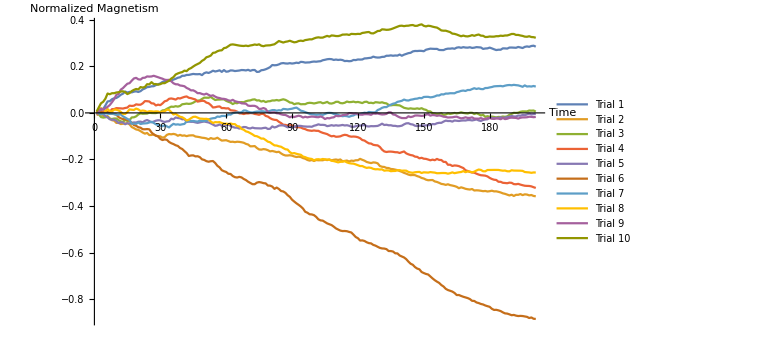

0.21434

```mathematica
magnetism1={-38,-32,502,658,1278,1966,2024,2346,2512,2568,2796,3110,3304,3672,3492,3614,3526,3652,3706,3596,3738,4038,4200,4424,4466,4566,4588,4782,4922,5062,5314,5446,5482,5544,5562,5726,5858,6040,6120,6378,6382,6522,6528,6618,6696,6650,6644,6674,6494,6826,6964,6862,7026,7252,7118,7198,7314,7046,7362,7080,7126,7300,7284,7192,7236,7280,7368,7352,7300,7404,7234,7364,7374,7040,7072,7332,7380,7498,7664,7864,8226,8182,8212,8332,8512,8562,8498,8476,8548,8480,8532,8628,8566,8770,8736,8644,8668,8680,8774,8822,8794,8848,8882,9052,9128,9220,9260,9232,9102,9166,9098,9140,9078,8906,8934,8878,8916,9096,9074,9178,9162,9184,9358,9380,9434,9476,9668,9552,9510,9524,9624,9642,9822,9822,9884,9820,9868,9846,10028,9822,10006,10134,10266,10328,10564,10642,10632,10666,10656,10598,10852,10948,11038,11012,10996,11000,10814,10798,10794,10960,11040,11038,11090,11022,11214,11276,11188,11296,11228,11212,11280,11166,11210,11302,11270,11240,10996,11064,11088,11218,11084,10934,10798,10856,10854,11088,11082,11050,11226,11232,11210,11190,11330,11244,11148,11344,11422,11354,11496,11548,11382}/(200*200);
magnetism2={142,-74,-202,-496,-682,-554,-942,-1260,-1328,-1724,-1688,-1918,-1866,-1828,-1744,-1978,-2428,-2622,-2842,-2920,-3132,-3376,-3566,-3446,-3808,-3790,-3678,-3932,-3992,-4028,-4252,-4158,-3774,-3638,-3678,-3610,-3700,-3926,-3774,-3920,-3870,-3994,-3888,-3862,-3856,-4054,-4108,-4174,-4266,-4300,-4384,-4544,-4324,-4452,-4430,-4266,-4520,-4758,-4724,-4694,-4836,-4982,-4952,-5024,-4954,-4982,-5042,-5130,-5322,-5434,-5744,-5734,-5700,-6034,-6278,-6312,-6222,-6274,-6412,-6608,-6542,-6636,-6742,-6676,-6960,-7184,-7316,-7320,-7282,-7344,-7482,-7578,-7524,-7582,-7768,-7874,-8086,-8198,-8098,-8266,-8106,-8142,-8134,-8140,-8014,-8114,-7990,-8160,-8060,-8010,-8092,-8004,-8308,-8252,-8188,-8356,-8202,-8254,-8140,-8132,-7898,-8064,-8210,-8430,-8536,-8624,-8506,-8542,-8670,-9126,-9256,-9290,-9452,-9478,-9636,-9668,-9750,-9836,-9988,-10122,-10302,-10436,-10602,-10700,-10668,-10698,-10864,-10982,-11180,-11276,-11470,-11572,-11548,-11536,-11774,-11866,-12020,-12202,-12258,-12370,-12264,-12408,-12486,-12576,-12704,-12942,-12792,-12904,-13042,-13120,-13168,-13080,-13332,-13302,-13324,-13382,-13452,-13416,-13504,-13456,-13372,-13484,-13478,-13564,-13670,-13826,-13912,-14048,-14184,-14058,-14276,-14074,-14078,-13944,-14126,-13996,-14032,-14168,-14112,-14272,-14326}/40000;
magnetism3={-284,-246,-716,-804,-754,-684,-1030,-1046,-966,-966,-1248,-1462,-1526,-1226,-1380,-1240,-778,-756,-592,-270,-80,-148,-130,-116,38,-18,-30,-34,106,140,426,466,698,890,1078,1042,1152,1080,1194,1486,1534,1596,1546,1596,1750,1978,2108,2146,2398,2620,2610,2604,2754,2458,2214,2280,2292,2324,2324,2074,1908,1776,1520,1716,1658,1840,1856,1824,2004,2108,2150,2288,2326,2132,2158,1954,2062,1860,1988,2010,2140,2132,2216,2124,2236,2338,2234,2034,1786,1738,1492,1610,1638,1482,1502,1498,1678,1734,1702,1622,1698,1800,1836,1656,1744,1890,1642,1608,1706,1904,1908,1692,1650,1744,1950,1848,1870,1936,1824,1884,1794,1688,1884,1924,1708,1746,1664,1838,1804,1748,1822,1694,1634,1378,1292,1354,1354,1328,1290,1090,876,788,716,780,716,702,778,688,810,616,524,272,254,-66,-120,-198,-174,-64,-360,-272,-100,-176,-104,-6,-92,-20,94,-8,-64,-108,22,22,-198,-48,-220,-438,-326,-676,-566,-660,-640,-698,-782,-692,-716,-624,-678,-594,-328,-176,16,-10,30,194,262,258,254,406,384,406,224}/40000;
magnetism4={-312,-124,156,248,100,90,166,642,660,820,796,774,746,844,914,1248,1198,1240,1468,1410,1408,1638,2022,2010,1958,1644,1614,1282,1416,1328,1626,1992,2102,2422,2480,2402,2286,2534,2476,2624,2752,2828,2600,2532,2414,2306,1942,2010,2082,2050,1770,1660,1344,932,972,1072,1116,826,832,766,792,454,414,368,220,-80,-94,-196,-88,-94,-28,-56,-178,-238,-326,-168,-178,-520,-630,-902,-1092,-1186,-1222,-1524,-1746,-2038,-2062,-2168,-2098,-2144,-2328,-2472,-2458,-2514,-2690,-2788,-2962,-3032,-3082,-3018,-3076,-3084,-3282,-3428,-3532,-3644,-3860,-4020,-3956,-4102,-4082,-4028,-3864,-3766,-3822,-4006,-4086,-4060,-4092,-4180,-4354,-4660,-4754,-5014,-5234,-5272,-5486,-5550,-5584,-5854,-6316,-6618,-6716,-6656,-6652,-6690,-6756,-6764,-6888,-6752,-6628,-6954,-7120,-7244,-7312,-7516,-7558,-7804,-7716,-7870,-7902,-8016,-8142,-8032,-8128,-7912,-8078,-8096,-8418,-8424,-8910,-8908,-9120,-9030,-9062,-9144,-9318,-9474,-9852,-9982,-10142,-10240,-10274,-10446,-10598,-10710,-10742,-10784,-10914,-11168,-11356,-11482,-11526,-11832,-11840,-12012,-12046,-12086,-11984,-12020,-12236,-12264,-12196,-12322,-12426,-12518,-12544,-12556,-12626,-12768,-12898}/40000;
magnetism5={142,176,158,-192,-556,-754,-1088,-1178,-1164,-1364,-1742,-1602,-1650,-1948,-1770,-1840,-1710,-1640,-1658,-1520,-1504,-1612,-1364,-1224,-1404,-1618,-1496,-1340,-1258,-1270,-1458,-1558,-1460,-1420,-996,-1096,-788,-878,-918,-1106,-1062,-1558,-1490,-1534,-1530,-1628,-1710,-1628,-1546,-1482,-1564,-1638,-1808,-2004,-2216,-2156,-1986,-2200,-2166,-2084,-2016,-2222,-2422,-2530,-2538,-2698,-2542,-2422,-2444,-2618,-2674,-2524,-2628,-2646,-2658,-2672,-2594,-2548,-2758,-2726,-2322,-2506,-2388,-2182,-2138,-2148,-2288,-2484,-2380,-2550,-2426,-2222,-2226,-2236,-2310,-2340,-2362,-2354,-2384,-2208,-2112,-1964,-2060,-2052,-2090,-2276,-2208,-2110,-2198,-2124,-2188,-2144,-2072,-2158,-2120,-2210,-2370,-2390,-2294,-2190,-2176,-2158,-2060,-2290,-2334,-2272,-2288,-2268,-2236,-2070,-1854,-2078,-2034,-2128,-2122,-2222,-2224,-2304,-2276,-2198,-1972,-1800,-1772,-1940,-1998,-2200,-2266,-2202,-2208,-2154,-2146,-2124,-2062,-1916,-1950,-1780,-1704,-1708,-1494,-1326,-1398,-1386,-1492,-1306,-1350,-1392,-1326,-1296,-1308,-1230,-1230,-1294,-1220,-1126,-1288,-1388,-1216,-1128,-1098,-818,-850,-924,-834,-876,-752,-840,-816,-704,-666,-520,-616,-622,-456,-488,-362,-394,-270,-122,-268,-216,-172}/40000;
magnetism6={132,-64,180,-26,94,150,-132,-154,-214,-284,-724,-928,-1062,-1100,-1196,-1362,-1738,-2096,-2214,-2466,-2544,-2802,-2816,-2780,-2824,-3358,-3704,-3900,-4050,-4470,-4664,-4556,-4622,-4990,-5210,-5356,-5560,-5682,-6024,-6206,-6566,-6900,-7400,-7318,-7298,-7472,-7450,-7604,-7982,-8080,-8292,-8388,-8302,-8274,-8606,-9090,-9364,-9842,-10022,-10152,-10458,-10496,-10844,-11042,-11104,-10992,-11086,-11354,-11540,-11828,-12036,-12248,-12252,-11984,-11888,-11956,-12068,-12112,-12484,-12500,-12660,-13052,-12832,-13070,-13418,-13500,-13740,-14146,-14428,-14912,-15234,-15536,-15798,-16088,-16438,-16986,-17154,-17418,-17448,-17572,-17870,-18290,-18470,-18514,-18752,-18986,-19134,-19276,-19546,-19848,-20040,-20224,-20306,-20292,-20332,-20452,-20552,-20926,-21326,-21534,-21934,-21908,-22008,-22228,-22378,-22424,-22684,-22810,-23008,-23196,-23290,-23314,-23408,-23736,-23740,-23824,-24126,-24144,-24500,-24672,-24840,-25130,-25554,-25916,-26100,-26494,-26748,-26878,-27340,-27520,-27672,-27772,-28104,-28442,-28744,-28996,-29216,-29582,-29834,-30230,-30440,-30566,-30704,-30940,-31302,-31294,-31454,-31594,-31708,-31822,-31992,-32292,-32316,-32570,-32676,-32830,-32920,-33092,-33214,-33322,-33662,-33854,-33836,-33930,-34054,-34272,-34450,-34486,-34616,-34762,-34716,-34836,-34908,-34880,-34908,-34978,-35046,-35246,-35152,-35372,-35404}/40000;
magnetism7={-24,-98,-252,-156,-70,-130,-166,-124,-186,-312,-308,-236,-596,-802,-1024,-1210,-1866,-1836,-1882,-1638,-1908,-1830,-1802,-1770,-1644,-1530,-1718,-1970,-2094,-2182,-2294,-2120,-2312,-2496,-2158,-1884,-2012,-1966,-2040,-1958,-1892,-1462,-1432,-1400,-1384,-1450,-1492,-1326,-1370,-1388,-1346,-1128,-996,-916,-880,-622,-674,-530,-524,-550,-246,-302,-52,34,92,84,100,416,400,210,90,60,160,222,226,294,270,188,240,358,476,484,370,458,416,682,646,586,658,720,830,912,662,380,290,136,-6,-170,-242,-262,-326,-300,-258,-338,-190,-24,6,-20,-182,-202,-350,-492,-566,-520,-558,-668,-514,-436,-222,-248,-196,-70,32,-22,160,114,84,110,494,642,876,992,996,1238,1416,1578,1658,1896,1982,2076,2290,2158,2126,2260,2324,2420,2452,2570,2524,2736,2760,2758,2672,2720,2830,2998,2994,3196,3172,3322,3316,3380,3378,3372,3560,3650,3782,3840,3768,3936,3930,4092,4242,4114,4212,4100,4078,4272,4280,4376,4448,4562,4592,4606,4628,4566,4678,4758,4794,4746,4820,4768,4728,4620,4486,4726,4532,4570,4532,4622,4520}/40000;
magnetism8={154,650,802,652,268,668,298,256,556,546,432,172,-168,-188,136,600,542,510,744,600,326,402,342,162,284,268,220,262,242,92,238,282,544,508,132,-270,-150,-430,-662,-750,-978,-1298,-1166,-910,-684,-652,-810,-978,-1002,-1034,-1016,-1102,-1476,-1726,-1588,-1614,-1586,-1730,-1858,-1856,-1912,-1814,-1932,-1934,-2270,-2326,-2754,-2890,-3172,-3278,-3480,-3692,-3954,-4010,-4190,-4414,-4410,-4666,-4944,-5048,-5330,-5582,-5610,-5738,-5816,-6044,-6248,-6304,-6740,-6968,-6906,-7026,-7122,-7200,-7504,-7604,-7768,-7862,-7916,-8154,-7990,-7960,-8022,-7918,-7998,-8010,-8050,-8220,-8286,-8386,-8502,-8404,-8388,-8296,-8506,-8636,-8696,-8722,-8846,-8988,-9134,-9130,-9316,-9448,-9388,-9452,-9618,-9690,-9676,-9728,-9700,-9928,-9880,-9890,-10018,-9982,-9976,-9852,-9836,-9936,-9912,-9932,-10144,-10246,-10290,-10202,-10160,-10142,-10324,-10212,-10234,-10258,-10170,-10222,-10260,-10366,-10360,-10330,-10326,-10342,-10444,-10356,-10222,-10356,-10278,-10206,-10160,-10004,-10188,-10058,-10086,-10218,-10098,-9896,-9732,-9800,-10022,-10036,-9814,-9808,-9804,-9796,-9798,-9802,-9872,-9932,-9908,-10026,-10044,-9858,-9912,-9918,-9926,-9932,-9962,-10158,-10198,-10228,-10296,-10234,-10240}/40000;
magnetism9={106,240,734,556,800,1036,1356,1832,2368,3092,3258,3992,4258,4644,5008,5110,5536,5918,6022,5772,5720,6020,6046,6266,6236,6262,6378,6254,6128,5994,5876,5700,5654,5684,5436,5092,4920,4906,4710,4660,4578,4286,4116,3868,3880,3680,3390,3398,3254,3156,3312,3102,2922,3026,2796,2624,2550,2428,2410,2326,2152,2074,2242,2010,1910,1826,1642,1616,1576,1248,1196,1222,1208,1050,684,704,834,682,122,24,76,92,-54,-90,-240,-330,-356,-536,-752,-600,-710,-592,-484,-574,-796,-664,-762,-678,-632,-656,-720,-746,-608,-758,-1054,-890,-938,-814,-758,-486,-564,-530,-388,-340,-288,-36,-50,-126,-98,-202,-290,-308,-222,-218,-240,-326,-102,-142,-102,-204,-272,-250,-172,96,90,-266,-336,-574,-762,-886,-892,-882,-584,-720,-634,-456,-440,-472,-520,-484,-292,-236,-472,-364,-400,-500,-430,-514,-646,-690,-792,-772,-760,-682,-648,-814,-938,-878,-760,-866,-862,-768,-978,-986,-1000,-892,-1050,-1036,-908,-884,-1006,-1026,-964,-974,-1090,-874,-1066,-1002,-854,-816,-844,-862,-976,-836,-774,-774,-750,-656,-682,-736,-690}/40000;
magnetism10={224,950,1650,1910,2440,3328,3204,3380,3384,3506,3556,3668,3714,3560,3236,3408,3754,3958,4110,4032,4434,4356,4460,4928,4900,5284,4948,4956,4850,4942,5110,5108,5326,5530,5904,6144,6598,6780,6916,7014,7266,7178,7534,7700,7968,8210,8398,8588,8944,9166,9558,9674,9854,10318,10370,10594,10726,10754,11130,11210,11464,11722,11770,11712,11636,11566,11522,11498,11558,11482,11586,11652,11752,11684,11786,11544,11460,11576,11600,11616,11708,11794,12066,12350,12220,12092,12216,12282,12400,12250,12126,12184,12350,12414,12352,12510,12568,12642,12634,12794,12924,12984,12928,12940,13092,13232,13108,13308,13276,13208,13200,13290,13452,13460,13482,13398,13576,13554,13536,13580,13558,13740,13792,13864,13900,13684,13660,13844,14070,14096,14358,14330,14274,14296,14376,14512,14664,14814,14954,14986,14908,14972,14986,15068,15098,14956,14968,15124,15218,14966,14862,14978,14930,14818,14728,14656,14436,14168,14124,14126,14004,13878,13624,13580,13468,13314,13172,13284,13172,13144,13228,13364,13246,13380,13470,13272,13252,13040,13054,13128,13100,13106,13180,13176,13270,13228,13302,13308,13424,13564,13564,13398,13398,13302,13230,13106,13080,13172,13038,13012,12908}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT15=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### 200x200, kT=2 , 200 time steps

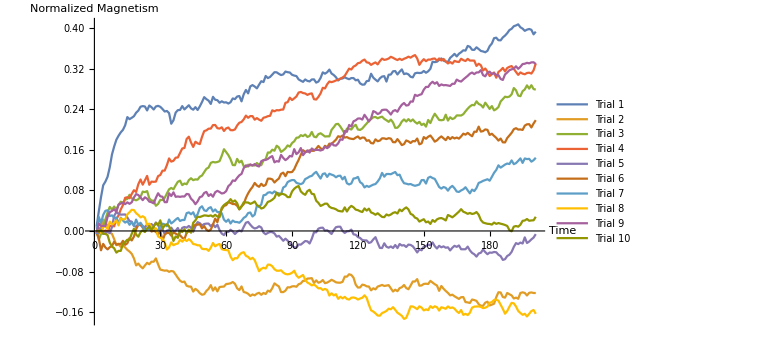

0.175661

```mathematica
magnetism1={334,1546,2662,3608,3894,4282,5034,6036,6666,7202,7518,7784,7982,8340,8988,8826,8932,9056,9334,9502,9806,9856,9826,9514,9902,9772,9586,9828,9874,9802,9628,9430,9472,9304,8464,8736,9342,9536,9552,9856,9594,9758,9924,9678,9572,9776,9550,9834,10176,10562,10406,10286,10026,10588,10358,10324,10122,10234,10140,10156,10058,10162,10460,10406,10612,10652,10230,10790,11130,10860,11412,11514,11402,11256,11550,11820,11754,12234,12066,12158,12342,12532,12522,12404,12306,12358,12582,12532,12508,12328,12266,12226,11962,11862,11770,11958,11846,11804,11958,11966,11710,11792,12078,12520,12414,12528,12738,12428,12310,12136,11876,12014,12036,12130,12044,11978,12068,12068,11892,11938,11650,11548,11560,11830,11854,12410,12102,11944,11806,12048,12188,12220,11792,12330,12348,12604,12622,12354,12570,12750,12380,12436,12362,12168,12124,12444,12486,12466,12484,12628,12488,12604,12798,13360,13326,13360,13502,13618,13444,13372,13340,13660,13812,13980,13778,13988,14108,14260,14238,14606,14534,14300,14294,14496,14360,14210,14170,14106,14222,14586,14794,15216,15256,15056,15048,15278,15422,15612,15856,15960,16160,16224,16310,16078,15972,15796,15890,15944,15878,15522,15732}/(200*200); (*This is the same as the stored iamges *)
magnetism2={-272,24,330,894,566,466,-118,-230,-644,-1124,-1066,-1250,-1154,-1300,-1492,-1626,-1806,-2166,-2716,-2574,-2792,-2950,-2724,-2514,-2628,-2426,-2428,-2164,-2636,-3048,-3094,-3134,-3116,-3224,-3160,-3196,-3440,-3700,-3928,-4034,-3996,-4324,-4386,-4396,-4784,-4570,-4704,-4910,-5034,-4994,-4732,-4570,-4276,-4708,-4452,-4770,-4426,-4402,-4390,-4192,-4168,-4130,-4030,-4170,-4528,-4670,-4378,-4818,-4864,-4958,-5132,-5012,-5082,-4948,-4880,-5040,-4894,-4976,-4710,-4796,-4512,-4136,-4268,-4376,-4824,-4826,-4710,-4446,-4458,-4374,-4362,-4402,-4206,-4142,-3936,-3934,-3756,-3748,-3726,-4108,-3898,-4086,-4026,-3874,-4120,-4074,-3974,-3854,-3942,-4054,-4080,-4084,-4016,-3606,-3604,-3418,-3474,-3688,-4242,-4464,-4458,-4238,-4272,-4372,-4388,-4688,-4526,-4612,-4390,-4328,-4260,-4342,-4310,-4278,-4530,-4780,-4636,-4752,-4512,-4442,-4264,-4504,-4602,-4308,-3990,-3990,-3802,-4320,-4300,-4180,-4162,-4186,-3940,-4074,-4204,-4304,-4728,-4344,-4562,-4736,-4890,-5082,-5030,-5156,-5260,-5364,-5228,-5220,-5614,-5638,-5686,-5412,-5456,-5518,-5780,-5906,-5908,-5660,-5584,-5878,-5816,-5744,-5228,-4838,-4858,-5214,-5260,-4894,-4996,-5088,-5330,-5260,-5356,-4896,-4846,-4892,-5094,-4880,-4854,-4896,-4898}/40000;
magnetism3={46,-686,-236,378,906,1452,1900,1684,1928,1674,2060,2310,2216,2478,2526,2856,2564,2486,2418,2506,2688,3106,3066,3148,2568,2392,2394,1990,2130,2450,2440,2612,2954,3286,3396,3286,3606,3882,3972,3618,3748,3688,4012,4160,4010,4074,4054,4282,4378,4646,4906,5006,5372,5448,5410,5442,5516,5938,6452,6226,5988,5660,5204,5190,5690,5404,5542,5110,5054,5228,5182,5194,5170,5364,5204,5198,5576,5672,6194,6184,6414,6334,6728,6596,6238,6358,6512,6754,6652,6938,7076,7356,7378,7560,7490,7610,7422,7502,7814,7444,7398,7642,7712,7588,7456,7470,7468,7980,8190,8430,8454,8238,7968,7680,8076,8068,8008,8250,8380,8008,7974,8088,8294,8486,8692,8830,8980,8996,8892,8972,9022,8848,8740,8614,8792,8564,8138,8150,8336,8636,8804,8638,8828,8654,8800,8602,8474,8612,8362,8468,8236,8762,8516,8934,9254,9010,8760,8740,8772,9178,8714,8974,8834,8908,9120,9118,9114,9218,9446,9652,9826,9948,9926,10230,10024,9946,9744,10126,9890,9632,9856,9520,9618,9782,10222,10408,10598,10562,10608,10784,11282,11102,10686,10638,11030,11174,11492,11236,11504,11202,11154}/40000;
magnetism4={-14,224,-124,-68,38,-34,404,398,360,938,1230,1696,2042,2616,2662,2582,2920,3216,3076,3692,4062,3654,3990,4346,3644,3894,3878,3896,4328,4416,4758,4766,5188,5726,5474,5540,5784,5802,6156,6510,6552,7260,7440,6980,6634,7044,6916,6858,7426,7882,7944,8072,8080,8356,8366,8114,8082,8182,7892,8098,8164,7958,7950,8014,8326,8542,8602,8808,9104,8934,9068,9062,8784,8908,8786,8698,8936,8982,9060,9090,9524,9446,9536,9520,9574,9586,10114,10166,10520,10334,10468,10618,10926,10972,10886,10854,10740,10824,10860,10404,10374,10582,10860,11300,11250,11580,11798,11746,11802,11882,11936,12026,12110,12242,12530,12814,12746,12974,13066,13244,13280,13440,13528,13310,13274,13110,13218,13306,13148,13404,13604,13504,13540,13610,13748,13668,13570,13492,13594,13498,13592,13658,13756,13682,13800,13882,13618,13110,13372,13560,13402,13528,13524,13592,13614,13448,13618,13452,13582,13382,13222,13338,13212,13424,13364,13336,13592,13482,13416,13584,13450,13452,13444,13028,13198,13080,12662,12824,12582,12228,12370,12508,12098,12552,12682,12868,12596,12864,12958,13014,12798,12548,12320,12514,12416,12368,12470,12492,12422,12682,13220}/40000;
magnetism5={300,-200,204,-228,-170,-72,-176,310,1200,1490,1360,1290,1296,1302,1062,778,736,404,320,552,450,384,298,502,472,544,368,670,498,72,126,-236,26,68,262,8,22,234,-146,246,312,260,394,258,-66,360,698,616,430,550,578,582,374,534,300,490,64,-204,-324,-72,-82,96,-36,-242,-66,38,-34,322,652,712,494,302,194,246,374,274,-124,-256,-152,-82,-92,-196,-448,-388,-568,-776,-610,-764,-972,-1170,-1290,-1314,-1068,-1080,-938,-796,-820,-988,-614,-106,-108,180,246,260,28,60,-88,-238,68,296,336,334,4,-158,-28,-16,106,-264,-298,-480,-552,-718,-746,-750,-946,-888,-668,-490,-930,-1336,-1348,-974,-1244,-1320,-1222,-1344,-1110,-1350,-1028,-1148,-1122,-1264,-1078,-1102,-1210,-1432,-1696,-1458,-1526,-1232,-1194,-1072,-1128,-904,-1198,-1386,-1172,-1290,-1218,-1324,-1290,-1536,-1328,-1172,-1254,-1144,-1442,-1446,-1442,-1236,-1532,-1732,-1838,-2026,-1780,-1720,-1466,-1668,-1834,-1704,-1720,-1660,-1682,-1878,-1986,-2284,-2228,-1976,-1874,-1652,-1258,-958,-1036,-918,-990,-506,-952,-834,-664,-524,-248}/40000;
magnetism6={-162,-582,-1526,-1020,-1298,-1452,-1284,-1186,-846,-1080,-1014,-1044,-778,-1098,-972,-556,-750,-444,138,484,548,248,158,116,262,-44,16,-66,-276,8,-774,-304,-148,-156,-370,-106,-210,-308,-338,-536,-646,-144,-18,-86,318,504,494,532,206,388,100,2,110,504,974,690,1386,1720,1976,2040,2276,2214,2124,2124,1990,1704,1950,2116,2612,2968,3250,3476,3790,3590,3486,3724,3550,3644,4128,4130,4072,3824,4000,4136,4508,4604,4324,4660,4636,4652,4876,5266,5610,6010,6380,6242,6258,6370,6326,6332,6494,6712,6526,6426,6724,6606,6892,6852,7042,7206,7476,7424,7530,7372,7410,7312,7276,7252,7370,7460,7278,7376,7362,7116,7164,6936,6910,7234,7086,7134,7312,7306,7254,7324,7290,7010,7004,7250,7028,6778,6854,7144,7072,6946,7096,7076,7298,6836,6916,7410,7278,7438,7534,7310,7050,7152,7332,7464,7312,7168,7426,7246,7408,7302,7374,7288,7462,7680,7600,7742,7600,7476,7838,7828,8234,7844,7884,8016,7980,7580,7674,7504,7350,7134,7296,6998,6990,7336,7538,7746,8030,8112,8004,8014,7974,8316,8418,8428,8170,8484,8746}/40000;
magnetism7={-248,1106,618,1266,1590,1632,1176,1232,1048,1050,598,1048,828,660,772,490,688,406,898,476,648,392,-18,152,102,292,306,58,72,370,574,522,376,904,594,730,896,1026,788,866,864,1404,1466,1318,1476,1072,1324,1808,1948,1632,1574,1796,1878,1534,1700,1490,1492,1396,894,724,906,588,820,710,704,648,806,1032,1144,1414,1458,1142,1288,2004,1888,2100,2818,2856,3022,3060,2966,3126,2982,2976,2886,3432,3532,3856,3956,4018,4014,3800,3740,3696,3782,4096,4184,4296,4348,4534,4666,4394,4138,4498,4546,4268,4516,4446,4382,4238,4346,4362,4074,4272,3766,3670,3750,4138,4168,4266,3852,3732,3436,3560,3480,3572,3656,3704,3902,4156,4584,4286,4496,4496,4480,4570,4654,4404,4444,4046,3770,3734,3680,3706,3620,3566,3612,3670,4012,4020,3742,4196,4280,4176,4110,3794,3468,3346,3468,3404,3182,3424,3558,3370,3112,3080,3198,3288,3452,3202,2970,3264,3148,3392,3794,3860,3956,4018,4082,3968,4270,4588,4816,5180,5000,5118,5240,5322,5284,5568,5274,5356,5534,5728,5372,5724,5672,5694,5470,5586,5780}/40000;
magnetism8={-18,24,-156,328,360,156,740,512,646,826,440,994,910,926,1316,1480,1670,1648,1400,1264,1074,1160,1044,474,584,340,174,214,-428,-538,-624,-892,-1466,-1296,-900,-1128,-1030,-994,-696,-844,-662,-792,-648,-786,-1032,-1062,-1132,-1134,-1410,-1436,-1420,-1568,-1320,-950,-1214,-1084,-1030,-1436,-1490,-1508,-1532,-2022,-2310,-2144,-2162,-1894,-1734,-1676,-1962,-2044,-2226,-2118,-2304,-2750,-3178,-2992,-2900,-2966,-2658,-2666,-2788,-3020,-3138,-3140,-3106,-3286,-3394,-3426,-3388,-3298,-3138,-3508,-3690,-3584,-3474,-3850,-4072,-4164,-4296,-4222,-4366,-4528,-4516,-4658,-4574,-4656,-5100,-4918,-5088,-4990,-5354,-5192,-5322,-5202,-5370,-5412,-5268,-5250,-5298,-5414,-5332,-5274,-5082,-5288,-5816,-6264,-6362,-6502,-6674,-6688,-6480,-6408,-6310,-6138,-6178,-6016,-6228,-6454,-6570,-6700,-6944,-6856,-6442,-5956,-5964,-6056,-6172,-5948,-6048,-6272,-6186,-6252,-5936,-6072,-5948,-6018,-6284,-6020,-6076,-6146,-5956,-6084,-6034,-6134,-6338,-6476,-6242,-6624,-6542,-6636,-6454,-6052,-5972,-5962,-5956,-5990,-6092,-6056,-5974,-5674,-5614,-5448,-5430,-5504,-5824,-6150,-6530,-6320,-5978,-5676,-5716,-5964,-6312,-6474,-6616,-6538,-6750,-6538,-6324,-6238,-6542}/40000;
magnetism9={-174,584,398,398,384,1112,1480,1580,1706,1510,2090,2158,2236,2120,2258,2142,2266,2642,2912,2840,2640,2432,2658,2546,2318,2272,2178,2616,2976,2738,2702,2274,2274,2978,2758,3048,2696,2722,2692,2726,2720,2922,2892,2546,2378,2114,2336,2668,2726,3000,3082,2760,2904,2702,3054,3166,3076,2958,2996,3142,3540,3692,3988,3950,4190,4392,4504,4960,5176,5092,5260,5160,5280,5148,5090,5506,5594,5606,5684,5816,5910,5416,5514,5472,6002,5762,5592,5720,5922,5880,6460,6068,6212,6544,5984,6194,6362,6188,6510,6384,6400,6400,6350,6424,6642,6536,6664,6924,6762,6736,6910,7236,7194,7890,7828,8366,8242,8656,8734,8874,8882,8794,9168,8924,8642,8898,9462,9382,9232,9306,9546,9572,9570,9404,9190,9462,9540,9410,9728,9962,10100,9902,9932,10220,10208,10750,10660,10742,10798,11152,11370,11368,11624,11776,11622,11742,11448,11566,11502,11516,11484,11448,11616,11618,11948,11844,11794,11956,12102,12244,12414,12504,12380,12510,12516,12694,12300,12208,12488,12570,12384,12464,12302,12298,11998,11920,12356,12510,12688,12758,12816,12998,12798,12958,13174,13200,13270,13232,13306,13316,13176}/40000;
magnetism10={84,-84,72,-226,-226,-328,-920,-1230,-1364,-1708,-1574,-1572,-1026,-868,-690,-696,-224,176,-290,-452,-102,52,-86,202,380,80,358,624,444,840,178,440,528,370,-146,-790,-432,-542,48,-78,136,-158,108,-136,648,834,1128,1100,1164,1228,1214,1182,1230,1128,1274,1144,1086,1830,2044,2176,2280,2510,2292,2408,2194,1712,1924,2264,2252,2242,2140,2210,2330,2034,1954,1772,1828,2024,2296,2354,2464,2618,3028,2780,2950,2912,2842,2670,2676,3116,3332,3470,3546,3122,2956,2852,3144,3250,2930,2898,2386,2216,1976,2056,2156,2152,1916,1816,1782,1712,1594,1558,1538,1862,1536,1818,1978,1868,1684,1642,1554,1494,1780,1608,1762,1462,1392,1278,1400,1252,1108,1092,1302,1220,1298,1424,1482,1376,1696,1560,1740,1860,1704,1350,1264,1052,980,740,838,928,684,746,556,862,722,914,996,1018,944,828,1260,1178,1076,1212,1368,1526,1720,1518,1446,1350,1422,1340,1382,1490,1278,862,666,610,566,552,504,662,558,624,572,530,472,394,64,-28,344,388,338,494,800,828,942,804,832,842,1118}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT2=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
(*Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]*)
```

### 200x200, kT=2.5, 200 time steps

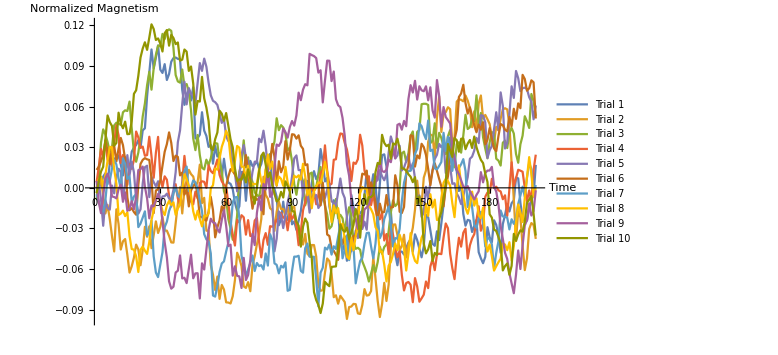

0.0331981

```mathematica
magnetism1={208,186,62,332,432,112,732,712,870,844,960,692,366,906,784,590,1068,1190,1266,1408,1186,1698,1760,2712,3404,4088,3528,3848,4204,3494,3394,3654,3186,3362,3728,3834,3850,3810,3798,2894,2452,2760,2890,2580,2974,1460,1468,1570,2234,1690,1534,1210,1268,714,1238,924,1026,310,860,384,154,118,-38,-446,-676,-548,474,448,-382,408,798,642,688,800,566,704,1014,882,814,1000,60,-28,-262,-1106,-926,-408,-942,-944,-470,-1078,-992,-1242,-970,-692,-170,90,206,-504,154,494,258,392,1146,764,188,298,-544,-904,-364,-500,-690,-1594,-1844,-1658,-2154,-1570,-208,-562,-722,-694,-752,-668,-216,488,-214,4,402,124,-756,122,966,990,634,-300,-692,-1566,-1952,-2286,-1876,-1884,-1970,-1778,-1618,-1528,-1882,-1372,-1544,-1798,-2052,-1720,-794,-868,-1260,-1654,-1712,-1284,-1544,-1042,-496,84,704,1488,760,684,492,-94,84,-770,-1118,-946,-968,-1304,-1118,-944,-1900,-2082,-2226,-2038,-1162,-1462,-1608,-958,-1094,-1416,-1918,-1068,-802,-476,-698,-454,-368,304,280,-442,-922,-974,-968,-612,-350,-220,678}/(200*200);
magnetism2={-12,8,258,-224,-756,-506,-926,-1424,-1878,-634,-1066,-1822,-1580,-1512,-1980,-2504,-2316,-2062,-1676,-1820,-2286,-1834,-1150,-1444,-1138,-1782,-1394,-990,-1334,-1152,-854,-1262,-1264,-1418,-1612,-1618,-1044,-460,18,-756,-62,228,532,406,334,46,162,686,-452,-294,-1266,-1266,-2284,-2566,-3018,-2620,-3280,-2868,-3002,-3382,-3388,-3416,-3200,-2724,-1916,-2078,-2314,-2910,-2956,-2784,-3054,-2286,-2022,-1668,-1362,-918,328,-206,-320,-598,-662,-1272,-704,-406,-626,-620,-784,-558,-984,-598,-552,-1134,-1354,-1500,-1676,-1360,-1946,-2020,-1688,-1690,-2024,-2890,-3040,-3024,-2502,-2086,-2164,-2532,-3230,-3174,-3422,-3188,-3278,-3374,-3872,-3522,-3506,-3428,-3436,-3708,-3726,-3462,-2990,-3182,-3168,-3046,-2038,-2672,-3338,-3816,-3436,-2806,-3342,-2858,-1736,-1088,-1080,-1394,-1852,-1706,-1386,-2058,-1670,-1486,-1178,-644,212,-424,-496,302,514,1358,1576,1544,868,2082,2700,1652,2194,2236,2380,2324,1278,1500,2546,2620,2600,2556,2728,2578,2354,1792,2262,1690,2488,2728,2048,2154,2026,1882,1482,1378,1804,1694,2040,2318,2352,2318,1860,718,-348,-1572,-690,-878,-1710,-2430,-2082,-1216,-1040,-1096,-1508}/40000;
magnetism3={-348,342,1332,1728,1576,1352,1062,1174,1844,1924,1894,1862,2232,2290,2270,2548,1760,1052,770,1042,1504,2110,2494,3036,3428,2900,3536,3926,4204,4178,4548,4396,4628,4682,4638,4132,3334,3144,3108,3496,3006,3066,2844,2290,1460,1114,1562,966,594,544,832,672,874,1196,1322,1306,800,496,-98,-294,-926,-1198,-1534,-1362,-812,474,710,1404,610,900,366,174,-136,-204,-278,78,36,-12,524,944,1132,1368,2056,1702,1852,1782,1608,1106,1182,778,110,-204,216,378,206,-516,-294,414,450,-60,0,396,616,-206,-524,-786,-1208,-1134,-812,-328,-898,-796,-900,-1288,-856,-572,-806,-1606,-1802,-1770,-1828,-2170,-2334,-2510,-2768,-2530,-2282,-2488,-2192,-1740,-1950,-1746,-1674,-1280,-724,-370,-538,-468,-12,1020,1070,764,1022,1530,1666,972,1654,1710,2470,2484,2482,2448,1322,1388,1908,1180,1626,1470,1232,996,1522,1706,1212,614,1296,1348,1040,1548,2158,1738,1792,2038,1970,2734,1904,2212,1492,1162,872,1346,1646,1610,860,806,658,1334,1394,1174,1628,1770,1604,1002,742,1286,1542,2116,1964,1770,2772,2562,2126}/40000;
magnetism4={164,622,1150,914,1372,824,996,640,1338,1850,1552,732,972,506,90,702,562,824,1664,1488,1182,1218,948,968,1510,934,296,1038,1506,352,20,340,240,-230,-552,-142,108,-316,-460,170,944,348,-348,-400,-488,-110,-316,140,194,178,0,670,496,432,622,838,382,196,86,42,-458,-994,-1386,-1704,-942,-1022,-808,-870,-1382,-954,-1422,-1424,-966,-888,-1592,-2052,-1542,-1336,-1682,-1132,-1148,-1084,-942,-914,-738,-886,-842,-1254,-776,-914,-798,-1120,-1694,-1298,-666,-412,-116,8,-26,-128,-484,-210,432,536,1256,520,78,120,830,844,1348,1606,1592,1328,1132,762,202,748,708,848,1568,1248,514,270,344,-510,-164,-646,-892,-930,-714,-1554,-1364,-1956,-1180,-1388,-1758,-2050,-1876,-2570,-3032,-2812,-2780,-2862,-3378,-2666,-2916,-3364,-3264,-3154,-2766,-2962,-2320,-2108,-2432,-1966,-1944,-1958,-1470,-1052,-1192,-1950,-2370,-2696,-1996,-1474,-1736,-1326,-1206,-2088,-1698,-1494,-1366,-954,-544,-1266,-1074,-264,-138,-152,268,-2,34,-72,-106,-336,-220,-830,-26,756,52,280,534,508,476,6,-396,-76,-400,528,980}/40000;
magnetism5={-4,148,-336,-1120,-364,-600,-644,68,-164,298,564,466,-254,88,966,376,772,456,-356,-762,-634,132,610,654,-274,320,168,48,196,-474,-254,-246,-172,-310,-340,-62,462,1348,1700,2476,3134,2466,2948,2774,2730,2500,3096,3686,3454,3818,3578,3108,2734,2572,2530,2450,2190,1918,2048,1520,1380,1390,534,430,-104,362,964,1262,910,784,16,476,772,768,1452,1348,1688,1232,588,-60,-318,-1876,-1502,-698,-808,-1188,-814,-436,-146,332,872,958,524,524,-244,256,-196,-732,-268,-264,-212,-596,-492,-264,-298,-58,118,-396,-450,-524,-128,276,-142,-300,-866,-1848,-1876,-1638,-1264,-1484,-1132,-1214,-998,-1236,-390,-150,178,188,226,522,338,224,406,1040,1518,1294,868,956,1244,514,598,788,982,534,724,280,-414,-224,-858,-724,32,-332,176,526,854,976,1298,1198,1316,436,588,642,118,136,-162,-284,-480,-244,40,316,858,922,1102,1476,1320,2146,2128,1936,884,1112,1236,1732,2234,1710,2820,2420,1162,1336,2196,3000,2656,3452,3238,2856,2944,2960,2918,2678,2546,2024,2432}/40000;
magnetism6={530,626,788,968,1402,1094,704,1186,1242,782,1156,1476,1264,840,-284,-662,-600,-714,-794,92,708,826,878,842,824,272,-746,-76,-46,222,652,1066,1292,1638,1328,792,950,914,368,454,-198,-46,-548,-78,64,114,-180,-878,-854,-930,-968,-706,-266,-654,-1462,-1166,-960,-548,-724,58,328,552,496,392,252,-18,298,468,966,508,-108,-616,-272,-354,-314,-228,-780,524,756,712,1298,922,62,786,460,624,1380,836,1116,1584,1572,1454,1552,1244,1152,670,696,-94,-468,-76,48,82,-516,154,-480,-1378,-1422,-1784,-1862,-1976,-2128,-1372,-1664,-1432,-1606,-1500,-1700,-1420,-1422,-800,-28,420,396,510,-296,162,-58,-432,-1084,-466,-730,-712,-212,-682,-572,-570,372,70,-706,-744,-566,438,658,1552,1534,628,958,870,1302,1204,970,560,78,518,726,500,264,44,-548,24,344,858,1348,1436,1718,2684,2788,3044,2502,2194,2378,2128,1840,1642,1868,1718,1938,1282,1418,1766,1452,1164,1084,1530,1886,1848,1718,1668,2096,1822,2336,2038,2496,2352,3338,3214,2870,2942,3176,3118,2048}/40000;
magnetism7={-190,-400,-634,-702,-366,302,206,570,822,694,284,-32,876,710,262,346,-434,-256,-186,-1160,-1054,-878,-694,-1410,-1264,-966,-2022,-2502,-2636,-2270,-1902,-1160,-1000,-686,-508,-166,14,-234,-290,90,490,630,-94,20,220,162,-22,-380,-684,-1368,-1522,-1578,-1938,-3180,-3212,-2898,-2482,-2234,-2172,-1880,-1616,-1196,-430,-280,-270,-898,-2008,-2300,-2594,-2406,-2218,-1998,-2456,-2220,-2310,-2284,-2414,-1938,-2296,-1368,-1536,-2230,-2274,-2526,-2302,-2354,-2200,-3040,-3014,-2454,-2032,-2032,-2006,-2452,-2506,-1782,-1646,-2032,-2042,-2034,-2694,-3500,-2506,-2358,-1766,-1820,-1674,-1972,-1726,-1804,-1436,-1106,-2082,-1836,-1402,-2136,-1758,-1734,-2820,-2468,-2162,-2068,-1640,-1336,-1324,-1734,-2082,-1654,-858,-1488,-1332,-922,-744,-550,-1134,-1730,-1484,-1500,-1212,-400,152,410,494,504,626,1010,1150,1904,1822,1598,1440,1990,1090,1128,578,546,648,764,1626,1090,1506,1018,502,976,550,584,696,848,498,-566,-124,-566,-1100,-1182,-912,-710,-1028,-1732,-1470,-1518,-1670,-2386,-1918,-1580,-668,-844,-854,-882,-1228,-928,-1064,-890,-474,-230,36,-264,310,732,552,-220,82}/40000;
magnetism8={20,256,334,32,374,808,1210,1202,544,128,-802,-760,-672,-834,-720,-1422,-1808,-1826,-2020,-2486,-1830,-1734,-1856,-1952,-1598,-950,-658,-352,-212,-406,-684,-804,-520,-388,-506,-426,-798,-610,-496,-18,404,256,58,-228,-692,-938,-674,-912,-1138,-816,-838,-764,-8,74,574,538,866,1210,1404,1686,1528,886,484,790,1238,1186,630,618,284,654,194,94,118,106,552,192,-46,554,984,556,778,334,82,334,266,60,620,164,-90,66,356,308,370,244,712,338,-220,-38,-602,-104,44,160,144,404,768,452,-434,-1016,-518,-752,-600,-1116,-1062,-1510,-2034,-2102,-1464,-1844,-1420,-1118,-164,20,-24,-18,-528,-632,-778,-1160,-1276,-1890,-1876,-2268,-2764,-2300,-2190,-1956,-1644,-1842,-1384,-1600,-1778,-2442,-1954,-1338,-1946,-2156,-2224,-1790,-1470,-1332,-474,-826,-188,-582,-348,-950,-934,-296,150,264,202,64,-454,-866,-84,666,102,-218,-586,-766,-510,-112,-526,-310,-814,-896,-582,-1540,-1882,-1676,-2020,-2444,-2314,-2196,-2094,-1648,-1674,-1842,-1606,-2150,-1724,-1016,-492,-726,-1010,-294,310,908,402,-260,-10}/40000;
magnetism9={202,-430,-748,-228,286,418,222,-254,-270,-310,-38,96,-412,-132,-678,-624,-394,-636,-272,522,554,628,30,-314,-900,-518,-546,-370,-178,-412,-990,-1606,-2054,-2762,-2978,-2920,-2500,-2448,-1996,-2676,-2656,-2814,-2394,-1974,-2672,-2526,-2522,-3268,-2230,-2414,-1824,-1248,-912,-1020,-1046,-1216,-1318,-952,-650,-1124,-1718,-1678,-2594,-2316,-2598,-2616,-2958,-2068,-2724,-2574,-2134,-1358,-1690,-744,-278,-666,120,-52,554,-264,-194,594,1280,1238,1360,1756,1644,1482,1798,1974,1838,2140,2812,2588,2900,3062,3028,3958,3922,3892,3834,3404,3474,2524,3166,3758,3754,3154,3436,2620,2440,2384,2064,1538,706,356,-348,-818,-928,-1210,-810,-1146,-638,-578,-498,-210,-54,138,398,812,496,468,536,836,758,1124,876,1860,1894,1718,1978,1820,2622,3034,2816,3162,2608,3002,2882,2854,3000,2586,2970,2286,2076,3184,2718,1806,2386,2092,2000,1900,1202,876,538,406,224,36,-2,52,-98,-218,-344,-208,-104,464,162,442,510,512,620,36,-110,-492,-1124,-1510,-1920,-2100,-2524,-2822,-3112,-2568,-1850,-2398,-1698,-1108,-954,-460,-818,-686,-72}/40000;
magnetism10={-156,186,482,622,1432,2138,1942,1828,1244,1326,2220,1898,1760,1956,1586,1592,1974,2778,2882,3308,3850,4116,4300,4076,4440,4830,4692,4368,4414,4264,4028,4568,4662,4200,4518,4426,4246,4294,3758,3788,4086,4024,3454,3586,3080,2164,2566,2548,3278,2644,2370,1974,1178,1118,1438,1636,2278,2192,1980,2210,1830,1432,1198,570,206,250,238,400,160,546,264,-226,-468,6,482,948,1040,684,316,456,90,-174,-402,-352,-118,-286,192,54,-114,-676,-704,-994,-1116,-1736,-1148,-906,-1032,-1598,-2088,-3080,-3314,-3458,-3698,-3418,-2778,-2850,-2904,-2338,-2326,-2320,-1708,-1078,-1236,-1296,-1172,-1510,-1308,-1094,-624,-848,-1472,-726,-188,-490,-274,-274,-200,460,736,702,1566,1328,1232,1274,860,1310,1278,1454,1152,574,566,502,402,328,168,316,-472,-252,-628,-1646,-1936,-1816,-1572,-2160,-1922,-1988,-916,-718,-322,92,1294,1096,914,1468,1410,1068,1450,1456,1142,1308,1414,1178,1516,1202,996,826,732,420,172,-780,-880,-1232,-1274,-1454,-1650,-2440,-2310,-2234,-2568,-2304,-1360,-1562,-1376,-1254,-1294,-996,-444,-348,-242,-766,-1408}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT25=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### 200x200, kT=3 , 200 time steps

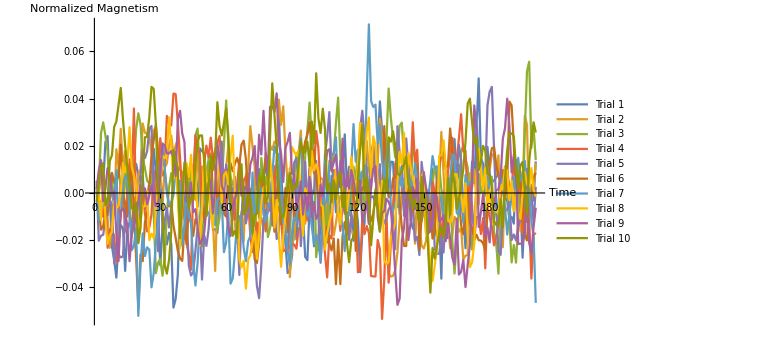

0.0129532

```mathematica
magnetism1={-236,-16,440,124,862,964,-62,-914,-1130,-1436,-828,-546,-596,-1322,-608,-498,336,282,492,304,206,298,-278,-88,172,172,754,342,-354,-1224,-596,-526,-872,-674,-870,-1944,-1798,-1382,-78,-440,-12,-820,214,134,278,368,-234,758,712,670,308,110,68,-626,-614,-678,-152,726,164,376,36,-280,-452,40,-342,-574,-404,90,-78,-336,-154,-324,24,64,404,214,264,516,106,356,310,-226,574,1346,320,-192,-856,-1358,-1308,-1066,-236,-786,-222,-450,-372,-1084,-1138,-224,42,-904,-794,-966,-552,174,-186,-842,-614,294,256,-328,128,238,374,994,114,444,-404,-810,-148,-498,-1342,-682,-520,352,-60,-74,-56,-202,758,1554,1058,26,18,126,530,526,-192,284,-364,-132,-58,-266,328,-456,-598,-650,-240,-318,126,258,-376,-204,-610,406,-596,-748,-448,-1454,42,-130,-766,142,590,914,182,482,-172,-400,-938,-66,-110,532,164,1078,1944,590,498,-44,782,328,178,214,266,388,350,158,-80,-136,-442,-406,-520,562,-234,-152,-1098,-220,-308,102,-172,-108,534}/(200*200);
magnetism2={-74,32,282,366,-220,-418,-930,-486,-356,742,442,1088,418,712,-14,-156,-754,-76,-376,316,402,1178,1024,998,972,666,1058,1124,690,372,-246,430,498,802,972,648,808,900,388,358,132,354,204,488,412,-118,840,56,450,390,300,532,-38,-500,-1322,-88,688,584,106,446,782,-66,-172,-526,-848,-610,-328,-816,310,396,1134,782,452,-1068,-512,-416,-622,270,102,804,730,872,830,1584,1154,1470,684,170,-1428,-856,-780,-240,664,1060,96,-522,-182,472,472,786,272,110,258,230,-654,-82,-446,-364,-720,-510,-232,-50,-156,168,-322,-648,-630,-706,-674,82,342,146,744,884,406,76,576,316,500,1260,952,206,-620,-1358,-1418,-1406,-1314,-1010,-460,92,-184,260,170,186,38,-860,-198,-508,-892,-942,-816,-446,-384,-742,-522,-322,154,1036,330,-434,-452,-938,-710,-404,-458,-658,-604,-1124,-1064,-1050,334,94,400,-108,-194,364,264,202,262,406,642,666,312,640,-542,-920,290,154,-350,68,-306,-58,490,-644,-40,1308,1160,-434,138,90,512}/40000;
magnetism3={8,100,1014,1198,976,712,-74,334,-304,100,430,96,-296,498,-174,388,330,440,1080,1352,1164,590,420,210,160,322,-340,-1360,-1182,-1118,-1404,-1118,-330,98,336,86,688,-76,-554,-68,-250,-150,-56,504,190,980,1092,244,-906,-368,-66,612,670,42,-156,-614,-424,182,826,1570,798,282,142,130,34,170,114,-238,118,344,-136,-106,-568,10,-422,594,254,270,-748,-596,-50,246,326,470,-368,-640,-112,306,-828,186,256,674,136,42,-168,628,1066,1534,924,704,-1090,-714,-300,-480,-200,-732,544,380,660,1184,1618,618,-112,-6,-318,-380,-160,446,226,716,-184,110,-434,428,426,258,798,560,54,256,116,-286,900,1772,1276,912,606,636,1140,1194,562,46,242,-84,830,614,492,-332,-486,-316,-106,50,-422,164,450,242,456,64,-502,-30,-310,78,-834,-1366,-824,-220,704,802,578,430,-258,-960,-688,78,328,4,140,-420,-94,250,274,-672,-862,-1368,-348,-408,262,70,-490,-1178,-882,-1182,-456,236,-274,1042,2064,2226,764,1106,556}/40000;
magnetism4={-174,-216,-138,-404,-120,-930,-614,-644,-724,-1170,-430,176,4,-656,10,572,164,1434,-258,-590,-338,90,-344,-652,-586,-364,394,-242,276,930,498,454,1308,1174,1146,1686,1676,1184,596,-16,-418,-850,-1048,-1302,120,978,730,682,-364,506,804,610,938,550,722,860,966,426,388,362,328,148,-170,-452,148,548,-50,214,274,-120,-728,-1002,-704,-504,-774,244,-60,-652,-70,-304,166,454,-372,-230,-368,-988,-964,-876,-928,-866,-874,-946,-598,-600,-258,-184,-466,218,698,332,1052,758,14,-624,-1030,-1432,-722,-772,390,110,-188,-642,-208,-308,-354,38,524,-196,-158,-1346,-1300,-410,-698,-560,-678,-1408,-1414,-1416,-796,-948,-2136,-1472,-360,-1522,-854,-220,490,604,162,126,-286,378,538,382,1200,506,734,-220,328,-268,-404,-106,-576,184,12,-248,-62,-818,-424,-526,362,614,936,602,568,928,1336,704,718,-190,140,-224,-778,-410,-392,-696,-424,-1278,-230,-408,-576,-888,-740,-522,-96,102,450,378,98,42,650,6,-10,366,-690,-276,-490,-446,-1452,-712,-676}/40000;
magnetism5={208,-810,-724,-710,-426,-260,-116,-198,-1198,-892,-1048,-1092,-1078,-422,-278,-360,-674,-214,-230,-832,292,720,592,706,1092,1136,20,-254,-988,576,-658,-478,-254,-586,-232,242,696,258,-770,-138,284,-376,-1230,-1400,-1342,-982,-580,-568,-1468,-716,-898,-616,-72,-170,-404,-332,-48,872,-74,480,232,132,0,272,-472,-1390,-398,116,-516,-308,-256,-530,-1030,-1574,-1784,-1224,-470,-288,-328,78,-554,-222,-780,-658,-38,-390,-680,-964,-366,-166,518,586,220,-902,-394,534,-242,406,-44,18,544,-392,-1184,-508,644,952,1372,392,282,84,126,546,-4,-352,-158,-794,-366,-494,-608,244,1084,1396,964,384,-146,674,852,186,162,488,-370,-518,-432,-276,-216,-410,-954,1132,686,536,-388,926,448,88,-302,-810,-744,-1052,528,208,-668,-694,-626,-28,-948,-1028,-1034,-742,-1010,-414,-158,130,366,432,260,812,550,-354,-640,-372,4,-364,-586,82,704,374,446,282,1488,1718,1800,740,-210,-990,-1050,-314,-308,-280,-116,-798,-704,-806,-578,-436,122,-204,408,-306,-28,-512,104}/40000;
magnetism6={26,-250,-624,-562,-318,-384,-36,342,172,288,264,820,-8,-172,-400,188,528,-360,-1098,-1950,-1042,-1156,-496,-350,98,636,892,1158,650,546,296,384,56,-228,-156,-548,-760,-986,-1110,-1152,-594,-872,-218,-526,-728,-446,-448,-556,-104,-496,70,2,28,628,422,-220,10,312,-352,-402,386,508,368,500,594,464,822,888,568,-182,70,-658,-1126,-1188,-862,-12,208,676,478,-50,-158,-658,-76,218,-530,-366,84,-662,416,10,-438,-186,-440,-328,674,874,994,1198,684,726,264,-40,-198,-624,-796,-570,-856,-976,-770,-1548,-788,-1546,-730,-494,-704,198,84,232,-982,144,82,54,138,234,-514,-470,-342,-74,-164,-248,-194,1134,258,-76,-40,246,306,220,-160,-578,-898,-900,74,44,-326,28,470,-964,-404,-110,-512,-662,-168,-774,-628,374,426,682,758,408,470,1094,674,38,-122,-2,-552,-698,-388,48,-514,-594,-796,-708,-800,-808,-852,-970,-130,540,758,776,478,288,192,388,-110,196,1550,1486,812,-52,330,164,-62,-712,-806,-194,-62,264,342}/40000;
magnetism7={92,-464,-190,-238,-88,-178,234,-46,-172,384,-708,-382,112,266,308,-300,-970,-898,-588,-2084,-1232,-684,-1070,-922,-960,-1600,-1362,-842,-526,44,844,434,-12,-202,-170,-34,412,192,208,-896,-534,94,-396,-504,-1190,-1570,-1186,-406,-158,154,-384,-330,-400,-148,-544,-108,-78,-126,-1004,-838,-326,-1538,-1448,-996,-438,-394,-512,-936,-1158,-822,-730,346,-358,-210,-288,82,-362,-492,-302,-24,294,794,670,662,54,-518,-572,-984,-1216,-664,-420,-470,650,926,68,-188,-396,-258,-570,-868,-712,-834,-1146,-490,538,-156,452,634,680,944,-208,-392,-542,-986,-396,-330,454,1170,530,732,104,368,234,1658,2860,1560,1458,1498,838,1156,536,234,568,910,-240,-300,-154,-238,444,96,236,102,246,112,152,506,228,96,-294,70,-152,-98,226,626,420,452,-12,-150,-458,-494,-258,216,650,636,-340,-364,78,-496,306,130,174,212,1054,1302,638,582,348,78,440,-34,-122,-434,-240,-164,348,120,-246,-706,-350,-52,276,-80,596,210,322,544,116,88,-472,-732,-1864}/40000;
magnetism8={176,-44,-460,330,-440,-862,-716,-660,-128,-260,-216,6,508,348,506,1116,444,292,128,-598,-468,-230,-226,38,-800,-692,-762,-308,114,80,632,588,678,1284,784,224,500,6,-938,-198,204,502,274,648,-88,340,-362,-892,-240,550,250,106,-336,-596,240,272,500,-168,300,358,146,624,972,-52,-160,-1122,-1264,-1148,-1622,-1130,-1056,-836,-648,-1116,-728,-174,94,118,-144,590,192,-588,-120,-728,-1252,-732,-370,12,306,782,698,634,728,-248,-728,80,-44,216,712,384,484,360,-194,-234,-956,-684,-500,-356,140,400,-312,-532,102,8,-306,6,612,292,-46,496,1186,862,490,1028,1280,256,960,816,206,-384,210,-1144,-1210,-1168,-756,-646,-506,192,698,486,1024,38,678,452,274,92,42,-70,290,356,-682,-748,-1226,-1494,-1226,-946,632,636,892,440,-440,-516,-376,318,318,-104,-16,-320,168,-746,-1256,-1176,-858,280,750,432,54,430,-282,50,-520,-288,-320,-336,128,56,438,374,-122,206,-306,50,-336,-442,8,354,152,112,422,50,-60}/40000;
magnetism9={70,380,558,-140,76,422,308,-18,28,-686,-1154,-316,-260,-324,-562,-1158,-698,-562,-414,-144,132,46,78,-188,-44,128,-68,-220,-216,300,830,810,674,670,712,594,288,1252,1394,1008,864,-146,-112,172,-324,-274,-580,-868,-800,-674,-266,168,214,-346,72,854,546,124,22,-250,-596,-730,-248,-102,50,272,-24,92,76,2,486,598,796,136,988,652,1394,668,376,1460,1476,1372,1690,868,674,186,766,868,1020,330,312,-250,-86,194,-366,-2,-296,272,-408,-154,-438,-368,136,-54,346,714,742,384,518,650,182,94,922,-94,328,74,388,226,-36,6,210,-490,-352,-144,-524,114,412,454,-406,-654,-332,-312,-100,-150,-264,-750,-1338,-1898,-1792,-802,-596,-116,-798,-498,108,-276,242,-394,-220,354,102,-188,-656,-444,-20,-70,-476,-452,-376,-818,-512,-766,-1096,-1214,-438,-1384,-1338,-1136,-1596,-1218,-884,230,1484,1080,-576,-332,-22,-744,-588,-838,-300,-220,52,58,262,920,1102,1600,1130,350,614,484,-864,-860,-856,-688,-46,-846,-1020,-578,-250}/40000;
magnetism10={-156,184,434,506,-210,-138,544,640,1122,1212,1494,1782,1256,808,426,104,-252,-308,-162,-852,-592,310,946,952,1290,1800,1766,1160,-18,-82,-210,-1214,-1368,-1134,-656,730,526,430,-768,-112,518,276,-272,-66,-110,506,876,976,976,534,-394,104,624,390,612,1540,1130,976,1194,1432,966,-122,-726,-644,-766,366,488,-362,-322,-4,-94,-678,-376,-350,314,164,392,-178,-62,966,1860,1326,780,-78,-396,-408,-224,52,342,-12,120,92,492,886,670,704,870,462,1212,836,2030,1270,1018,1430,1088,32,164,-162,216,-106,272,344,-240,56,-850,-1174,-800,-756,-576,252,718,1154,28,256,0,-888,-438,64,-242,-654,-108,232,20,944,870,1046,810,334,296,370,480,614,150,54,-264,-104,-296,-488,274,-184,-70,-974,-1690,-932,-1112,-902,-682,-568,-752,-524,254,-368,364,164,-276,-104,110,414,868,1516,1600,1194,836,944,388,530,800,720,330,298,78,-476,-544,-526,-104,-584,232,732,1006,1010,964,432,68,466,526,40,-362,536,908,1198,1026}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT3=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
(*Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]*)
```

### 200x200, kT=1.75 , 200 time steps

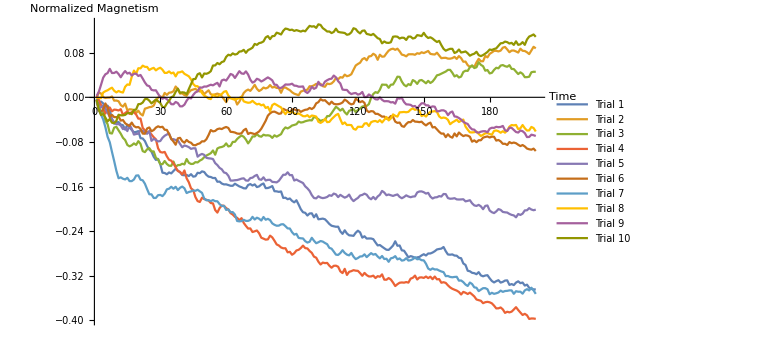

0.144439

```mathematica
magnetism1={-124,-588,-300,-436,-700,-598,-886,-1602,-1894,-1800,-1772,-1958,-2000,-2318,-1972,-2172,-2344,-2508,-2484,-2426,-2932,-2954,-3140,-3488,-3748,-3896,-4260,-4492,-4418,-4796,-5408,-5430,-5520,-5390,-5458,-5286,-5126,-5260,-5380,-5574,-5594,-5568,-5650,-5514,-5692,-5662,-5414,-5444,-5314,-5358,-5566,-5692,-5716,-5792,-5786,-6058,-6046,-6184,-6248,-6244,-6294,-6346,-6348,-6200,-6298,-6392,-6450,-6526,-6536,-6292,-6226,-6328,-6246,-6438,-6390,-6258,-6182,-6516,-6506,-6450,-6368,-6736,-6746,-6784,-6754,-7218,-7202,-7310,-7258,-7428,-7536,-7386,-7694,-8030,-8244,-8286,-8480,-8334,-8322,-8608,-8390,-8750,-8728,-8702,-8750,-8910,-9088,-9212,-9252,-9286,-9280,-9620,-9796,-9540,-9772,-9900,-9916,-9938,-9716,-9568,-9692,-10068,-9968,-10134,-10126,-10128,-10174,-10408,-10624,-10596,-10716,-10828,-10934,-10948,-10802,-10634,-10328,-10650,-10628,-10978,-11002,-11236,-11484,-11392,-11438,-11542,-11482,-11452,-11342,-11256,-11348,-11204,-11202,-11136,-11040,-10914,-10880,-10854,-10738,-11040,-11276,-11290,-11270,-11352,-11362,-11510,-11544,-11918,-12026,-12440,-12480,-12590,-12616,-12690,-12540,-12774,-12840,-12784,-12762,-12984,-13176,-13280,-13188,-13120,-13292,-13238,-13146,-13132,-13456,-13396,-13470,-13290,-13200,-13332,-13288,-13504,-13440,-13664,-13748,-13778,-13782}/(200*200);
magnetism2={-88,352,274,10,-46,-24,-20,62,-240,-232,-284,-556,-668,-454,-928,-860,-874,-916,-1124,-960,-1190,-1304,-816,-768,-708,-686,-596,-252,-20,70,-28,312,172,330,350,432,774,588,264,284,158,108,356,508,558,608,476,418,474,218,374,502,218,180,216,266,208,74,-130,-348,-42,-68,-70,-90,-520,-310,-12,310,468,554,462,660,894,610,450,544,700,636,698,878,700,748,672,664,322,676,706,600,512,362,260,206,150,406,470,516,544,792,788,860,964,942,962,798,756,988,946,992,1142,1388,1296,1444,1410,1626,1512,1558,1656,1974,2280,2390,2482,2730,2814,2654,2932,2956,3124,3022,2690,3056,2912,2928,3150,3346,3448,3488,3406,3488,3298,3062,3020,2938,3084,3088,3088,3050,3162,3122,3230,3172,3244,3324,3116,3086,3070,3200,3002,2806,2828,2834,2776,2772,2810,2900,2752,2956,2810,2552,2562,2304,2184,2232,2178,2502,2760,2588,2586,2966,2864,3116,3216,3332,3334,3292,3350,3560,3610,3434,3234,3352,3354,3290,3210,3486,3336,3322,3230,3100,3358,3622,3510}/40000;
magnetism3={-344,-592,-1118,-922,-1688,-1924,-2566,-2598,-2172,-2120,-2370,-2612,-2906,-3064,-3416,-3518,-3442,-3306,-3416,-3146,-3342,-3860,-3932,-3730,-3646,-3878,-3882,-4340,-4462,-4792,-4796,-4572,-4784,-4908,-4914,-4608,-4984,-4864,-4856,-4764,-4814,-4428,-4700,-4782,-4772,-4650,-4674,-4542,-4458,-4298,-4178,-4098,-4010,-3814,-4118,-3670,-3594,-3564,-3498,-3306,-3526,-3482,-3200,-3194,-2992,-2852,-2738,-2832,-3032,-3306,-3088,-2810,-2810,-2640,-2786,-2826,-2684,-2736,-2724,-2758,-2912,-2726,-2822,-2734,-2644,-2336,-2160,-2232,-2144,-2024,-1982,-1930,-1740,-1810,-1784,-1718,-1676,-1644,-1658,-1404,-1466,-1570,-1698,-1632,-1634,-1348,-1346,-1142,-906,-680,-802,-954,-818,-1070,-1230,-968,-908,-856,-1060,-912,-808,-666,-632,-614,-486,-40,236,372,314,542,912,902,898,682,904,918,1178,1478,1464,1128,896,788,946,876,1236,1146,962,1204,1242,1132,1004,1180,1026,1132,1332,1578,1618,1696,1772,1848,1968,1968,1760,1496,1584,1420,1484,1816,1906,1894,2160,2294,2098,2156,2520,2328,2230,1908,1958,1712,1754,1966,2118,2080,2276,2312,2234,2190,2306,2036,2026,1844,1668,1790,1682,1444,1446,1478,1796,1832,1828}/40000;
magnetism4={104,-182,-552,-810,-1170,-816,-732,-1006,-882,-900,-946,-850,-1264,-1130,-1014,-1188,-1060,-1080,-1234,-1530,-1528,-2196,-2366,-2494,-2498,-2666,-2862,-3012,-3660,-3924,-3962,-3918,-4238,-4482,-4546,-4754,-5014,-5290,-5348,-5540,-5248,-5812,-6098,-6532,-6652,-7156,-7446,-7508,-7202,-7298,-7350,-7408,-7584,-7610,-8088,-8270,-7950,-7760,-7784,-7948,-8050,-8306,-8410,-8576,-8644,-8814,-8670,-9010,-9224,-9414,-9406,-9664,-9612,-9554,-9750,-10072,-10138,-10210,-10190,-9924,-10050,-10288,-10554,-10630,-10772,-10830,-10828,-11120,-11084,-11294,-11186,-10988,-10940,-10812,-10638,-10818,-10842,-11024,-11158,-11430,-11504,-11792,-11992,-11856,-11894,-11880,-12080,-12224,-12088,-12078,-12154,-12486,-12610,-12304,-12742,-12518,-12470,-12400,-12436,-12450,-12612,-12804,-12596,-12756,-12850,-12850,-12794,-12964,-12830,-12872,-12702,-13080,-13086,-12966,-13072,-13288,-13540,-13406,-13302,-13282,-13296,-13254,-13292,-13010,-12948,-12790,-13070,-12928,-12916,-12956,-12856,-12970,-12868,-13048,-12856,-13058,-13042,-13302,-13264,-13314,-13490,-13636,-13736,-13802,-13864,-13964,-14146,-13958,-14020,-14110,-14010,-14142,-14284,-14504,-14552,-14596,-14768,-14698,-14672,-14704,-14780,-14944,-15142,-15136,-15076,-15214,-15464,-15382,-15428,-15376,-15222,-15054,-15258,-15440,-15614,-15532,-15636,-15898,-15864,-15868,-15894}/40000;
magnetism5={-370,-692,-726,-582,-808,-1100,-1392,-1542,-1798,-1936,-1918,-2026,-2282,-2182,-2424,-1968,-2252,-2676,-2634,-2610,-2352,-2398,-2554,-2616,-2412,-3124,-2980,-3064,-3164,-3138,-2904,-2758,-2668,-2594,-3012,-3002,-3066,-3088,-3348,-3582,-3458,-3502,-3576,-3698,-3656,-3656,-4260,-4136,-4060,-4130,-4342,-4376,-4392,-4428,-4720,-4862,-5062,-5164,-5390,-5440,-5628,-5974,-5972,-5948,-5936,-5890,-5834,-5812,-5966,-5982,-5794,-5764,-5642,-5564,-5880,-5916,-5738,-5966,-5922,-5918,-6068,-6080,-6104,-5990,-5774,-5558,-5556,-5380,-5586,-5578,-5970,-5900,-5992,-6068,-6150,-6388,-6530,-6716,-7016,-7224,-7250,-7100,-7190,-7232,-7204,-7148,-7024,-7068,-6906,-6964,-7160,-6998,-7104,-7198,-7128,-6980,-7270,-7446,-7320,-7218,-7042,-7002,-6910,-6988,-7206,-7314,-7148,-7320,-7114,-6990,-6716,-6830,-7024,-6972,-7026,-7074,-7014,-6968,-7144,-7240,-7154,-7034,-7114,-7168,-7120,-7106,-6826,-6756,-6750,-6808,-6908,-6854,-7122,-7260,-7182,-7168,-7088,-7118,-6936,-6946,-7228,-7276,-7266,-7236,-7322,-7332,-7326,-7312,-7464,-7428,-7382,-7606,-7754,-7792,-7716,-7822,-8026,-7790,-7760,-8122,-8242,-8306,-8186,-8020,-8076,-8222,-8250,-8266,-8366,-8434,-8472,-8610,-8374,-8438,-8346,-8114,-8104,-7950,-8050,-8100,-8058}/40000;
magnetism6={-184,-964,-1008,-886,-440,-744,-1426,-1258,-1422,-1424,-1380,-1672,-1630,-1864,-1972,-2054,-1814,-2060,-2154,-2132,-2262,-2604,-2612,-2234,-2164,-2438,-2348,-2174,-2082,-2146,-2114,-2328,-2340,-2632,-2976,-3170,-3402,-2944,-2908,-3146,-3260,-3060,-3202,-3260,-3424,-3442,-3352,-3306,-3156,-3162,-3008,-2706,-2350,-2446,-2412,-2284,-2240,-2278,-2188,-2130,-2200,-2476,-2490,-2526,-2600,-2616,-2578,-2362,-2258,-2632,-2550,-2592,-2646,-2556,-2450,-2254,-1974,-1684,-1316,-1150,-1046,-1026,-1100,-1184,-1156,-826,-908,-974,-1112,-860,-864,-940,-914,-1046,-960,-896,-874,-762,-842,-728,-434,-348,-134,-232,-208,-364,-510,-312,-468,-502,-494,-456,-370,-166,-266,-424,-508,-464,-104,-206,-350,-274,-402,-948,-1060,-992,-1012,-1188,-1186,-1280,-1390,-1378,-1530,-1514,-1344,-1406,-1744,-1834,-1812,-2064,-2116,-1916,-1778,-1786,-1630,-1744,-1754,-1782,-1748,-1904,-2016,-1890,-1818,-2162,-2130,-2300,-2474,-2606,-2600,-2858,-2650,-2822,-2896,-2594,-2802,-2524,-2670,-2782,-2722,-2748,-2830,-3184,-3090,-3218,-3080,-3082,-2894,-2844,-2806,-2884,-2822,-2832,-3106,-3060,-3162,-3338,-3332,-3420,-3212,-3292,-3246,-3294,-3404,-3498,-3424,-3524,-3676,-3728,-3756,-3682,-3852}/40000;
magnetism7={-218,-834,-1232,-1592,-2140,-2830,-3226,-3918,-4574,-5270,-5806,-5744,-5842,-5892,-5774,-6010,-6012,-5896,-5616,-5600,-5912,-5954,-6200,-6590,-6954,-6962,-7220,-7218,-7020,-7002,-7088,-6914,-6602,-6556,-6418,-6558,-6420,-6658,-6490,-6404,-6528,-6868,-6792,-6750,-6680,-6708,-6630,-6744,-6856,-7260,-7388,-7380,-7446,-7370,-7452,-7458,-7662,-7800,-7786,-8080,-8036,-8242,-8234,-8414,-8872,-8900,-8880,-8788,-8866,-8864,-8796,-8576,-8766,-8636,-8708,-8840,-8586,-8782,-8718,-8812,-9044,-9146,-9212,-9204,-9116,-9104,-9244,-9402,-9412,-9676,-9850,-9794,-10086,-10114,-10124,-10318,-10420,-10362,-10078,-10288,-10466,-10398,-10310,-10350,-10450,-10538,-10800,-10858,-11066,-11286,-11306,-11174,-10968,-11164,-11286,-11338,-11164,-11432,-11606,-11528,-11418,-11406,-11264,-11464,-11318,-11178,-11288,-11240,-11420,-11552,-11382,-11600,-11580,-11800,-11548,-11510,-11394,-11624,-11558,-11714,-11682,-11540,-11710,-11688,-11614,-11464,-11618,-11594,-11684,-11698,-11938,-12282,-12376,-12276,-12350,-12344,-12428,-12494,-12542,-12828,-12818,-12886,-12910,-12886,-12876,-13152,-13140,-13258,-13432,-13534,-13288,-13394,-13632,-13660,-13904,-13794,-13692,-13690,-13768,-14128,-14022,-14098,-14058,-14002,-13866,-13958,-13896,-13884,-13850,-13854,-14094,-13910,-13946,-13944,-14086,-13852,-13762,-13854,-13656,-13848,-14102}/40000;
magnetism8={-34,-34,-64,342,440,504,608,690,470,352,454,380,342,754,922,894,1470,1918,1686,2084,2078,2272,2184,2178,1958,2052,2112,1932,2052,2120,1978,1750,1752,1858,1716,1776,1500,1782,1798,1860,1684,1598,1506,1282,956,800,796,594,300,120,40,-90,-128,182,98,18,162,236,400,444,126,-38,-128,-178,-116,-54,44,-290,-350,-392,-374,-254,-394,-508,-464,-576,-522,-764,-690,-1002,-560,-460,-546,-644,-724,-1000,-1210,-1002,-1072,-1030,-1160,-1202,-1152,-1246,-1352,-1362,-1282,-1434,-1306,-1336,-1382,-1754,-1836,-1740,-1536,-1784,-1764,-1568,-1420,-1270,-1190,-1578,-1922,-1802,-1990,-1982,-1996,-2262,-2322,-2114,-2116,-2122,-1882,-1858,-2058,-1786,-1720,-1696,-1774,-1632,-1806,-1616,-1412,-1658,-1518,-1224,-1326,-1384,-1078,-1068,-1050,-1074,-1042,-884,-796,-900,-846,-960,-1346,-1260,-1380,-1174,-1038,-1018,-990,-1048,-1368,-1492,-1452,-1486,-1614,-1932,-1800,-1712,-1608,-1772,-1682,-1596,-2098,-2318,-2512,-2520,-2502,-2456,-2626,-2772,-2684,-2584,-2566,-2636,-2684,-2410,-2380,-2432,-2542,-2432,-2538,-2380,-2108,-1988,-2014,-1984,-2282,-2220,-1988,-2216,-2384,-2372,-2126,-2206,-2452}/40000;
magnetism9={98,392,890,1410,1652,1738,2040,1742,1746,1836,1674,1438,1688,1882,1702,1764,1564,1684,1696,1530,1602,1342,1064,850,800,536,496,502,246,12,-104,-16,-138,-272,-492,-502,-334,-416,-648,-648,-528,-244,-38,-82,170,356,424,710,690,774,768,836,902,858,956,1038,778,1210,1272,1200,1422,1674,1608,1388,1630,1874,1710,1684,1860,1632,1266,1052,1138,1330,1264,1134,1218,1328,1428,1334,1216,906,896,682,670,776,922,912,922,974,838,824,762,762,780,412,308,460,754,608,692,1112,870,858,1124,1226,1308,1336,1560,1430,1158,990,556,530,528,340,232,286,308,194,240,380,14,22,206,94,-14,-140,-158,-4,-178,-284,-276,-288,-368,-344,-458,-72,-94,-40,-336,-506,-516,-542,-652,-624,-808,-594,-430,-430,-576,-578,-716,-652,-674,-1006,-994,-936,-934,-1014,-1280,-1092,-1020,-1372,-1396,-1488,-1600,-1758,-1850,-1914,-2152,-2302,-2320,-2508,-2534,-2466,-2434,-2432,-2510,-2254,-2184,-2194,-2116,-2144,-2126,-2054,-2364,-2418,-2184,-2194,-2342,-2490,-2528,-2380,-2432,-2568,-2852,-2844,-2682,-2720,-2776}/40000;
magnetism10={-166,-884,-1274,-1194,-1454,-1730,-1550,-1824,-1852,-1692,-1250,-1294,-1294,-1262,-1138,-1116,-1210,-904,-876,-492,-480,-376,-132,-112,-240,-438,-298,-154,-286,-408,-698,-708,-444,-258,4,82,390,620,318,360,340,222,594,944,1304,1314,1648,1728,1424,1708,1686,1748,1872,2278,2288,2460,2370,2528,2582,2898,3054,3004,3152,3066,3110,3280,3298,3404,3192,3388,3462,3560,3830,3762,3888,3922,4008,4294,4390,4172,4386,4400,4636,4582,4506,4772,4930,4896,4822,4854,4762,4820,4770,4714,4782,4734,4936,5124,5072,5098,4980,5234,5190,4962,4850,4720,4720,4608,4690,4922,4694,4658,4640,4612,4486,4522,4660,4954,4896,4704,4582,4770,4794,4546,4510,4460,4548,4398,4242,4180,3870,4006,3914,3902,3950,4344,4366,4346,4218,4278,4264,4114,4354,4354,4218,4260,4458,4432,4390,4624,4388,4254,4306,4214,4080,3968,4048,3742,3476,3344,3418,3478,3476,3178,3252,3428,3214,3244,3290,3160,2984,3072,3126,3266,3024,2954,3032,3134,3254,3428,3396,3462,3512,3694,3874,3894,3996,3956,3856,3906,3758,4016,3764,3804,3958,3762,4146,4358,4426,4508,4338}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT175=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### 200x200, kT=2.25 , 200 time steps

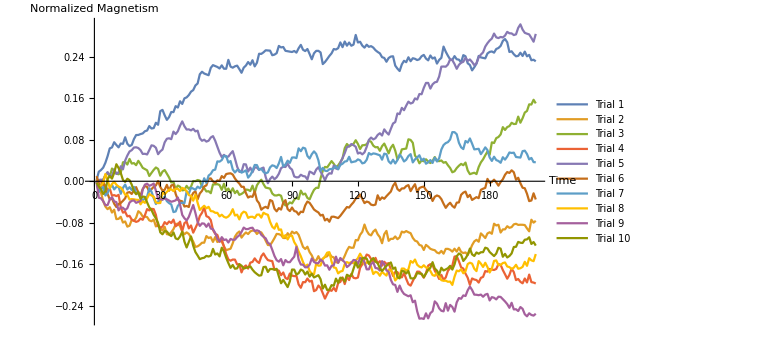

0.137493

```mathematica
magnetism1={110,734,864,1048,1422,1928,2532,2602,3004,2792,2610,2906,2880,3388,2888,2704,2794,3246,3556,3564,3632,3680,3850,3904,4248,4062,4094,4502,4346,5398,5494,5078,4726,4938,5330,5322,5782,5672,6158,5952,6384,6456,6634,6898,7016,7374,7526,8234,8430,8294,8228,8162,8732,8940,8868,8798,8682,8922,8664,8660,9346,8824,8744,8848,8900,8634,8350,8746,8908,9176,8970,9318,8842,9122,9816,9804,9924,10082,10068,10054,9702,9748,9862,10418,10302,10336,10042,10010,9978,9950,10028,9902,10238,10498,10124,10022,10180,9798,9390,9850,10036,10040,9916,9020,9180,9406,9646,9846,10178,10142,10246,10688,10322,10758,10436,10678,10432,10518,11264,10682,10738,10442,10286,10514,10350,10402,10290,10090,9954,9846,9552,9494,9200,9488,9600,9620,8902,8670,8486,8996,9274,9166,9544,9242,9470,9426,9328,9394,9624,9726,9446,9308,9682,9446,9534,9058,9342,9500,10368,9974,9658,9384,9342,9634,9392,9360,9144,9710,9620,9082,8950,8536,8776,9054,9646,9536,9496,9460,9836,9958,9992,9900,10182,10258,10420,10804,10950,10702,9950,10006,9778,9620,9650,9894,9644,9980,9616,9730,9316,9354,9234}/(200*200);
magnetism2={160,-444,-884,-1532,-1946,-2150,-1998,-2410,-2190,-2914,-2896,-2736,-3182,-3094,-3496,-3422,-2968,-3054,-2806,-2306,-2446,-2718,-2722,-2756,-3012,-3084,-2950,-3478,-3334,-3590,-3796,-3506,-4074,-4104,-3926,-3688,-3314,-3256,-3458,-3880,-4080,-3938,-4054,-4332,-4652,-5054,-5010,-4894,-4732,-4730,-4220,-4370,-4310,-4670,-4296,-4680,-4568,-4640,-5020,-5306,-5248,-5192,-4772,-4266,-4010,-3870,-4340,-4112,-3942,-4066,-3862,-3794,-3798,-4062,-3888,-3940,-4210,-4576,-4908,-4918,-4672,-4378,-4054,-4074,-4142,-4368,-4372,-3998,-4206,-3876,-4012,-3912,-4124,-4584,-5052,-5216,-5040,-5456,-5708,-6096,-6104,-5768,-6138,-5960,-5836,-5772,-5546,-5804,-5862,-6230,-6274,-5976,-6098,-5742,-5340,-5052,-5122,-5116,-4524,-4550,-4124,-3898,-3332,-3806,-4080,-4168,-3874,-3722,-4088,-4306,-4772,-4078,-3822,-4588,-4432,-4434,-4250,-4462,-4322,-3878,-3944,-3836,-3926,-3998,-4360,-4576,-4642,-4904,-4958,-5292,-4900,-5032,-5202,-5268,-5308,-5488,-5552,-5362,-5576,-5208,-5206,-5274,-5420,-5194,-5414,-5114,-5442,-5526,-5482,-5676,-5332,-4920,-4630,-4508,-4658,-4014,-4180,-4372,-4020,-3926,-4044,-3270,-3404,-3350,-3948,-3708,-3702,-3462,-3584,-3530,-3320,-3274,-3360,-3348,-3352,-3372,-3632,-3856,-2962,-3188,-3046}/40000;
magnetism3={0,-810,-344,140,418,674,348,978,826,588,536,656,1456,1494,1286,1718,1362,1396,1238,1572,1324,1032,938,844,402,644,874,1060,950,426,740,862,582,292,-90,-50,-608,-330,-428,-702,-672,-354,-592,-412,16,4,96,50,-406,-530,-786,-766,-920,-244,-240,-222,-294,-660,-192,-750,-560,-876,-542,-918,-734,-1050,-974,-854,-640,-660,-752,-340,-886,-316,-62,116,-220,-490,-526,-568,-946,-1088,-1094,-1042,-1114,-1668,-1862,-1804,-1626,-1706,-1426,-1264,-1374,-722,-1020,-950,-1284,-1398,-998,-664,-504,-512,230,804,1104,1066,1310,1552,1342,1086,1220,1474,1756,2546,2866,2680,2784,2872,3158,2872,2482,2768,2782,2846,3114,3044,2742,2614,2630,2342,2700,2900,2540,2148,2582,2810,2356,1686,1926,2454,2486,2516,3230,3180,2958,1978,1754,1382,1600,1536,1692,1518,1402,1562,1862,1566,1548,1600,1426,1480,1230,1020,690,768,1014,1194,1336,1234,1438,832,546,604,656,552,1094,1452,1686,2000,2288,2042,2994,2942,3320,3406,3604,4166,3950,4170,4246,4500,4404,4418,4976,4506,4854,5290,5410,5920,5906,6272,5994}/40000;
magnetism4={14,42,-10,-262,-314,-704,-566,-1108,-1068,-1142,-1050,-2004,-2416,-2350,-2704,-2662,-2954,-3040,-3128,-3066,-2870,-2968,-2614,-2142,-2246,-2124,-2148,-2588,-3460,-3576,-3490,-3150,-3306,-3098,-3216,-2954,-3466,-3344,-3110,-3842,-3224,-3106,-3630,-3404,-3958,-3602,-3236,-2680,-2428,-2008,-2690,-2766,-2992,-3750,-4050,-4132,-4656,-4494,-5028,-5610,-6018,-6118,-6030,-6034,-6402,-6392,-7018,-6614,-6484,-6726,-6270,-6210,-5938,-6164,-6290,-5784,-5558,-5848,-6070,-6118,-6150,-6812,-6826,-6886,-7236,-7024,-7448,-7532,-7104,-7266,-7306,-7288,-7942,-8202,-7764,-7774,-7490,-7724,-7658,-8464,-8374,-8030,-8214,-8616,-9036,-8678,-8374,-8436,-8208,-8462,-7834,-7748,-7404,-7916,-7350,-7606,-7128,-7434,-7474,-7410,-6666,-6390,-6022,-5644,-5716,-5984,-6286,-5898,-6320,-6156,-6498,-6200,-6368,-6300,-6796,-7294,-6986,-6998,-7278,-7402,-7072,-7520,-7922,-8036,-7682,-7350,-6956,-6964,-7168,-7424,-7074,-6494,-6384,-6446,-6890,-7166,-7524,-7208,-7594,-7408,-6894,-6690,-6498,-5802,-5764,-6162,-6626,-6722,-7110,-7428,-7976,-7484,-7566,-7606,-7800,-7438,-7364,-6916,-6958,-6754,-6804,-6830,-6752,-6376,-6434,-6838,-7162,-7502,-7210,-6730,-6994,-7612,-7524,-7742,-7858,-7488,-7792,-7186,-7764,-7800,-7872}/40000;
magnetism5={-168,94,124,72,482,698,454,362,910,562,684,1154,914,1592,1980,2290,2394,2594,2614,2556,2398,2104,2114,2062,2402,2764,2726,2578,2082,2302,2438,2994,3272,3308,3238,3822,3630,3850,4274,4610,4232,3982,3992,3916,4036,3840,3894,3316,3116,3198,3052,3122,3368,3474,3122,2654,2196,1862,2032,1878,1896,2124,2318,1752,1124,726,718,1312,1296,744,1050,690,1070,1052,864,980,1054,318,-152,172,358,156,304,576,1006,1122,1096,1356,1038,896,368,300,308,500,400,370,136,746,664,540,900,1080,740,436,80,452,616,588,1216,982,924,1416,1786,2164,2628,2686,2864,2778,2654,2132,2206,2070,2226,2646,3184,3362,3220,3314,3566,3696,3520,3994,3764,3594,4032,4446,4556,5222,5168,5650,5468,5820,6130,5984,6052,6378,6294,6716,6700,7188,7568,7570,7132,7460,7612,7658,8064,8822,8832,8818,8988,9386,9324,9028,8656,8962,9126,9194,9508,9264,9378,9184,8936,9084,9534,9752,9922,10368,10628,10836,10986,11370,11078,11022,11110,11068,11216,11500,11390,11382,11254,11310,11808,12080,11674,11426,11360,11304,11034,10742,11344}/40000;
magnetism6={390,-134,-434,44,-726,-972,-1402,-1312,-1730,-1986,-1752,-1670,-1506,-1314,-878,-834,-978,-688,-452,-878,-1088,-606,-360,-440,-792,-610,-426,-320,16,-438,-718,-660,-278,-734,-324,-264,-972,-1424,-1498,-1546,-1948,-1902,-1984,-1220,-904,-768,-1396,-942,-742,-400,-318,196,218,-8,-132,68,20,396,256,552,592,612,514,216,-4,-178,-428,-428,-914,-1256,-1164,-1200,-774,-1472,-1692,-2190,-2046,-1968,-2078,-1448,-1526,-2116,-2314,-2068,-2180,-1660,-1454,-2142,-2298,-2024,-2292,-2342,-2572,-2344,-2378,-1860,-1562,-1664,-1908,-2174,-2300,-2402,-2640,-2580,-3016,-2894,-3118,-2736,-2728,-2780,-2836,-2660,-2436,-2208,-1986,-2026,-1806,-1618,-1334,-1268,-1022,-1348,-1684,-1566,-1620,-1802,-1844,-1796,-1080,-1440,-1242,-1348,-1150,-970,-794,-350,-114,-598,-740,-554,-550,-374,-296,-760,-470,-228,-832,-522,-450,-412,-674,-836,-1088,-1520,-1194,-1096,-1164,-1372,-1730,-2048,-1814,-1654,-1900,-2034,-1648,-1628,-1046,-878,-796,-1224,-1052,-1440,-1330,-1224,-1304,-660,-576,-508,182,-116,-54,122,-82,-340,-56,154,500,708,638,842,692,120,268,-152,-502,-540,-962,-1530,-1482,-928,-1402}/40000;
magnetism7={-64,-812,-598,-440,-1098,-908,-526,-272,-630,-432,-424,-966,-506,-258,-640,-456,-680,-432,-910,-946,-1262,-1482,-1320,-1188,-538,-804,-1300,-1752,-1548,-1498,-1406,-1184,-1532,-1684,-1786,-2374,-2326,-1890,-1692,-1656,-1688,-782,-956,-500,-564,-662,-414,-540,-314,230,-124,436,570,848,896,1530,1508,1634,1950,1938,1438,1556,912,672,866,840,662,738,838,278,472,814,1254,1244,894,958,720,610,680,1070,1224,1176,1016,1374,1872,1138,1288,1584,1414,1824,1834,1780,2534,2312,2586,2524,1950,1746,2080,2302,2102,1618,806,1028,812,782,924,948,994,1160,930,1256,1350,1516,1550,1884,1456,1500,1536,1684,1612,1376,1426,1654,2170,2052,2142,2114,2056,1996,1660,2126,2078,1534,1366,1656,1370,1630,2060,1840,1522,1654,1942,2088,1450,1684,1832,2002,1602,1738,1348,1454,1634,1408,1818,1520,1768,2440,2786,2938,3012,3218,3782,3778,3620,2962,2612,2476,3100,2976,3296,2894,2454,2474,2498,2086,2328,2608,2398,1834,1564,1888,1630,1560,1422,1850,1662,1900,2216,2176,2200,1868,1844,1822,2316,2354,2098,1678,1796,1472,1464}/40000;
magnetism8={-76,-480,-322,-114,558,124,-536,-212,-42,-264,-416,-484,-710,-1038,-1038,-1410,-1370,-1390,-1426,-1436,-1776,-1538,-1666,-1310,-984,-1096,-1182,-1632,-1684,-1676,-834,-1006,-810,-656,-614,-760,-578,-576,-756,-510,-590,-766,-1070,-1122,-1496,-1028,-1656,-2208,-2044,-1886,-2088,-1968,-2298,-2318,-2428,-2434,-2706,-2578,-2740,-2806,-2710,-2512,-2150,-2640,-2572,-2938,-2502,-2342,-2412,-2820,-2742,-2732,-2836,-2576,-2562,-2800,-2424,-2526,-2582,-3126,-3508,-3652,-3246,-3742,-3710,-4322,-4148,-4480,-4182,-4192,-4686,-4954,-5410,-5772,-6220,-6576,-6416,-6902,-7114,-7168,-6346,-6506,-6482,-5992,-5800,-5496,-5460,-6186,-6634,-6680,-7094,-6952,-6906,-6378,-6224,-6302,-6226,-6322,-6100,-5922,-5574,-5874,-6420,-6230,-6298,-6584,-7142,-6972,-7032,-7278,-6970,-7128,-7262,-6798,-6832,-7086,-7638,-7438,-7258,-6722,-6724,-6878,-6782,-6140,-6274,-6026,-6430,-6576,-6636,-6466,-6644,-6664,-6910,-7224,-7284,-7018,-7314,-7618,-7664,-7654,-7738,-7724,-7982,-7350,-6878,-6930,-6776,-7084,-6926,-6374,-6272,-6342,-6738,-6918,-6146,-6344,-6598,-6276,-6608,-7024,-6716,-6134,-6096,-6454,-6446,-6298,-6254,-6562,-6610,-6756,-6652,-6432,-6736,-6696,-6592,-6200,-6512,-5924,-6090,-6152,-5604}/40000;
magnetism9={-38,-1268,-1314,-1530,-1840,-1836,-1406,-1228,-1546,-1610,-2244,-2012,-2042,-2216,-2078,-1638,-1504,-1476,-1662,-1586,-1528,-628,-260,-190,-352,-286,-178,-722,-1352,-1392,-1414,-1332,-1394,-1486,-1580,-1532,-1472,-1250,-1802,-2592,-2848,-3018,-2740,-2276,-1828,-2442,-3126,-3438,-3244,-3264,-3508,-3256,-3644,-3690,-3980,-4420,-4640,-4304,-4522,-4480,-4716,-4442,-4508,-4502,-4294,-4158,-3898,-3566,-3686,-3678,-3604,-3578,-3846,-3776,-3842,-4122,-4276,-4396,-4744,-4838,-5282,-5752,-6080,-6192,-5990,-6472,-6066,-6230,-6230,-6004,-5806,-5048,-6028,-6412,-6422,-6628,-6620,-6422,-5944,-6208,-6312,-6306,-6042,-6160,-6494,-6472,-6814,-6512,-6468,-5804,-6278,-5908,-6078,-6234,-6608,-6470,-6288,-6060,-6090,-6378,-5898,-6026,-6238,-6782,-6780,-6360,-6250,-6680,-6706,-6874,-6150,-6378,-6862,-6970,-7598,-7938,-7984,-8518,-8030,-8440,-8676,-8768,-8856,-8778,-9314,-9194,-10018,-10580,-10556,-10600,-10168,-10556,-10152,-10008,-9248,-9422,-9784,-9972,-10016,-9386,-9964,-9522,-9678,-10040,-9322,-8992,-9048,-8788,-8834,-8398,-8108,-8372,-8728,-8740,-8772,-8726,-8892,-8728,-8670,-9178,-8922,-8970,-9096,-8888,-8906,-9080,-9254,-9456,-9744,-9356,-9866,-9854,-9992,-9684,-9822,-10240,-10400,-10164,-10294,-10344,-10200}/40000;
magnetism10={-108,-388,-612,-984,-766,164,406,200,642,1310,1018,640,100,-52,192,80,-266,-778,-1002,-810,-1350,-1180,-1204,-1628,-2014,-2214,-2582,-2852,-3216,-3932,-4084,-3836,-3870,-4094,-4224,-3938,-4400,-4468,-4252,-3884,-4650,-5098,-4676,-4250,-4962,-5452,-5716,-5998,-5924,-5888,-5746,-5798,-5726,-5208,-5642,-5556,-5786,-5116,-5408,-5888,-6298,-6664,-6448,-6734,-6708,-6386,-6498,-6728,-6664,-6626,-6554,-6806,-7002,-7142,-7268,-7236,-6604,-6584,-6984,-6756,-6760,-6810,-6742,-7324,-7854,-7596,-7874,-8148,-7702,-6796,-6806,-7188,-7078,-6798,-6884,-7180,-6954,-7340,-7120,-7406,-7322,-7232,-7544,-8264,-7964,-8374,-8346,-7998,-8046,-7496,-7822,-7422,-7472,-7722,-7198,-7298,-7274,-6736,-6234,-6648,-6442,-5932,-5888,-5960,-6360,-6082,-5914,-6188,-6300,-6700,-6908,-6706,-6512,-6376,-6252,-6744,-6642,-7384,-7480,-6896,-6932,-7104,-6906,-7466,-7490,-7424,-7054,-7106,-7120,-7388,-7094,-6824,-6660,-6230,-6716,-6880,-7188,-6658,-6870,-6788,-6696,-6512,-6800,-6398,-5776,-5560,-5666,-6138,-5936,-5654,-5182,-5630,-5754,-5482,-5582,-5466,-5460,-5114,-5176,-5448,-5604,-5760,-5564,-5126,-5188,-5812,-5592,-5868,-5754,-5558,-5062,-5044,-4670,-4734,-4752,-4500,-4476,-4314,-4828,-4680,-4954}/40000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetization2Dn200kT225=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

### All Data for 2D

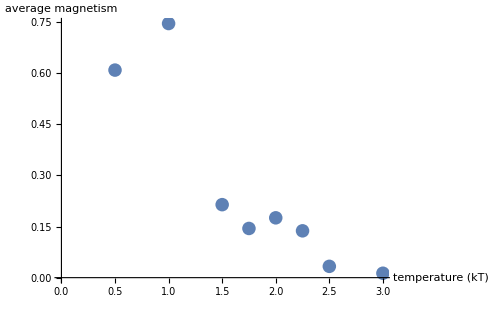

```mathematica
ListPlot[{{0.5,averageMagnetization2Dn200kT05},{1,averageMagnetization2Dn200kT1},{1.5,averageMagnetization2Dn200kT15},{2,averageMagnetization2Dn200kT2},{1.75,averageMagnetization2Dn200kT175},{2.25,averageMagnetization2Dn200kT225},{2.5,averageMagnetization2Dn200kT25},{3,averageMagnetization2Dn200kT3}},AxesLabel->{"temperature (kT)","average magnetism"},ImageSize->500]
```

## 2 D Hexagonal Lattice

### 100x100, kT=0.5, 100 time steps

Initially, I went for 200 time steps, but these stabilized very quickly.

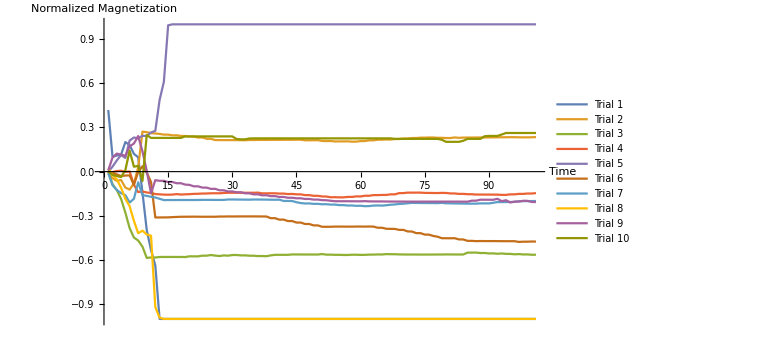

0.50883

```mathematica
magnetism1={4182,1004,1096,1152,2008,1800,1208,972,-1414,-3972,-5326,-6370,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000}/10000;magnetism2={-138,-442,-632,-570,-1084,-1218,-796,286,2716,2680,2612,2590,2560,2512,2512,2466,2466,2422,2420,2378,2378,2316,2320,2232,2228,2144,2142,2140,2140,2140,2140,2136,2132,2148,2146,2154,2156,2154,2158,2160,2158,2162,2164,2164,2168,2168,2126,2128,2130,2134,2084,2074,2078,2050,2052,2054,2056,2036,2038,2074,2076,2124,2124,2168,2168,2184,2176,2214,2214,2248,2248,2280,2282,2306,2308,2318,2316,2296,2296,2280,2282,2320,2294,2312,2312,2314,2316,2318,2320,2322,2326,2330,2334,2334,2338,2338,2330,2328,2328,2332,2346}/10000;
magnetism3={12,-856,-1252,-1854,-2782,-3836,-4474,-4678,-5094,-5856,-5830,-5828,-5796,-5792,-5792,-5792,-5794,-5794,-5798,-5748,-5752,-5752,-5706,-5706,-5662,-5700,-5730,-5688,-5706,-5662,-5660,-5686,-5684,-5708,-5708,-5732,-5730,-5742,-5684,-5648,-5648,-5650,-5648,-5622,-5622,-5624,-5626,-5626,-5628,-5628,-5596,-5636,-5636,-5648,-5648,-5658,-5658,-5640,-5642,-5652,-5650,-5634,-5632,-5622,-5624,-5600,-5606,-5608,-5620,-5624,-5628,-5626,-5628,-5630,-5630,-5630,-5628,-5626,-5626,-5620,-5622,-5624,-5626,-5626,-5500,-5498,-5494,-5526,-5524,-5554,-5550,-5576,-5556,-5582,-5584,-5614,-5598,-5622,-5620,-5642,-5642}/10000;
magnetism4={-50,-30,40,62,-16,10,-890,-1390,-1344,-1416,-1448,-1522,-1542,-1560,-1566,-1558,-1524,-1556,-1540,-1528,-1510,-1502,-1488,-1484,-1470,-1468,-1470,-1446,-1436,-1434,-1436,-1434,-1434,-1434,-1434,-1426,-1474,-1474,-1470,-1470,-1492,-1490,-1522,-1514,-1542,-1542,-1594,-1594,-1642,-1642,-1684,-1692,-1738,-1736,-1746,-1746,-1716,-1716,-1680,-1684,-1638,-1638,-1594,-1594,-1582,-1582,-1542,-1542,-1460,-1456,-1426,-1426,-1424,-1424,-1444,-1446,-1450,-1454,-1444,-1448,-1480,-1482,-1510,-1510,-1532,-1534,-1556,-1556,-1558,-1558,-1560,-1562,-1578,-1578,-1542,-1542,-1510,-1512,-1486,-1488,-1458}/10000;
magnetism5={-12,338,762,1126,932,2114,2316,2264,2432,2422,2660,2766,4860,6094,9936,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000}/10000;
magnetism6={-90,-96,-186,-304,-264,-256,-900,-14,360,-72,-702,-3110,-3110,-3108,-3104,-3088,-3076,-3064,-3062,-3060,-3056,-3060,-3064,-3062,-3062,-3064,-3048,-3050,-3042,-3044,-3042,-3040,-3040,-3038,-3040,-3040,-3044,-3048,-3160,-3160,-3258,-3256,-3356,-3354,-3458,-3456,-3554,-3554,-3650,-3650,-3744,-3744,-3744,-3730,-3732,-3732,-3734,-3734,-3728,-3728,-3732,-3726,-3732,-3808,-3810,-3878,-3886,-3888,-3954,-3954,-4060,-4066,-4174,-4176,-4274,-4278,-4368,-4418,-4520,-4522,-4524,-4520,-4602,-4604,-4700,-4700,-4718,-4712,-4714,-4716,-4714,-4718,-4720,-4722,-4722,-4722,-4772,-4756,-4756,-4744,-4748}/10000;
magnetism7={-106,-920,-1250,-1460,-1596,-2098,-1842,-720,-1594,-1648,-1708,-1754,-1844,-1932,-1928,-1928,-1928,-1926,-1926,-1926,-1926,-1924,-1916,-1916,-1918,-1920,-1922,-1920,-1890,-1890,-1894,-1898,-1900,-1904,-1892,-1894,-1896,-1900,-1906,-1910,-1904,-1990,-1992,-1994,-2078,-2132,-2162,-2158,-2188,-2186,-2214,-2212,-2238,-2236,-2274,-2272,-2302,-2296,-2324,-2316,-2346,-2338,-2302,-2296,-2306,-2282,-2248,-2228,-2194,-2178,-2148,-2120,-2124,-2130,-2132,-2134,-2136,-2142,-2120,-2150,-2152,-2160,-2162,-2168,-2172,-2174,-2174,-2156,-2156,-2158,-2114,-2068,-2068,-2064,-2060,-2058,-2008,-2004,-2002,-1998,-1994}/10000;
magnetism8={212,-204,-530,-1092,-1846,-2350,-3342,-4182,-4008,-4266,-4348,-9192,-9916,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000}/10000;
magnetism9={76,962,1224,1158,1078,1710,1910,2416,1378,52,-1474,-578,-624,-624,-708,-704,-788,-786,-882,-900,-998,-996,-1084,-1086,-1170,-1168,-1266,-1266,-1344,-1342,-1400,-1398,-1472,-1472,-1544,-1540,-1610,-1602,-1664,-1662,-1720,-1718,-1774,-1772,-1810,-1808,-1856,-1854,-1898,-1896,-1936,-1942,-1978,-2008,-2010,-2010,-2010,-2012,-2014,-2014,-2004,-2020,-2022,-2024,-2022,-2028,-2030,-2032,-2034,-2034,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2036,-2038,-2040,-1972,-1972,-1906,-1908,-1908,-1912,-1846,-2006,-1940,-2094,-2032,-2034,-1978,-1982,-2062,-2064}/10000;
magnetism10={32,-224,-298,-368,104,1426,334,390,-632,2488,2290,2290,2290,2290,2290,2290,2290,2290,2392,2392,2392,2392,2392,2392,2392,2392,2392,2392,2392,2392,2214,2192,2192,2250,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2258,2224,2224,2224,2224,2224,2224,2224,2224,2224,2224,2224,2162,2024,2024,2024,2024,2096,2224,2224,2224,2224,2404,2424,2424,2424,2520,2624,2624,2624,2624,2624,2624,2624,2624}/10000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetizationHexN200T05=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

```mathematica
data2=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData2={};
For[kk=1,kk⩽Dimensions[data2]⟦2⟧,kk++,
AppendTo[fullData2,Transpose[data2⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData2⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data2]⟦2⟧,1}]
```

### 100x100, kT=2, 200 time steps

I raised the time interval since these take longer to settle down.

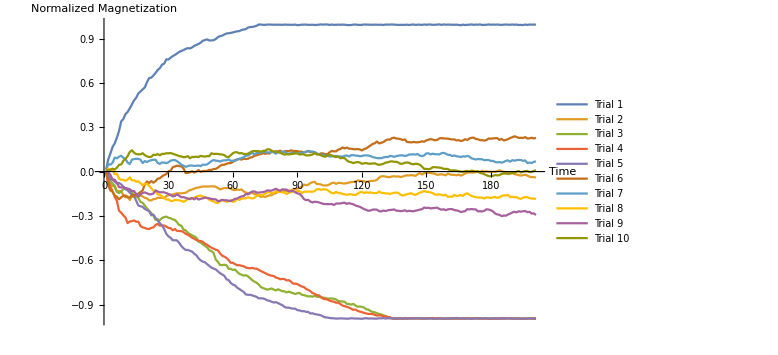

0.4709

```mathematica
magnetism1={150,830,1228,1664,1914,2298,2744,3394,3556,3892,4036,4284,4544,4822,5006,5292,5432,5568,5700,6050,6332,6362,6506,6678,6884,7000,7236,7310,7598,7588,7712,7818,7898,7994,8106,8166,8224,8308,8358,8338,8406,8516,8576,8642,8732,8856,8908,8950,8878,8882,8894,8976,9102,9168,9206,9284,9348,9368,9390,9424,9464,9498,9514,9586,9618,9648,9750,9788,9794,9826,9872,9958,9956,9938,9934,9954,9956,9952,9942,9944,9946,9942,9936,9954,9944,9944,9936,9940,9952,9914,9926,9946,9952,9954,9934,9938,9942,9924,9934,9946,9964,9948,9962,9960,9930,9956,9936,9938,9950,9940,9952,9942,9926,9918,9924,9950,9958,9936,9932,9930,9960,9950,9950,9944,9942,9948,9944,9940,9944,9926,9954,9952,9954,9962,9950,9938,9930,9940,9932,9936,9948,9928,9946,9960,9930,9950,9946,9930,9962,9938,9958,9956,9934,9942,9950,9970,9932,9964,9946,9952,9950,9942,9938,9948,9932,9906,9950,9924,9940,9944,9964,9938,9950,9948,9962,9928,9934,9942,9964,9942,9954,9944,9956,9944,9926,9952,9954,9946,9942,9958,9944,9954,9924,9932,9922,9956,9928,9956,9948,9954,9944}/10000;magnetism2={34,-308,-806,-996,-930,-1352,-1310,-1334,-1594,-1738,-1684,-1920,-1680,-1728,-1660,-1684,-1628,-1686,-1780,-1808,-1942,-1950,-1864,-1854,-1774,-1780,-1764,-1804,-1656,-1596,-1560,-1554,-1504,-1472,-1476,-1474,-1450,-1434,-1338,-1252,-1214,-1154,-1098,-1084,-1032,-1012,-1010,-1008,-1004,-1000,-998,-1026,-1114,-1206,-1156,-1116,-1120,-1110,-1148,-1238,-1252,-1216,-1240,-1206,-1342,-1420,-1472,-1484,-1418,-1534,-1530,-1632,-1716,-1678,-1722,-1658,-1606,-1604,-1498,-1462,-1354,-1306,-1342,-1310,-1326,-1290,-1266,-1200,-1160,-1152,-1086,-1046,-878,-924,-896,-778,-722,-698,-836,-848,-872,-936,-938,-928,-870,-774,-750,-832,-764,-770,-794,-804,-782,-750,-708,-706,-680,-600,-622,-642,-654,-704,-682,-634,-626,-614,-564,-406,-322,-310,-338,-370,-378,-328,-318,-336,-322,-370,-336,-278,-250,-264,-238,-262,-290,-172,-96,-198,-112,-84,-92,-88,-126,-148,-222,-200,-182,-210,-256,-136,-194,-220,-220,-248,-206,-270,-220,-128,-68,-56,-66,-62,-30,0,-20,48,-18,20,-16,-8,-18,-20,30,84,26,-18,-32,-56,-88,-84,-174,-198,-240,-270,-244,-210,-272,-344,-374,-376,-402}/10000;
magnetism3={-152,-360,-650,-796,-1034,-1372,-1452,-1354,-1178,-1122,-1178,-1278,-1362,-1610,-1670,-1792,-2058,-2114,-2306,-2490,-2660,-2814,-2984,-3278,-3232,-3288,-3146,-3076,-3048,-3122,-3160,-3232,-3278,-3430,-3626,-3656,-3930,-3972,-4148,-4228,-4316,-4386,-4476,-4746,-4800,-4930,-5028,-5136,-5322,-5384,-5504,-5954,-6108,-6326,-6332,-6304,-6340,-6586,-6582,-6664,-6632,-6792,-6922,-6980,-7042,-7012,-7088,-7222,-7358,-7448,-7526,-7648,-7816,-7886,-7938,-7998,-7952,-7916,-7990,-8046,-7968,-8034,-8096,-8112,-8178,-8128,-8182,-8232,-8292,-8236,-8218,-8332,-8362,-8404,-8452,-8438,-8472,-8408,-8474,-8476,-8524,-8528,-8556,-8604,-8594,-8590,-8614,-8660,-8764,-8790,-8796,-8814,-8956,-8966,-9006,-8954,-9064,-9148,-9132,-9162,-9202,-9318,-9348,-9446,-9498,-9526,-9592,-9640,-9670,-9734,-9774,-9830,-9886,-9932,-9964,-9960,-9948,-9946,-9960,-9938,-9948,-9948,-9940,-9934,-9948,-9934,-9956,-9932,-9950,-9956,-9936,-9932,-9946,-9956,-9964,-9950,-9950,-9944,-9954,-9938,-9960,-9934,-9950,-9954,-9942,-9942,-9928,-9974,-9932,-9948,-9930,-9952,-9938,-9942,-9926,-9958,-9958,-9948,-9944,-9958,-9950,-9948,-9946,-9940,-9936,-9948,-9936,-9942,-9950,-9936,-9962,-9950,-9942,-9936,-9950,-9954,-9956,-9946,-9950,-9960,-9960}/10000;
magnetism4={-96,-642,-1028,-1332,-1702,-1986,-2648,-2782,-2960,-3112,-3486,-3378,-3356,-3312,-3390,-3392,-3692,-3772,-3822,-3870,-3888,-3814,-3776,-3616,-3540,-3664,-3638,-3652,-3726,-3814,-3832,-3974,-3886,-4014,-4026,-4028,-4094,-4214,-4276,-4360,-4482,-4538,-4634,-4690,-4700,-4758,-4892,-4954,-5064,-5152,-5220,-5286,-5332,-5538,-5692,-5762,-5846,-5992,-6174,-6174,-6270,-6340,-6338,-6376,-6406,-6492,-6526,-6550,-6516,-6570,-6574,-6654,-6736,-6804,-6870,-6950,-7010,-7050,-7070,-7180,-7214,-7288,-7266,-7276,-7372,-7348,-7452,-7582,-7590,-7616,-7704,-7782,-7812,-7948,-8006,-8094,-8222,-8270,-8364,-8376,-8494,-8606,-8640,-8662,-8738,-8780,-8808,-8880,-8872,-8970,-9070,-9112,-9156,-9210,-9282,-9358,-9340,-9428,-9478,-9514,-9566,-9606,-9636,-9638,-9646,-9700,-9750,-9734,-9744,-9808,-9802,-9862,-9852,-9944,-9938,-9964,-9952,-9952,-9952,-9940,-9948,-9944,-9946,-9912,-9946,-9942,-9940,-9952,-9946,-9936,-9940,-9938,-9910,-9946,-9932,-9936,-9944,-9962,-9956,-9942,-9950,-9940,-9942,-9950,-9954,-9960,-9954,-9934,-9946,-9934,-9952,-9936,-9924,-9942,-9948,-9952,-9950,-9948,-9970,-9954,-9970,-9956,-9960,-9956,-9954,-9930,-9946,-9934,-9946,-9956,-9942,-9960,-9948,-9954,-9966,-9946,-9948,-9952,-9948,-9922,-9940}/10000;
magnetism5={-48,-228,-528,-536,-686,-792,-770,-864,-1020,-1190,-1272,-1418,-1566,-1636,-1980,-2300,-2346,-2390,-2534,-2602,-2678,-2958,-2914,-3140,-3310,-3490,-3658,-3882,-4212,-4386,-4484,-4652,-4650,-4658,-4832,-5042,-5194,-5306,-5304,-5362,-5414,-5562,-5672,-5872,-6010,-6098,-6140,-6270,-6386,-6504,-6566,-6622,-6752,-6880,-6966,-7054,-7294,-7350,-7542,-7654,-7712,-7862,-7950,-8054,-8148,-8316,-8346,-8340,-8382,-8434,-8480,-8582,-8578,-8590,-8638,-8718,-8746,-8810,-8864,-8838,-8906,-8982,-9042,-9166,-9210,-9210,-9254,-9280,-9282,-9382,-9398,-9454,-9448,-9496,-9498,-9606,-9592,-9644,-9672,-9700,-9736,-9812,-9874,-9882,-9916,-9926,-9938,-9952,-9950,-9936,-9946,-9948,-9962,-9954,-9930,-9940,-9952,-9950,-9954,-9968,-9944,-9924,-9952,-9944,-9946,-9954,-9958,-9928,-9940,-9920,-9952,-9930,-9940,-9940,-9946,-9942,-9938,-9930,-9950,-9942,-9940,-9938,-9944,-9956,-9930,-9934,-9930,-9940,-9946,-9950,-9944,-9936,-9968,-9950,-9950,-9944,-9950,-9946,-9954,-9954,-9944,-9940,-9946,-9912,-9934,-9938,-9940,-9946,-9942,-9952,-9976,-9948,-9940,-9952,-9936,-9942,-9928,-9928,-9958,-9938,-9942,-9930,-9946,-9946,-9924,-9964,-9938,-9936,-9936,-9960,-9944,-9942,-9942,-9966,-9954,-9946,-9956,-9926,-9940,-9968,-9962}/10000;
magnetism6={62,-948,-1278,-1358,-1616,-1706,-1876,-1746,-1646,-1618,-1754,-1756,-1582,-1616,-1582,-1480,-1384,-1268,-864,-666,-776,-642,-752,-642,-480,-454,-326,-234,-176,22,58,302,346,404,366,358,218,-98,-82,-46,22,-60,2,102,-10,40,40,54,120,110,176,182,270,382,464,462,526,574,574,656,784,812,848,812,872,854,868,950,974,1076,1098,1160,1184,1242,1208,1234,1220,1336,1346,1364,1368,1418,1314,1374,1392,1376,1438,1394,1394,1382,1346,1350,1288,1344,1406,1314,1340,1278,1196,1168,1236,1226,1182,1180,1312,1400,1368,1372,1490,1526,1634,1566,1626,1552,1546,1524,1508,1528,1500,1434,1524,1572,1670,1764,1874,1914,2036,1906,1950,1996,2110,2172,2166,2266,2298,2236,2228,2200,2140,2176,2004,1992,1974,2010,1984,1982,2006,2050,2024,2116,2160,2200,2164,2126,2142,2246,2266,2248,2238,2230,2202,2176,2184,2110,2132,2072,2100,2194,2140,2240,2288,2294,2212,2188,2126,2126,2100,2140,2246,2224,2250,2256,2266,2146,2212,2106,2144,2190,2272,2330,2390,2346,2280,2292,2274,2332,2240,2252,2292,2244,2282}/10000;
magnetism7={116,500,470,602,948,900,1006,1070,936,846,612,506,812,842,866,862,806,580,712,652,722,774,800,804,586,520,622,604,576,630,740,776,778,702,592,464,400,322,374,412,408,384,394,414,368,476,458,488,592,710,786,736,730,676,746,760,766,822,724,740,714,822,874,912,972,1084,1086,1182,1286,1152,1266,1256,1298,1330,1332,1304,1288,1342,1302,1206,1348,1282,1338,1348,1240,1194,1248,1268,1244,1240,1260,1266,1324,1322,1382,1374,1350,1326,1242,1162,1144,1154,1044,1090,1022,1032,1058,1060,1028,1026,1004,1074,1086,1026,1106,1114,1082,1078,1044,1052,1096,1096,1090,1050,986,952,916,904,910,956,990,982,1056,1048,1002,1044,1080,1098,1096,1058,1086,1154,1162,1170,1150,1192,1074,1052,1098,1230,1236,1164,1212,1174,1176,1160,1242,1268,1218,1134,1130,1050,1094,1038,1022,984,1038,1016,1058,1022,896,860,820,852,840,834,768,784,782,720,724,648,624,644,604,650,730,760,672,774,736,774,788,782,726,756,574,612,578,660,694}/10000;
magnetism8={46,194,152,166,-180,-152,-476,-554,-558,-624,-536,-386,-596,-580,-690,-654,-788,-930,-838,-830,-960,-1126,-1294,-1318,-1544,-1574,-1682,-1786,-1892,-1888,-1988,-1992,-1906,-1930,-1946,-1982,-2050,-1968,-1866,-1798,-1818,-1752,-1694,-1658,-1622,-1688,-1734,-1782,-1898,-1982,-2018,-2108,-2122,-1998,-1950,-1972,-2048,-2014,-1932,-2050,-2002,-1844,-1918,-1828,-1818,-1806,-1744,-1776,-1824,-1776,-1658,-1572,-1608,-1580,-1504,-1410,-1382,-1484,-1438,-1334,-1372,-1380,-1410,-1424,-1522,-1430,-1402,-1324,-1356,-1304,-1324,-1458,-1368,-1358,-1356,-1358,-1366,-1320,-1194,-1186,-1238,-1196,-1198,-1252,-1354,-1460,-1466,-1372,-1454,-1446,-1518,-1542,-1568,-1544,-1532,-1578,-1590,-1496,-1406,-1372,-1456,-1396,-1434,-1406,-1452,-1452,-1458,-1344,-1438,-1450,-1482,-1478,-1516,-1474,-1432,-1420,-1444,-1570,-1620,-1582,-1528,-1496,-1464,-1548,-1576,-1500,-1420,-1382,-1306,-1372,-1372,-1410,-1454,-1558,-1562,-1534,-1574,-1614,-1568,-1710,-1692,-1704,-1578,-1648,-1638,-1586,-1654,-1518,-1470,-1564,-1646,-1700,-1724,-1760,-1748,-1772,-1824,-1744,-1756,-1786,-1744,-1716,-1774,-1736,-1648,-1612,-1616,-1578,-1736,-1700,-1736,-1736,-1810,-1844,-1762,-1732,-1726,-1796,-1824,-1834,-1850}/10000;
magnetism9={56,-44,-224,-542,-550,-756,-1048,-1078,-1054,-1116,-1160,-1188,-1322,-1318,-1528,-1680,-1536,-1444,-1408,-1468,-1536,-1538,-1480,-1274,-1348,-1402,-1394,-1406,-1454,-1516,-1594,-1678,-1648,-1552,-1640,-1734,-1734,-1776,-1828,-1868,-1788,-1880,-1780,-1890,-1846,-1810,-1758,-1784,-1812,-1854,-1872,-1880,-2000,-1974,-1910,-1946,-1940,-1974,-1988,-1928,-1838,-1828,-1734,-1680,-1658,-1520,-1546,-1428,-1352,-1342,-1414,-1428,-1402,-1390,-1350,-1272,-1290,-1290,-1222,-1168,-1244,-1298,-1200,-1218,-1220,-1340,-1326,-1312,-1402,-1470,-1516,-1648,-1854,-1932,-1912,-2022,-2090,-2044,-2054,-2084,-2136,-2186,-2198,-2202,-2202,-2196,-2262,-2162,-2160,-2160,-2124,-2104,-2190,-2130,-2180,-2210,-2292,-2342,-2378,-2458,-2536,-2592,-2652,-2634,-2576,-2568,-2578,-2680,-2696,-2638,-2672,-2624,-2596,-2592,-2558,-2644,-2654,-2682,-2662,-2618,-2694,-2652,-2678,-2686,-2646,-2620,-2572,-2542,-2432,-2466,-2446,-2496,-2468,-2462,-2438,-2526,-2580,-2548,-2612,-2556,-2538,-2540,-2606,-2626,-2660,-2738,-2708,-2680,-2544,-2558,-2536,-2554,-2562,-2690,-2688,-2698,-2656,-2548,-2574,-2614,-2698,-2840,-2900,-2924,-3014,-2976,-2984,-2908,-2844,-2770,-2718,-2758,-2688,-2716,-2684,-2674,-2748,-2728,-2842,-2832,-2940}/10000;
magnetism10={136,68,112,198,140,262,460,482,732,864,1042,1328,1446,1276,1188,1170,1166,1246,1108,1032,986,1000,1144,1118,1188,1104,1198,1196,1242,1238,1256,1206,1160,1108,1042,1024,976,984,1052,902,990,992,1006,988,1064,1030,1014,1048,1044,1240,1194,1202,1196,1164,1162,1110,1000,984,1110,1246,1310,1308,1232,1260,1190,1186,1212,1300,1376,1394,1386,1384,1342,1404,1414,1506,1508,1418,1344,1354,1318,1270,1206,1148,1178,1164,1182,1200,1240,1234,1158,1176,1166,1096,1094,1114,1156,1246,1162,1178,1102,1036,1012,1078,1142,1092,1016,984,1022,902,924,910,762,662,642,572,620,646,612,528,558,582,534,536,546,562,496,456,490,524,608,630,676,696,660,664,614,526,538,598,614,598,520,496,534,512,462,338,176,184,158,198,300,298,284,270,248,190,182,174,88,78,88,56,30,-6,-10,24,48,14,62,40,10,20,-92,-122,-184,-244,-306,-314,-288,-232,-258,-234,-166,-130,-134,-150,-142,-94,-70,-4,36,-58,-4,32,44,-40,-16,38,100}/10000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetizationHexN200T05=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data3=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData3={};
For[kk=1,kk⩽Dimensions[data3]⟦2⟧,kk++,
AppendTo[fullData3,Transpose[data3⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData3⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data3]⟦2⟧,1}]
```

### 100x100, kT=3, 200 time steps

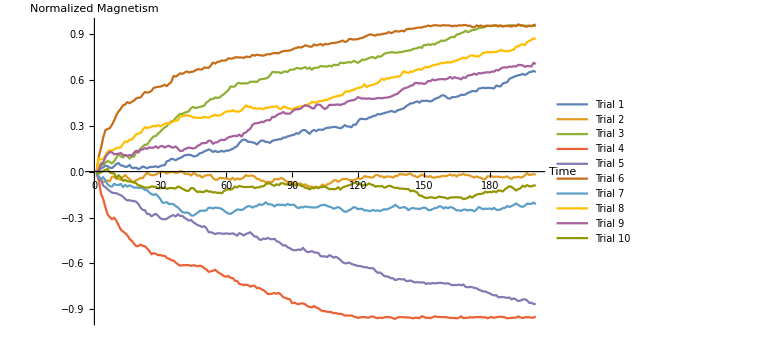

0.548143

```mathematica
magnetism1={140,36,222,276,392,352,260,232,346,506,556,400,386,312,320,440,248,230,266,162,224,332,282,220,294,306,312,348,284,360,408,420,678,716,842,806,746,828,896,952,1068,1080,1104,1080,996,1008,1062,1204,1228,1316,1372,1458,1392,1286,1356,1282,1306,1358,1302,1372,1368,1432,1488,1588,1664,1876,2020,2104,2060,1946,1948,1906,1874,1768,1920,2032,2016,1944,1930,1880,2012,2050,2074,2118,2116,2222,2226,2302,2332,2386,2412,2516,2472,2622,2710,2716,2590,2466,2636,2724,2642,2740,2744,2722,2818,2860,2872,2894,2928,2908,2870,2826,2900,3042,2954,2944,2896,3070,3056,3276,3446,3446,3432,3428,3528,3556,3634,3658,3760,3740,3780,3822,3868,3902,3966,3926,3886,4004,4044,4090,4144,4280,4364,4462,4464,4538,4588,4506,4622,4624,4632,4616,4582,4646,4750,4804,4856,4966,4994,4906,4782,4776,4868,4866,4890,4940,5018,5010,5044,5146,5188,5262,5262,5244,5426,5446,5484,5456,5474,5474,5452,5436,5628,5576,5572,5758,5806,5844,6066,6116,6194,6242,6294,6314,6386,6316,6382,6496,6516,6582,6500}/10000;magnetism2={160,-594,-478,-674,-628,-582,-628,-334,-338,-462,-464,-534,-352,-212,-384,-482,-674,-722,-558,-512,-404,-442,-232,-82,-174,-230,-232,-186,-108,-6,-10,-46,-128,-42,-32,-16,-96,-60,10,18,-132,-158,-140,-260,-100,-150,-276,-242,-388,-296,-232,-234,-220,-426,-524,-530,-410,-420,-432,-450,-478,-536,-398,-544,-436,-502,-470,-372,-228,-292,-260,-254,-328,-476,-494,-606,-588,-716,-660,-688,-680,-484,-492,-502,-410,-480,-598,-666,-758,-654,-754,-804,-798,-772,-896,-832,-924,-984,-972,-1028,-1044,-1092,-970,-840,-952,-836,-786,-708,-572,-558,-666,-578,-482,-484,-474,-562,-538,-562,-508,-420,-490,-432,-292,-334,-342,-394,-368,-228,-218,-312,-310,-396,-312,-328,-328,-390,-288,-276,-158,-184,-186,-216,-154,-126,-256,-280,-370,-302,-196,-252,-310,-346,-288,-392,-394,-338,-352,-306,-272,-304,-248,-186,-266,-210,-318,-198,-216,-138,-230,-210,-266,-326,-388,-310,-380,-394,-490,-492,-308,-314,-308,-348,-322,-348,-336,-386,-348,-312,-412,-472,-370,-368,-330,-386,-356,-254,-90,-224,-196,-168,-188}/10000;
magnetism3={-10,258,566,450,584,694,632,536,678,920,1138,1010,916,1088,1024,852,990,966,1248,1346,1502,1636,1756,1766,1972,2148,2304,2328,2486,2606,2768,2886,2974,3166,3284,3320,3506,3642,3772,3762,3848,3888,3942,4146,4228,4144,4194,4222,4260,4306,4516,4610,4740,4740,4848,4816,4840,4970,5060,5200,5318,5556,5550,5562,5758,5804,5744,5776,5760,5776,5872,5868,5876,5856,5998,6046,6052,6088,6140,6288,6506,6502,6488,6490,6432,6516,6542,6514,6642,6666,6676,6766,6760,6716,6762,6830,6718,6804,6650,6782,6772,6808,6898,6882,6868,6868,6918,6866,6986,6964,6966,7120,7096,7094,7126,7158,7124,7234,7184,7104,7202,7322,7292,7350,7410,7472,7476,7390,7534,7506,7568,7692,7758,7762,7802,7792,7772,7774,7810,7804,7860,7880,7914,7922,8004,8036,8060,8140,8080,8264,8268,8322,8274,8336,8304,8418,8450,8570,8532,8584,8660,8748,8812,8784,8960,8978,9050,9100,9202,9110,9162,9250,9250,9296,9378,9392,9420,9452,9536,9502,9544,9526,9522,9534,9528,9464,9518,9534,9562,9560,9546,9534,9574,9546,9520,9544,9522,9538,9504,9520,9504}/10000;
magnetism4={-148,-570,-1454,-1784,-2330,-2796,-2976,-3112,-3004,-3214,-3498,-3786,-3910,-4018,-4154,-4396,-4526,-4692,-4868,-4858,-4762,-4854,-4876,-5028,-5176,-5400,-5328,-5368,-5456,-5452,-5494,-5502,-5644,-5692,-5782,-5808,-5936,-6052,-6144,-6116,-6108,-6102,-6116,-6154,-6120,-6136,-6182,-6142,-6190,-6302,-6390,-6544,-6518,-6474,-6406,-6548,-6632,-6718,-6828,-6866,-6816,-6942,-6954,-7130,-7142,-7340,-7364,-7420,-7386,-7414,-7514,-7452,-7466,-7612,-7590,-7692,-7736,-7864,-8002,-7990,-7974,-7932,-7974,-7924,-8040,-8206,-8248,-8314,-8336,-8596,-8554,-8630,-8666,-8610,-8612,-8666,-8794,-8832,-8872,-8778,-8878,-8928,-9048,-9118,-9112,-9156,-9164,-9182,-9258,-9228,-9296,-9284,-9328,-9406,-9396,-9406,-9398,-9458,-9500,-9562,-9510,-9512,-9500,-9534,-9538,-9472,-9464,-9540,-9574,-9532,-9572,-9518,-9494,-9512,-9518,-9580,-9624,-9524,-9508,-9498,-9524,-9524,-9530,-9544,-9586,-9548,-9550,-9578,-9454,-9484,-9562,-9538,-9574,-9512,-9456,-9484,-9498,-9508,-9506,-9504,-9530,-9562,-9554,-9566,-9586,-9546,-9452,-9572,-9548,-9558,-9506,-9530,-9522,-9498,-9514,-9488,-9526,-9512,-9584,-9528,-9504,-9548,-9510,-9492,-9482,-9494,-9524,-9586,-9562,-9560,-9546,-9536,-9460,-9526,-9560,-9516,-9508,-9514,-9538,-9546,-9454}/10000;
magnetism5={-42,-446,-536,-918,-1012,-1148,-1270,-1372,-1404,-1410,-1484,-1536,-1632,-1790,-1884,-1866,-1916,-1922,-1966,-2108,-2350,-2500,-2520,-2762,-2774,-2914,-2830,-2754,-2892,-3044,-3104,-3114,-3082,-2974,-2900,-2840,-2932,-2782,-2894,-2892,-3012,-3102,-3200,-3154,-3302,-3394,-3498,-3536,-3614,-3564,-3694,-3950,-3960,-4008,-4084,-4026,-4028,-4046,-4066,-4032,-4056,-4064,-4034,-4098,-4188,-4016,-4082,-4168,-4074,-4026,-3962,-4106,-4244,-4246,-4420,-4460,-4366,-4408,-4328,-4402,-4420,-4386,-4554,-4590,-4714,-4826,-4814,-4944,-5002,-5098,-5140,-5130,-5086,-5118,-4980,-5152,-5252,-5248,-5190,-5270,-5294,-5314,-5526,-5538,-5534,-5588,-5454,-5528,-5620,-5562,-5654,-5760,-5916,-5982,-5984,-5938,-6026,-6074,-6118,-6162,-6166,-6206,-6246,-6244,-6306,-6308,-6322,-6478,-6614,-6582,-6684,-6822,-6846,-6870,-6962,-6968,-7092,-7042,-7014,-7042,-7030,-7156,-7142,-7112,-7184,-7238,-7214,-7244,-7238,-7240,-7342,-7292,-7324,-7274,-7306,-7276,-7274,-7262,-7298,-7316,-7290,-7362,-7422,-7406,-7412,-7382,-7422,-7376,-7526,-7556,-7530,-7550,-7594,-7622,-7710,-7762,-7834,-7824,-7896,-7948,-8038,-8084,-8078,-8206,-8198,-8192,-8222,-8246,-8226,-8354,-8280,-8360,-8454,-8424,-8356,-8338,-8410,-8572,-8562,-8648,-8648}/10000;
magnetism6={26,1020,1532,2216,2710,2782,2836,3062,3342,3686,3930,4106,4328,4382,4542,4468,4562,4636,4780,4830,4840,5036,5198,5162,5194,5274,5476,5506,5542,5554,5602,5670,5588,5742,5842,6246,6208,6296,6422,6382,6462,6550,6478,6512,6534,6610,6696,6678,6672,6802,6786,6778,6930,7128,7054,7164,7194,7254,7250,7272,7404,7380,7392,7464,7468,7458,7458,7424,7516,7490,7494,7628,7574,7640,7608,7594,7574,7634,7672,7666,7718,7748,7738,7734,7822,7862,7896,7888,7922,7968,8046,8080,8132,8104,8158,8258,8210,8164,8162,8310,8242,8284,8340,8242,8350,8316,8346,8398,8402,8426,8456,8506,8564,8474,8500,8666,8658,8628,8646,8654,8710,8736,8800,8874,8940,8966,8914,8888,8962,8944,8986,9010,9022,9122,9052,9094,9192,9154,9160,9208,9162,9290,9324,9330,9336,9368,9398,9416,9408,9464,9484,9544,9500,9540,9568,9556,9534,9534,9572,9548,9554,9540,9490,9536,9510,9562,9546,9566,9582,9520,9540,9450,9418,9552,9494,9552,9468,9524,9526,9526,9506,9560,9554,9482,9550,9504,9522,9512,9506,9476,9540,9498,9622,9564,9552,9482,9470,9530,9506,9574,9600}/10000;
magnetism7={-28,-336,-468,-362,-560,-834,-946,-980,-792,-868,-882,-798,-1008,-872,-984,-900,-960,-1046,-1040,-1056,-1052,-1070,-1202,-1218,-1360,-1474,-1522,-1468,-1612,-1792,-2034,-2032,-1998,-2124,-2104,-2130,-2252,-2336,-2486,-2644,-2682,-2676,-2700,-2860,-2874,-2786,-2690,-2558,-2548,-2560,-2528,-2356,-2366,-2408,-2350,-2362,-2390,-2436,-2546,-2662,-2740,-2762,-2674,-2570,-2474,-2490,-2510,-2446,-2322,-2260,-2264,-2350,-2270,-2250,-2128,-2182,-2128,-2004,-2126,-2136,-2164,-2276,-2168,-2162,-2180,-2160,-2212,-2108,-2176,-2162,-2164,-2322,-2384,-2318,-2342,-2274,-2304,-2330,-2332,-2346,-2338,-2298,-2196,-2192,-2166,-2252,-2288,-2334,-2426,-2368,-2316,-2394,-2526,-2622,-2610,-2514,-2446,-2322,-2350,-2454,-2426,-2436,-2544,-2522,-2578,-2554,-2502,-2566,-2528,-2582,-2516,-2456,-2478,-2420,-2354,-2284,-2170,-2276,-2378,-2344,-2316,-2370,-2518,-2418,-2372,-2412,-2420,-2444,-2392,-2356,-2378,-2512,-2516,-2450,-2382,-2366,-2260,-2286,-2412,-2320,-2396,-2316,-2348,-2432,-2540,-2524,-2566,-2482,-2480,-2540,-2496,-2518,-2592,-2476,-2314,-2380,-2458,-2420,-2432,-2408,-2464,-2370,-2486,-2506,-2464,-2386,-2362,-2252,-2312,-2238,-2186,-2076,-2172,-2264,-2304,-2232,-2092,-2106,-2108,-2018,-2136}/10000;
magnetism8={-6,898,788,824,1056,1302,1390,1392,1454,1532,1556,1590,1800,1974,1940,2094,2086,2250,2438,2492,2512,2742,2906,2848,2880,2938,2988,2964,3044,2944,3034,3126,3168,3100,3220,3278,3338,3342,3588,3626,3656,3690,3648,3634,3532,3548,3500,3522,3510,3586,3544,3526,3598,3658,3712,3644,3668,3728,3854,3914,3950,3938,4020,3922,3936,3918,4008,4150,4330,4218,4258,4140,4152,4102,4128,4134,4074,4178,4160,4220,4236,4232,4280,4130,4082,4250,4210,4156,4110,4048,4150,4150,4252,4232,4270,4342,4368,4440,4538,4542,4496,4586,4616,4616,4688,4670,4764,4814,4886,4906,4946,4970,5012,5190,5262,5220,5320,5330,5416,5472,5484,5544,5710,5528,5600,5642,5682,5732,5802,5922,6070,5986,6100,6076,6144,6152,6168,6226,6208,6392,6566,6482,6444,6546,6520,6610,6664,6694,6652,6770,6856,6808,6866,6940,6970,7004,7034,7106,7092,7114,7166,7118,7166,7220,7268,7314,7390,7448,7392,7474,7574,7588,7546,7536,7522,7636,7760,7770,7820,7786,7812,7818,7822,7852,7958,7896,7860,7866,7878,7942,7968,8156,8184,8284,8322,8266,8460,8538,8606,8694,8676}/10000;
magnetism9={66,94,408,598,954,1144,1282,1262,1134,1150,1168,1212,1100,1078,1032,1082,1036,1228,1360,1242,1432,1450,1528,1488,1590,1556,1566,1660,1540,1650,1676,1574,1656,1690,1590,1566,1644,1506,1350,1346,1470,1510,1576,1536,1510,1552,1680,1748,1862,1860,1874,2020,2008,1818,1906,1918,2028,2088,2056,2124,2240,2276,2312,2342,2320,2418,2290,2514,2558,2700,2800,3058,3154,3166,3184,3256,3232,3336,3360,3362,3576,3558,3674,3770,3800,3900,3790,3792,3782,3912,4032,4078,4074,4124,4246,4342,4290,4252,4154,4116,4352,4384,4340,4182,4086,4182,4360,4354,4368,4366,4392,4346,4414,4438,4574,4612,4660,4664,4734,4866,4812,4766,4784,4760,4788,4750,4748,4776,4800,4810,4790,4826,4832,4858,4896,4968,5038,5088,5214,5340,5440,5476,5520,5618,5636,5798,5786,5758,5780,5726,5776,5918,5910,6020,5956,6010,6032,6044,6032,6028,6090,6190,6076,6174,6112,6094,6028,6164,6122,6272,6300,6326,6404,6330,6442,6410,6456,6466,6502,6472,6536,6526,6644,6608,6726,6798,6810,6800,6870,6838,6886,6868,6966,6970,6946,6846,6900,6886,6870,7110,7022}/10000;
magnetism10={-122,-120,-42,48,110,172,-50,-106,-116,-432,-236,-370,-600,-544,-624,-646,-650,-674,-764,-898,-914,-994,-1044,-1044,-1040,-968,-982,-1004,-1082,-1084,-1062,-1056,-1120,-1080,-1064,-1090,-1100,-978,-1026,-1114,-1182,-1258,-1248,-1082,-1074,-1222,-1340,-1298,-1336,-1326,-1228,-1310,-1304,-1362,-1344,-1396,-1380,-1414,-1268,-1184,-1148,-1180,-1122,-976,-1036,-932,-978,-1004,-1006,-1004,-996,-976,-1078,-1030,-1032,-958,-964,-820,-772,-772,-866,-928,-826,-882,-760,-762,-834,-840,-846,-766,-904,-896,-812,-926,-948,-1054,-1072,-1162,-1070,-1094,-984,-1058,-1022,-994,-984,-1056,-1150,-1126,-1154,-1128,-1014,-1170,-1032,-980,-932,-890,-846,-742,-730,-854,-782,-926,-856,-878,-766,-846,-882,-986,-942,-966,-936,-1048,-1006,-926,-944,-1022,-1064,-1058,-1110,-1110,-1118,-1144,-1136,-1284,-1236,-1290,-1368,-1558,-1582,-1666,-1728,-1704,-1676,-1686,-1734,-1692,-1630,-1670,-1678,-1722,-1770,-1690,-1682,-1678,-1674,-1680,-1692,-1798,-1762,-1722,-1602,-1702,-1582,-1512,-1460,-1458,-1426,-1314,-1360,-1324,-1340,-1284,-1342,-1224,-1244,-1300,-1144,-1050,-952,-1008,-1104,-1234,-1144,-1096,-914,-994,-884,-952,-972,-908,-902}/10000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetism"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetizationHexN200T3=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data4=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData4={};
For[kk=1,kk⩽Dimensions[data4]⟦2⟧,kk++,
AppendTo[fullData4,Transpose[data4⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData4⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data4]⟦2⟧,1}]
```

### 100x100, kT=4, 200 time steps

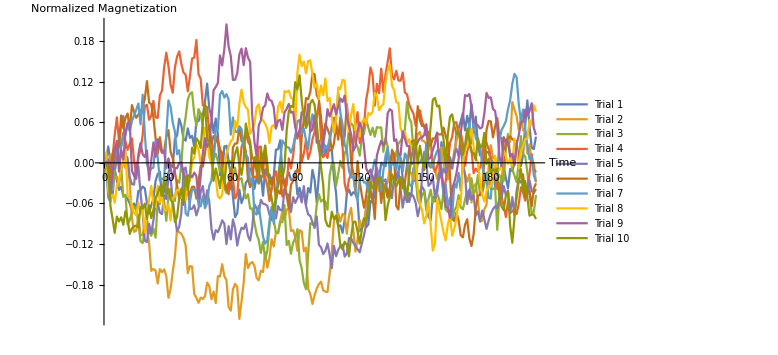

0.0475747

```mathematica
magnetism1={48,242,0,-480,-92,-264,-400,-354,-488,-490,-534,-598,-710,-600,-676,-414,-408,-350,-376,-592,-746,-626,-532,-268,-166,-130,-530,-416,-304,-152,-26,-64,356,402,650,550,352,328,508,368,398,240,618,616,728,698,910,1170,804,676,442,654,424,-184,-164,240,252,18,-194,-498,-802,-744,-394,-594,-502,-296,-246,-96,-72,-384,-222,-306,-190,-486,-96,-180,-170,-260,-188,194,200,334,-136,-342,-216,-142,-248,-254,-124,-466,-368,-486,-472,-620,-372,-440,-104,-252,-586,-188,230,324,134,216,180,194,-216,-448,-940,-922,-1034,-842,-454,-394,-480,-434,-458,-554,-1006,-972,-824,-948,-912,-564,-586,-458,-80,-236,2,-34,-50,142,28,130,128,-260,-138,66,-230,-452,-580,-446,-492,-76,-80,-508,-430,-354,-406,-616,-794,-848,-504,-568,-440,-184,306,82,-88,126,76,-22,68,428,504,612,736,478,694,546,868,460,682,256,108,128,0,164,150,60,4,-364,-224,-470,-396,-68,-226,-374,-90,-122,16,212,110,-48,122,558,922,534,224,204,386}/10000;magnetism2={-20,-222,122,-256,-210,-204,-346,-106,26,-80,26,-300,-814,-1020,-1000,-770,-1064,-1068,-894,-966,-1190,-1594,-1566,-1590,-1782,-1568,-1614,-1574,-1676,-1992,-1864,-1606,-1384,-976,-1026,-1046,-1108,-1222,-1628,-1524,-1532,-1936,-1992,-2066,-1990,-2010,-1970,-1768,-1820,-2014,-1900,-2070,-1672,-1678,-1496,-1670,-1736,-2128,-2182,-1868,-1786,-1832,-2304,-2046,-1764,-1346,-1554,-1486,-1464,-1518,-1696,-1734,-1592,-1612,-1318,-1548,-1396,-1128,-1236,-1026,-1034,-862,-716,-838,-690,-678,-1006,-992,-1098,-1296,-994,-1012,-1306,-1252,-1858,-1936,-2084,-1954,-1856,-1790,-1754,-1882,-1900,-1908,-1636,-1312,-862,-794,-744,-868,-754,-772,-1046,-778,-664,-986,-1310,-1126,-848,-946,-922,-598,-488,-426,-196,-222,-262,-416,-296,-308,-328,-292,-56,24,138,124,86,-32,8,78,102,-118,-154,-268,240,422,454,330,318,274,-50,-34,48,-96,-236,-116,232,-2,-152,-246,-20,-78,178,314,504,428,16,-168,-280,-168,-586,-348,-310,-556,-868,-854,-684,-620,-54,260,70,74,-156,-182,-252,44,232,294,312,896,784,686,484,662,480,470,136,272,18,-2,-290}/10000;
magnetism3={120,-346,-282,-398,-124,46,36,-56,-502,-472,-908,-844,-728,-640,-700,-874,-1158,-1184,-992,-832,-1014,-1076,-970,-1104,-570,-610,-398,-564,-856,-504,-380,-504,-564,-258,-294,-30,464,676,936,1020,1042,716,548,794,716,538,260,252,456,64,58,134,22,-132,-42,-368,-446,-396,-92,-204,-72,-258,-246,-226,-408,-526,-462,-676,-672,-882,-1050,-1138,-1330,-1166,-1426,-1296,-946,-704,-846,-1032,-1040,-870,-878,-624,-1214,-1152,-1342,-1178,-1114,-978,-1436,-1556,-1774,-1864,-1348,-890,-906,-928,-620,-462,-572,-544,-574,-692,-182,-22,-16,-340,-160,30,-74,142,208,502,584,546,304,234,106,374,434,642,520,410,518,386,528,518,522,162,362,240,-74,-10,-20,154,284,324,368,496,900,660,594,182,-202,-542,-614,-474,-426,-710,-532,-398,-588,-526,-452,-540,-684,-410,-694,-724,-722,-844,-708,-646,-476,-660,-686,-544,-418,-532,-228,-456,-390,-180,-482,-448,-316,-144,-186,-386,-388,-364,-990,-484,-186,-266,216,426,114,-102,-186,-286,24,394,134,94,-140,-442,-742,-726,-476}/10000;
magnetism4={-160,-190,-54,82,414,672,320,254,446,314,192,284,360,32,-180,84,186,408,840,856,634,694,914,674,662,994,1068,1410,1626,1428,1156,1034,1408,1566,1646,1458,1332,1300,1056,1276,1540,1554,1814,1306,1240,848,842,820,420,366,88,396,332,204,-70,-268,-370,-464,-120,-234,-526,-462,-102,230,332,456,312,258,-180,-210,-214,236,240,-210,-210,-338,-564,-400,-216,-124,-348,-178,-498,-382,-328,66,-82,102,410,356,486,12,136,344,58,160,348,458,670,890,358,80,138,72,306,532,666,584,412,490,252,-306,-450,-242,-170,312,554,748,294,402,564,930,1112,1406,1292,844,1166,1028,1390,1042,1304,1492,1690,1288,1232,1358,1216,1210,1332,1040,1010,860,788,726,550,764,774,614,526,400,460,334,-52,-136,-56,64,-190,-438,-268,-36,294,380,594,598,410,442,282,-44,168,276,192,-154,-86,-132,-68,56,410,296,200,78,-92,-248,-386,-306,-500,-636,-800,-572,-740,-716,-680,-756,-606,-362,-432,-558,-360,-166,126,-82,-142}/10000;
magnetism5={38,54,-82,-78,-92,152,254,570,690,120,66,-216,-314,-322,-6,-60,-446,-744,-1148,-1170,-900,-1040,-850,-586,-598,-732,-758,-478,-534,-224,-224,-554,-802,-1008,-942,-742,-106,-68,-310,-684,-678,-626,-776,-672,-424,-342,-616,-406,-576,-968,-1134,-994,-1022,-944,-848,-898,-1200,-936,-1130,-836,-964,-1220,-1058,-958,-978,-900,-1076,-1148,-946,-612,-672,-748,-546,-602,-612,-636,-764,-844,-704,-822,-638,-696,-700,-390,-468,-468,-726,-508,-592,-520,-458,-584,-344,-638,-760,-784,-876,-962,-790,-1210,-1246,-1346,-1300,-1190,-1356,-1556,-1226,-1378,-1282,-1234,-1208,-1384,-1338,-1110,-1114,-1180,-1224,-1276,-1320,-1188,-1066,-910,-556,-456,-566,-224,-108,-314,-212,-276,-244,-464,-384,-522,-198,-228,-126,-396,-662,-468,-442,-578,-456,-496,-586,-788,-648,-212,162,2,-340,-306,-202,-514,-360,-148,-222,-86,-148,24,-18,-88,128,208,102,208,-52,-174,-608,-394,-544,-474,-780,-714,-862,-704,-838,-976,-850,-752,-684,-642,-672,-524,-514,-344,-476,-408,-746,-506,-776,-416,-246,-292,-226,-370,-470,-258,-414,-446,-386}/10000;
magnetism6={-176,-328,-202,136,232,56,274,700,510,662,728,478,852,752,664,712,754,822,944,1206,890,862,672,368,134,378,176,170,386,482,160,64,-134,-326,-534,-494,-620,-528,-414,-462,-352,-354,-528,-268,-44,-56,140,386,552,288,396,364,288,192,150,-290,-402,-288,-390,228,284,286,526,322,298,168,-236,-360,-280,82,-130,24,8,-146,238,-190,-236,-326,-218,-552,-410,-456,-250,-264,-486,-674,-324,-266,-190,-92,-168,388,642,956,938,1046,1322,1306,998,934,664,340,582,502,414,178,286,548,342,672,256,394,868,542,20,-154,-446,24,-282,-480,-662,-484,-224,-424,-482,-828,-232,-216,-592,-328,-378,-514,-364,192,128,-640,-688,-284,-258,-296,-34,192,312,330,322,836,626,542,552,524,314,254,358,360,436,418,420,520,396,292,-178,-794,-860,-732,-848,-1070,-1100,-914,-832,-1114,-1228,-1054,-664,-484,-472,-410,58,488,620,610,376,536,662,376,366,20,324,360,390,350,324,320,-22,-166,-172,-506,-418,-420,-638,-382,-302}/10000;
magnetism7={-72,-516,-576,-168,20,248,-42,234,390,410,574,466,618,700,784,876,568,1006,430,-20,-126,-86,-70,324,82,-262,-230,-250,412,922,828,594,462,126,188,-98,-158,-746,-782,-574,-388,-406,-404,-620,-642,-494,-670,-594,-338,-262,44,506,496,1008,1060,962,1014,934,416,670,462,456,540,498,216,130,70,-290,-228,-732,-764,-634,-862,-1090,-1194,-1142,-856,-650,-898,-580,-206,38,328,282,232,226,150,244,386,616,630,432,504,334,206,500,716,596,474,190,110,152,256,210,366,504,464,672,1032,734,564,268,184,-118,-216,-200,-402,-558,-238,-206,-290,-290,-432,-224,-102,44,-112,-144,-422,-114,106,228,-112,16,-30,-100,134,78,-130,138,94,-306,-346,-266,-266,2,6,68,-54,288,-12,-72,-32,90,178,192,-74,-502,-314,-658,-512,-816,-298,-368,-148,-408,22,206,370,586,286,586,362,296,266,-46,-190,-222,-520,-528,10,-106,-186,338,484,544,616,792,924,1166,1312,1264,866,618,786,494,258,52,92,-182,-276}/10000;
magnetism8={164,-412,-510,-470,-590,-332,-266,-40,-32,192,-472,-524,-624,-746,-772,-584,-740,-664,-1026,-730,-538,-340,-610,-652,-336,-580,-494,-676,-706,-612,-852,-520,-496,-400,-404,-514,-524,-544,-304,-264,14,80,274,200,-16,114,516,472,86,-12,-116,-222,-494,-526,-470,-104,138,240,320,352,616,524,870,1080,890,820,784,426,500,572,820,864,662,624,576,504,294,534,558,504,824,902,742,1060,1044,1066,962,940,534,1328,1596,1428,1494,1322,1502,1514,1302,1106,1172,940,1142,998,1244,912,956,676,442,642,1116,1090,1224,1214,750,460,708,868,480,464,388,598,650,578,736,710,754,1034,984,778,832,868,1190,1360,1446,1140,1072,894,884,510,432,460,286,348,200,226,150,-378,-610,-698,-896,-782,-572,-914,-1296,-1190,-548,-710,-864,-1030,-1142,-910,-782,-1076,-970,-826,-556,-600,-10,214,246,350,504,232,78,-8,-270,-470,-570,-420,-346,-350,-176,104,-110,-108,-28,180,94,-16,66,-44,358,170,-88,162,242,352,356,632,554,850,758}/10000;
magnetism9={32,-38,-450,-160,166,326,-130,190,48,442,590,584,-120,-190,-236,124,292,126,86,182,-254,38,300,88,348,228,146,168,-80,66,-78,-232,-76,-80,0,12,-144,-332,-198,-174,-214,-144,-196,-526,-192,136,362,236,300,616,1074,1118,1180,1586,1438,1676,2044,1716,1576,1224,1226,1324,1602,1686,1442,1692,1554,1490,690,314,100,552,628,812,846,1024,926,916,816,508,622,636,486,746,794,870,740,752,526,394,456,746,720,574,866,460,490,698,296,326,120,294,482,792,684,770,866,718,836,950,898,992,686,544,422,176,240,464,596,504,234,-80,-152,-98,-220,-310,110,228,324,258,310,730,792,766,324,346,134,114,466,356,250,246,-18,-4,228,308,362,374,412,570,56,74,188,286,446,6,-156,-334,-652,-664,-812,-370,-290,-152,44,444,676,1000,984,1016,830,612,576,552,506,526,734,1032,958,966,794,766,522,100,-50,380,308,302,96,132,-38,276,408,594,610,786,696,762,880,514,410}/10000;
magnetism10={16,-128,-634,-828,-1034,-792,-866,-804,-916,-714,-838,-1050,-968,-936,-928,-952,-652,-674,-602,-828,-626,-816,-698,-520,-454,-352,-488,-212,-464,-382,-540,-596,-872,-798,-520,-380,-578,-202,-402,-184,224,136,362,318,220,618,884,360,278,160,-266,-84,-210,-374,-114,-304,-6,36,12,-36,132,230,-34,-178,42,580,422,314,62,70,90,-302,182,58,256,-10,-354,-522,-716,-494,-330,-14,-228,-70,478,760,840,824,1190,1082,1292,922,648,514,594,880,930,854,582,248,-68,-324,-838,-926,-944,-722,-830,-776,-944,-1222,-1278,-1164,-1212,-1380,-1088,-874,-868,-1014,-1194,-986,-818,-850,-684,-282,-372,-388,-242,-210,-274,-330,-846,-634,-502,-170,-250,-352,-270,-210,-378,-306,-528,-164,62,246,336,-12,252,62,-108,88,200,546,930,958,832,844,536,350,18,420,676,716,548,430,446,264,118,260,502,340,158,146,40,362,222,248,442,-16,56,-156,-94,-124,-82,-500,-648,-698,-484,-438,-930,-1180,-810,-508,-268,-94,-438,-270,-514,-780,-764,-762,-830}/10000;
ListPlot[{magnetism1,magnetism2,magnetism3,magnetism4,magnetism5,magnetism6,magnetism7,magnetism8,magnetism9,magnetism10},Joined->True,AxesLabel->{"Time","Normalized Magnetization"},ImageSize->Large,PlotRange->All,PlotLegends->{"Trial 1","Trial 2", "Trial 3", "Trial 4","Trial 5","Trial 6","Trial 7","Trial 8","Trial 9","Trial 10"}]
averageMagnetizationHexN200T4=Mean[{averageForOneTrial[magnetism1],averageForOneTrial[magnetism2],averageForOneTrial[magnetism3],averageForOneTrial[magnetism4],averageForOneTrial[magnetism5],averageForOneTrial[magnetism6],averageForOneTrial[magnetism7],averageForOneTrial[magnetism8],averageForOneTrial[magnetism9],averageForOneTrial[magnetism10]}]//N
```

```mathematica
data5=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData5={};
For[kk=1,kk⩽Dimensions[data5]⟦2⟧,kk++,
AppendTo[fullData5,Transpose[data5⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData5⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data5]⟦2⟧,1}]
```

## AntiferroMagnetic 1D

### 100 long, kT=3

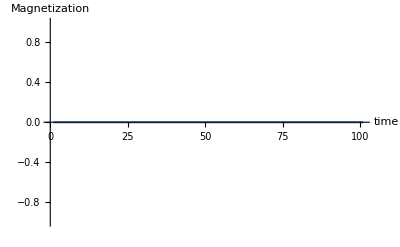

```mathematica
magnetization={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}/100;
ListPlot[magnetization,Joined->True, AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

### 100 long, kT=1

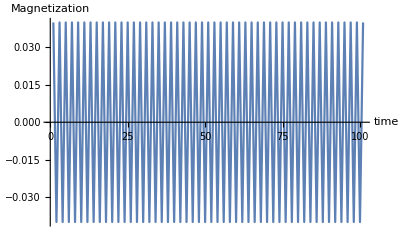

```mathematica
magnetization={4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,4}/100;
ListPlot[magnetization,Joined->True, AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

## AntiferroMagnetic 2D

### 200x200 kT=3, 100 time steps

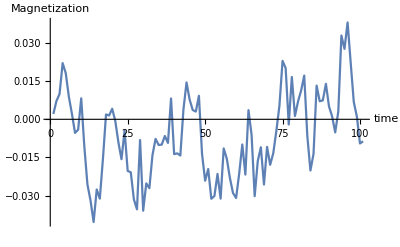

```mathematica
magnetization1={84,288,398,884,726,356,86,-214,-164,330,-428,-1024,-1278,-1616,-1104,-1248,-628,76,60,166,-28,-362,-628,-178,-812,-834,-1260,-1416,-326,-1438,-1008,-1084,-564,-308,-404,-398,-262,-372,328,-548,-536,-570,154,580,310,146,122,370,-542,-966,-782,-1250,-1208,-860,-1248,-458,-620,-922,-1160,-1238,-856,-396,-870,144,-244,-1210,-656,-440,-1026,-434,-716,-534,-182,216,920,806,-82,666,52,280,454,688,-264,-806,-544,530,284,298,558,202,46,-206,122,1318,1108,1524,890,272,42,-380,-346}/40000;
ListPlot[magnetization1,Joined->True,AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

### 200x200 kT=1, 200 time steps

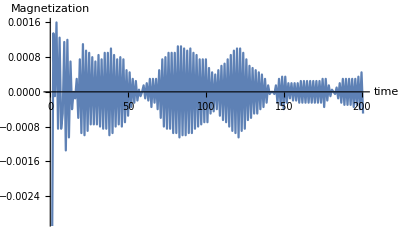

```mathematica
magnetization1={-190,54,-4,64,-34,50,-34,-20,46,-54,48,-42,28,-16,0,-6,12,-24,30,-38,44,-40,38,-36,36,-30,32,-30,28,-30,34,-32,30,-34,36,-34,36,-40,40,-38,34,-32,30,-30,32,-32,30,-28,20,-22,18,-14,12,-10,10,-8,2,-4,0,6,-6,8,-8,12,-14,12,-10,12,-16,20,-24,30,-32,32,-34,36,-34,36,-38,36,-38,42,-42,42,-40,40,-40,38,-38,40,-38,36,-34,34,-32,30,-30,30,-28,30,-28,22,-20,18,-18,16,-16,20,-22,24,-26,26,-28,30,-32,34,-36,38,-38,40,-42,40,-36,36,-34,30,-26,24,-24,22,-20,20,-20,18,-16,16,-14,12,-10,6,-2,0,0,-2,6,-10,12,-12,14,-16,14,-10,8,-6,8,-8,8,-8,8,-10,10,-10,10,-10,10,-10,10,-10,10,-10,10,-10,10,-10,12,-14,12,-8,6,-4,2,0,-2,4,-6,8,-10,12,-12,12,-12,12,-12,12,-14,12,-12,14,-16,18,-20}/40000;
ListPlot[magnetization1,Joined->True,AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

### 20x20 kT=1, 100 time steps

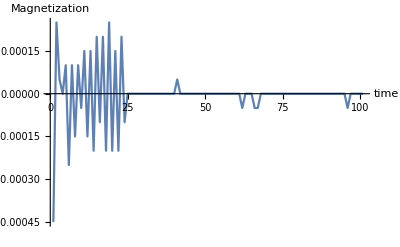

```mathematica
magnetization1={-18,10,2,0,4,-10,4,-6,4,-2,6,-6,6,-8,8,-4,8,-8,10,-8,6,-8,8,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0}/40000;
ListPlot[magnetization1,Joined->True,AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```

### 200x200 kT=1, 200 time steps

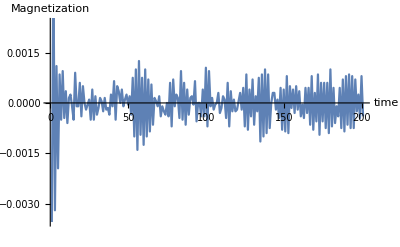

```mathematica
magnetization1={-142,170,-128,44,-78,34,-20,38,-18,14,-24,6,10,-4,-20,36,-4,-4,24,-16,20,0,-8,-2,4,-20,16,-20,8,-14,-6,6,2,-10,6,-8,-6,-14,10,-4,26,-20,20,14,0,16,-4,4,10,-2,8,-14,30,-40,40,-56,50,-38,30,-50,40,-40,28,-34,22,-26,6,2,-4,8,-16,-4,-10,-14,0,-16,24,-28,28,-4,10,6,-18,38,-20,24,-26,16,-14,6,8,-2,26,-22,0,0,-16,16,-16,42,-28,38,-4,6,-8,-2,0,12,-12,-6,8,4,-18,24,-28,14,-10,4,-10,-8,2,12,-8,18,-28,34,-32,16,-16,28,-26,8,-10,30,-46,34,-40,40,-36,34,-30,0,12,12,-8,4,-18,18,-32,16,-34,32,-36,20,-6,16,-12,20,-8,14,-16,-2,-18,18,-12,18,-26,32,-32,12,-22,34,-38,24,-22,24,-30,24,-36,40,-28,18,-24,-4,-16,18,-30,28,-34,32,-26,34,-30,32,-30,28,-10,10,-18,32,-16}/40000;
ListPlot[magnetization1,Joined->True,AxesLabel->{"time","Magnetization"}]
```

```mathematica
data=Import["/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 5/IsingModel/temp.mat"]⟦1⟧;
fullData={};
For[kk=1,kk⩽Dimensions[data]⟦2⟧,kk++,
AppendTo[fullData,Transpose[data⟦All,kk,All⟧]]];
Manipulate[ArrayPlot[fullData⟦k⟧,{ColorRules->{1->Red,-1->Blue}}],{k,1,Dimensions[data]⟦2⟧,1}]
```